# Data & Histogram

## DJI histogram

Here is the histogram of the historical data of daily return of a given index. 
The first few sample cumulants are evaluated and are used to determine the parameter of option pricing models. 
The probability density functions under the Black-Scholes model (red line) and Merton’s jump diffusion model (blue line) are shown as well. 

The given index in the first line can be changed, and this program still works.

20950

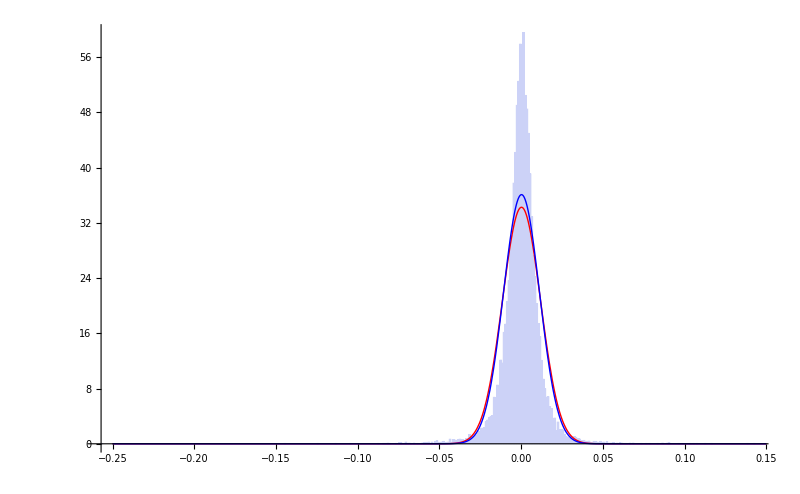

```mathematica
dd=FinancialData["^DJI",All];

aaa=dd;
aaa=aaa//Transpose//Last;
aaa=Delete[aaa, 1]/Delete[aaa, -1]//Log;
aaa//Length
hh=Histogram[aaa,Automatic, "PDF", ImageSize->800];

(* sample cumulant *)
m1=Cumulant[aaa, 1];
m2=Cumulant[aaa, 2];
m3=Cumulant[aaa, 3];
m4=Cumulant[aaa, 4];
m5=Cumulant[aaa, 5];
T=1;

f[S_]:=(48 m3^5 m4^2+16 m3^6 m5-168 m3^4 m4 m5 (m2-S T)+225 m3^2 m4^2 m5 (m2-S T)^2+27 m5 (m2-S T)^3 (m4^3+m5^2 (m2-S T))-9 m3 m4 (m2-S T)^2 (5 m4^3+18 m5^2 (m2-S T))+8 m3^3 (9 m2^2 m5^2+S T (5 m4^3+9 m5^2 S T)-m2 (5 m4^3+18 m5^2 S T)));
s=Solve[f[S]==0, S, Reals];

(* {σ, μ, α, β, λ} *)
i=1;
para={};
Do[
AppendTo[para, 
Solve[{
σ^2==S/.s[[i]], 
μ==1/(2 m4^2 T-2 m3 m5 T)(4 m3^3-7 m2 m3 m4+2 m1 m4^2+3 m2^2 m5-2 m1 m3 m5+7 m3 m4 S T+m4^2 S T-6 m2 m5 S T-m3 m5 S T+3 m5 S^2 T^2)/.s[[i]], 
α==(4 m3 m4-3 m2 m5+3 m5 S T)/(4 m3^2-3 m2 m4+3 m4 S T)/.s[[i]], 
β^2==(m4^2-m3 m5)/(-4 m3^2+3 m4 (m2-S T))/.s[[i]], 
λ==((m1/T-(1/(2 m4^2 T-2 m3 m5 T)(4 m3^3-7 m2 m3 m4+2 m1 m4^2+3 m2^2 m5-2 m1 m3 m5+7 m3 m4 S T+m4^2 S T-6 m2 m5 S T-m3 m5 S T+3 m5 S^2 T^2)-S/2))(4 m3^2-3 m2 m4+3 m4 S T))/(4 m3 m4-3 m2 m5+3 m5 S T)/.s[[i]], 
β>0&&σ>0
} , {σ, μ, α, β, λ}, Reals](* 用 solve 自動虛數挑掉 *)
], {i, Length[s]}]


(* para 不知道有幾組實數解，全畫在 pjd 裡 *)
pjd={};
Do[
AppendTo[pjd, 
Plot[
Sum[(ⅇ^(-λ T)(λ T)^k)/(k!)PDF[NormalDistribution[(μ-σ^2/2)T+k α, √(σ^2 T+k β^2)],x], {k, 0, 3}]/.para[[i]]
,{x,-0.25,0.15}, PlotStyle->Directive[Blue,Thick], PlotRange->All]
], {i, Length[para]}]

pn=Plot[PDF[NormalDistribution[m1,√m2],x],{x,-0.25,0.15}, PlotStyle->Directive[Red,Thick], PlotRange->All];

Show[hh, pn, pjd]
```

## FinancialData[]

### Useful indices or stocks

^TWII		Taiwan stock exchange weighted index
TW : 2317 	a public company in Taiwan
TWO : 3546	a smaller public company in Taiwan

^DJI 		Dow Jones Industrial Average
^GSPC 	S&P 500
^IXIC 		NASDAQ
^SOX 		PHLX Semiconductor Sector

### All indices, stocks, etc.

```mathematica
FinancialData[]
```

```mathematica
{"^A1BSC","^A1CYC","^A1DOW","^A1ENE","^A1FIN","^A1HCR","^A1IDU","^A1NCY","^A1SGI","^A1SGITR","^A1TEC","^A1TLS","^A1UTI","^A3DOW","^A4DOW","AAAAX","AAAGX","AAAIX","AAAPX","AAARX","AAASX","AAATX","AAAZX","AABCX","AABDX","AABFX","AABNX","AABPX","AABTX","AACCX","AACFX","AACIX","AACRX","AACTX","AACYX","AADAX","AADBX","AADCX","AADDX","AADEX","AADIX","AADRX","AADSX","AADTX","AADYX","AAEBX","AAEPX","AAETX","AAFBX","AAFCX","AAFPX","AAFTX","AAGAX","AAGIX","AAGOX","AAGPX","AAGRX","AAGTX","AAHTX","AAHYX","AAIAX","AAIEX","AAINX","AAIPX","AAISX","AAITX","AAIYX","AALGX","AALIX","AALPX","AALTX","AALVX","AAMBX","AAMGX","AAMOX","AAMRX","AAMTX","AAMYX","AANPX","AAPAX","AAPEX","AAPIX","AARBX","AARFX","AARIX","AASAX","AASBX","AASCX","AASFX","^AASGI","^AASGITR","AASMX","AASOX","AASPX","AASSX","AASVX","AAUTX","AAVIX","^AAVY","AAXAX","AAXCX","AAZAX","AAZBX","AAZCX","ABAAX","ABACX","ABAFX","ABAGX","ABALX","ABAMX","ABARX","ABASX","ABBAX","ABBBX","ABBCX","ABBDX","ABBGX","ABBIX","ABBKX","ABBRX","ABBSX","ABBYX","ABCCX","ABCFX","ABCGX","ABCSX","ABDAX","ABDIX","ABEAX","ABECX","ABEIX","ABEMX","ABEYX","ABFAX","ABFBX","ABGAX","ABGIX","ABGKX","ABGRX","ABGYX","ABHAX","ABHFX","ABHIX","ABHMX","ABHYX","ABIAX","ABIBX","ABICX","ABIFX","ABIIX","ABINX","ABIPX","ABIRX","ABISX","ABIYX","ABKYX","ABLAX","ABLCX","ABLDX","ABLIX","ABLOX","ABLPX","ABLRX","ABLSX","ABLYX","ABMAX","ABMBX","ABMIX","ABMRX","ABNAX","ABNCX","ABNDX","ABNFX","ABNIX","ABNKX","ABNOX","ABNRX","ABNTX","ABNYX","ABPAX","ABPBX","ABPCX","ABPRX","ABPYX","ABQBX","ABQCX","ABQIX","ABQKX","ABQRX","ABQUX","ABQYX","ABRBX","ABRCX","ABRFX","ABRIX","ABRRX","ABRUX","ABRYX","ABRZX","ABSAX","ABSCX","ABSIX","ABSKX","ABSLX","ABSRX","ABSYX","ABTAX","ABTCX","ABTFX","ABTHX","ABTIX","ABTPX","ABTRX","ABTYX","ABUAX","ABVAX","ABVBX","ABVCX","ABVIX","ABVKX","ABVRX","ABVYX","ABWAX","ABWBX","ABWCX","ABWIX","ABWKX","ABWRX","ABWYX","ABXAX","ABXBX","ABXCX","ABYSX","ABZAX","ABZBX","ABZCX","ABZIX","ABZKX","ABZRX","ABZYX","ACAAX","ACABX","ACACX","ACAGX","ACAIX","ACAPX","ACARX","ACASX","ACBGX","ACBIX","ACBKX","ACBLX","ACBPX","^ACBQ","ACBVX","ACBYX","ACCAX","ACCBX","ACCDX","ACCEX","ACCFX","ACCHX","ACCIX","ACCJX","ACCKX","ACCLX","ACCNX","ACCOX","ACCPX","ACCQX","ACCRX","ACCSX","ACCUX","ACCVX","^ACD","ACDAX","ACDBX","ACDCX","ACDIX","ACDMX","ACDRX","ACDVX","ACDYX","ACECX","ACEHX","ACEIX","ACENX","ACEOX","ACEPX","ACEQX","ACERX","ACESX","ACETX","ACEUX","ACEVX","ACEYX","ACFBX","ACFCX","ACFDX","ACFFX","ACFMX","ACFOX","ACFRX","ACFSX","ACFTX","ACFWX","ACFYX","ACGAX","ACGCX","ACGDX","ACGEX","ACGGX","ACGHX","ACGIX","ACGJX","ACGKX","ACGLX","ACGMX","ACGOX","ACGSX","ACGTX","ACGUX","ACGVX","ACHAX","ACHBX","ACHCX","ACHIX","ACHVX","ACHWX","ACHYX","ACHZX","ACIAX","ACIBX","ACICX","ACIDX","ACIEX","ACIFX","ACIGX","ACIIX","ACIJX","ACIKX","ACIMX","ACINX","ACIOX","ACIQX","ACIRX","ACITX","ACIUX","ACIVX","ACIYX","ACKBX","ACLAX","ACLBX","ACLCX","ACLDX","ACLEX","ACLGX","ACLKX","ACLLX","ACLMX","ACLNX","ACLOX","ACLRX","ACLSX","ACLTX","ACLVX","ACLWX","ACLYX","ACMCX","ACMEX","ACMFX","ACMGX","ACMHX","ACMIX","ACMLX","ACMNX","ACMRX","ACMSX","ACMTX","ACMVX","ACMYX","ACNAX","ACNBX","ACNCX","ACNIX","ACNLX","ACNRX","ACNVX","ACNYX","ACOAX","ACOIX","ACOVX","ACOYX","ACPAX","ACPBX","ACPCX","ACPDX","ACPIX","ACPRX","ACPSX","ACQIX","ACRBX","ACRCX","ACRDX","ACREX","ACRNX","ACROX","ACRYX","ACSCX","ACSDX","ACSIX","ACSJX","ACSKX","ACSLX","ACSMX","ACSNX","ACSPX","ACSQX","ACSRX","ACSSX","ACSTX","ACSUX","ACSWX","ACSYX","ACTCX","ACTDX","ACTEX","ACTFX","ACTGX","ACTHX","ACTIX","ACTTX","ACTVX","ACTWX","ACTYX","ACUIX","ACUYX","ACVAX","ACVBX","ACVFX","ACVIX","ACVRX","ACVUX","ACWBX","ACWCX","ACWIX","ACWRX","ACWVX","ACXAX","ACXBX","ACXCX","ACYBX","ACYCX","ACYIX","ACYRX","ACYSX","ACYVX","ACYYX","ADAIX","ADANX","ADBAX","ADBNX","ADBYX","ADCCX","ADCEX","ADCIX","ADCNX","ADCVX","ADECX","ADEGX","ADENX","ADFAX","ADFIX","ADFSX","ADGAX","ADGBX","ADGCX","ADGIX","ADGKX","ADGRX","ADGYX","ADHCX","ADIDX","ADIEX","ADIIX","ADINX","ADJEX","ADJPX","ADKSX","ADPAX","ADPBX","ADPCX","^ADR","^ADRAD","^ADRAI","^ADRAM","^ADRAN","^ADRAS","^ADRAT","^ADRDD","^ADRDI","^ADRDM","^ADRDN","^ADRDS","^ADRDT","^ADRED","^ADREI","^ADREM","^ADREN","^ADRES","^ADRET","ADRIX","ADRNX","ADRRX","^ADRUD","^ADRUI","^ADRUM","^ADRUN","^ADRUS","^ADRUT","ADSIX","ADSTX","ADTRX","ADTWX","ADVAX","ADVDX","ADVGX","ADVIX","ADVRX","ADYBX","AECCX","AECDX","AECIX","AECOX","AECPX","AEDAX","AEDBX","AEDCX","AEDRX","AEDYX","AEEBX","AEEIX","AEGBX","AEGFX","AEGIX","AEIAX","AEICX","AEIGX","AEKBX","AELAX","AELCX","AELIX","AELRX","AELSX","AEMAX","AEMCX","AEMEX","AEMFX","AEMGX","AEMIX","AEMMX","AEMPX","AEMRX","AEMSX","AEPCX","AEPFX","AEPGX","AESAX","AESBX","AESCX","AESGX","AESIX","AETAX","AEURX","AEVYX","AEWRX","^AEX","AEYBX","AEYCX","AEYIX","AEYRX","AFAAX","AFASX","AFATX","AFBAX","AFBEX","AFBIX","AFBQX","AFBSX","AFCAX","AFCCX","AFCFX","AFCIX","AFCTX","AFDAX","AFDBX","AFDCX","AFDDX","AFDIX","AFDRX","AFEAX","AFEIX","AFFIX","AFFSX","AFGAX","AFGBX","AFGCX","AFGGX","AFGLX","AFGNX","AFGPX","AFGRX","AFHAX","AFHCX","AFHYX","AFIAX","AFIBX","AFICX","AFIEX","AFIFX","AFISX","AFITX","AFJAX","AFJCX","AFJDX","AFLGX","^AFLI","AFLVX","AFMAX","AFMCX","AFMIX","AFMMX","AFNCX","AFPAX","AFRAX","AFRCX","AFREX","AFRIX","AFRRX","AFRYX","AFSAX","AFSCX","AFSGX","AFSIX","AFSVX","AFTAX","AFTBX","AFTCX","AFTEX","AFTFX","AFTIX","AFTRX","AFTSX","AFTYX","AFUAX","AFUCX","AFVAX","AFVBX","AFVCX","AFVIX","AFVPX","AGAAX","AGABX","AGACX","AGADX","AGAIX","AGALX","AGAMX","AGAPX","AGARX","AGAYX","AGBBX","AGBCX","AGBIX","AGCCX","AGCGX","AGCIX","AGDAX","AGDBX","AGDCX","AGDIX","AGDKX","AGDRX","AGDYX","AGECX","AGFAX","AGFCX","AGFIX","AGFKX","AGFRX","AGGAX","AGGBX","AGGCX","^AGG-EU","AGGGX","^AGG-IV","AGGIX","^AGG-NV","AGGNX","AGGRX","^AGG-SO","^AGG-TC","AGGWX","AGGYX","AGIAX","AGIBX","AGICX","^AGIEM","^AGIEME","^AGIEMXL","^AGIEMXLE","AGIFX","^AGIGL","^AGIGLE","AGIGX","AGIIX","^AGINA","^AGINAE","^AGINAXL","^AGINAXLE","AGINX","AGIRX","AGISX","AGIVX","^AGIXL","^AGIXLE","AGIYX","AGLAX","AGLCX","AGLDX","AGLIX","AGLMX","AGLPX","AGLRX","AGLSX","AGMIX","AGMNX","AGMPX","AGMWX","AGNIX","AGOAX","AGOBX","AGOCX","AGOIX","AGORX","AGOVX","AGPLX","AGRAX","AGRBX","AGRCX","AGREX","AGRFX","AGRIX","AGROX","AGRPX","AGRRX","AGRYX","AGSAX","AGSBX","AGSCX","AGSDX","AGSIX","AGSKX","AGSPX","AGSRX","AGTFX","AGTHX","AGTIX","AGVBX","AGVCX","AGVIX","AGVRX","AGVYX","AGWAX","AGWBX","AGWCX","AGWFX","AGWRX","AGWYX","AGYBX","AGYCX","AHADX","AHAFX","AHALX","AHBAX","AHBIX","AHDCX","AHDEX","AHECX","AHEGX","AHERX","AHFMX","AHGCX","AHHYX","AHICX","AHIFX","AHITX","AHIYX","AHLFX","AHMAX","AHMBX","AHMCX","AHMFX","AHMIX","AHMYX","AHRAX","AHSAX","AHSBX","AHSCX","AHSRX","AHTBX","AHTCX","AHTFX","AHTRX","AHYBX","AHYCX","AHYFX","AHYIX","AHYPX","AHYRX","AHYVX","AIAAX","AIACX","AIAIX","AIANX","AIARX","AIAVX","AIBAX","AIBCX","AIBDX","AIBFX","AIBLX","AIBNX","AIBRX","AICAX","AICBX","AICCX","AICFX","AICIX","AICRX","AIDAX","AIDBX","AIDIX","AIEAX","AIEBX","AIECX","AIEQX","AIERX","AIESX","AIEVX","AIFAX","AIFBX","AIFCX","AIFDX","AIFIX","AIFPX","AIFRX","AIGAX","AIGBX","AIGCX","AIGGX","AIGMX","AIGOX","AIGPX","AIGTX","AIGYX","AIIEX","AIIIX","AIINX","AIIRX","AIIVX","AIIYX","AILAX","AILGX","AILIX","AILVX","AIMAX","AIMCX","AIMGX","AIMIX","AIMOX","AIMRX","AINAX","AINOX","AINYX","AIOAX","AIOBX","AIOCX","AIOIX","AIORX","AIPIX","AIPTX","AIQBX","AIQCX","AISAX","AISBX","AISCX","AISGX","AISHX","AISIX","AISRX","AISTX","AISVX","AITAX","AITEX","AITFX","AITIX","AIURX","AIVAX","AIVIX","AIVKX","AIVOX","AIVPX","AIVRX","AIVSX","AIWCX","AIZAX","AIZBX","AIZCX","AJFAX","AJFBX","AJFCX","AJFIX","AJFYX","^AJT","^AJT-EU","^AJT-NV","^AJT-SO","^AJT-TC","^AKG","^AKG-EU","^AKG-NV","^AKG-SO","^AKG-TC","AKIRX","AKREX","AKRIX","ALAAX","ALABX","ALARX","ALAYX","ALBAX","ALBCX","ALBRX","ALBVX","ALCAX","ALCBX","ALCCX","ALCGX","ALCKX","ALCPX","ALCRX","ALCVX","ALDAX","ALDBX","ALDIX","ALEGX","ALEIX","ALFAX","ALFBX","ALFCX","ALFFX","ALFIX","ALFQX","ALFRX","ALFYX","ALGAX","ALGBX","ALGCX","ALGIX","ALGRX","ALHIX","ALIAX","ALIBX","ALICX","ALIIX","ALIRX","ALISX","ALLBX","ALLIX","ALMAX","ALMBX","ALMCX","ALMIX","ALMRX","ALNBX","ALNCX","ALNFX","ALNVX","ALNYX","ALODX","ALOIX","ALOPX","ALORX","ALOVX","ALPAX","ALPCX","ALPHX","ALQBX","ALSAX","ALSCX","ALSIX","ALSNX","ALSOX","ALSRX","ALTAX","ALTBX","ALTCX","ALTEX","ALTFX","ALTHX","ALTVX","ALVAX","ALVCX","ALVIX","ALVOX","ALVRX","ALVSX","ALWRX","ALYBX","AMAAX","AMABX","AMACX","AMADX","AMAGX","AMANX","^AMBAP","AMBBX","AMBCX","AMBDX","^AMBEUR","AMBEX","AMBFX","^AMBG","^AMBGB","^AMBGL","^AMBGML","^AMBGNL","^AMBGR","AMBGX","AMBIX","^AMBUB","^AMBUH","^AMBUL","^AMBULH","^AMBUML","^AMBUPC","^AMBUS","AMBYX","AMCFX","AMCGX","AMCIX","AMCMX","AMCPX","AMCRX","AMCSX","AMCYX","AMDAX","AMDBX","AMDCX","AMDEX","AMDIX","AMDPX","AMDSX","AMDWX","AMECX","AMEFX","AMEIX","AMEX:AAB-WT","AMEX:AA-P","AMEX:AA.PR","AMEX:AAU","AMEX:ABH","AMEX:ABL","AMEX:ACD","AMEX:ACU","AMEX:ACY","AMEX:ADG","AMEX:ADGE","AMEX:ADH","AMEX:ADJ","AMEX:ADK","AMEX:ADK-WT","AMEX:ADL","AMEX:AE","AMEX:AEN","AMEX:AEY","AMEX:AEZ","AMEX:AFI-PJ","AMEX:AFO","AMEX:AFP","AMEX:AGB","AMEX:AGG","AMEX:AGT","AMEX:AGW","AMEX:AGX","AMEX:AHB","AMEX:AHI","AMEX:AHY","AMEX:AID","AMEX:AII","AMEX:AIM","AMEX:AIP","AMEX:AIS","AMEX:AKC","AMEX:AKE","AMEX:AKN","AMEX:ALN","AMEX:ALR","AMEX:ALY","AMEX:AMK","AMEX:AMM","AMEX:AMS","AMEX:AMW","AMEX:AMY","AMEX:ANJ","AMEX:ANO","AMEX:ANV","AMEX:ANX","AMEX:ANY","AMEX:AOF","AMEX:API","AMEX:APP","AMEX:APT","AMEX:AQQ","AMEX:ARD-WT","AMEX:ARR","AMEX:ASB","AMEX:ASC","AMEX:ATA","AMEX:ATC","AMEX:ATSC","AMEX:ATX","AMEX:AUMN","AMEX:AUS","AMEX:AUY-WT","AMEX:AVN","AMEX:AWD","AMEX:AWO","AMEX:AWX","AMEX:AXD","AMEX:AXF","AMEX:AXK","AMEX:AXN","AMEX:AXU","AMEX:AYS","AMEX:AZC","AMEX:AZK","AMEX:AZP","AMEX:BAA","AMEX:BAA-WT","AMEX:BBH","AMEX:BCL","AMEX:BCT","AMEX:BCU","AMEX:BCV","AMEX:BDH","AMEX:BDL","AMEX:BDR","AMEX:BEM","AMEX:BFL","AMEX:BFL-WT","AMEX:BFN","AMEX:BFY","AMEX:BGD","AMEX:BGF","AMEX:BHB","AMEX:BHH","AMEX:BHO","AMEX:BHV","AMEX:BIK","AMEX:BIL","AMEX:BIO","AMEX:BIO-B","AMEX:BIR-PA","AMEX:BIR.PR.A","AMEX:BIS","AMEX:BIV","AMEX:BJK","AMEX:BJT","AMEX:BJV","AMEX:BJW","AMEX:BKG","AMEX:BKJ","AMEX:BKR","AMEX:BLB","AMEX:BLD","AMEX:BLE","AMEX:BLJ","AMEX:BLM","AMEX:BLV-P","AMEX:BLZ","AMEX:BMI","AMEX:BMJ","AMEX:BNC","AMEX:BND","AMEX:BNP","AMEX:BNR","AMEX:BNX","AMEX:BOA-I","AMEX:BOA-K","AMEX:BOA.K","AMEX:BOA-L","AMEX:BOA.L","AMEX:BOA-N","AMEX:BOA.N","AMEX:BOA-O","AMEX:BOA.O","AMEX:BOA-V","AMEX:BOA.V","AMEX:BOA-Y","AMEX:BOA.Y","AMEX:BOI","AMEX:BOO","AMEX:BOR-B","AMEX:BOR.B","AMEX:BOR-C","AMEX:BOR.C","AMEX:BOR-D","AMEX:BOR.D","AMEX:BOR-E","AMEX:BOR.E","AMEX:BOR-F","AMEX:BOR.F","AMEX:BOR-H","AMEX:BOR.H","AMEX:BOR-J","AMEX:BOR.J","AMEX:BOR-L","AMEX:BOR.L","AMEX:BOR-N","AMEX:BOR.N","AMEX:BOR-Q","AMEX:BOR.Q","AMEX:BOR-S","AMEX:BOR.S","AMEX:BOR-T","AMEX:BOR.T","AMEX:BOR-U","AMEX:BPD","AMEX:BPF","AMEX:BPG","AMEX:BPS","AMEX:BQI","AMEX:BQY","AMEX:BRD","AMEX:BRN","AMEX:BRR","AMEX:BSA","AMEX:BSL","AMEX:BSN-A","AMEX:BSV","AMEX:BTC","AMEX:BTC-U","AMEX:BTC.U","AMEX:BTC-WT","AMEX:BTI","AMEX:BTN","AMEX:BTR","AMEX:BTW","AMEX:BTX","AMEX:BUF","AMEX:BUN","AMEX:BVX","AMEX:BWL-A","AMEX:BWL.A","AMEX:BWN","AMEX:BWR","AMEX:BWV","AMEX:BWX","AMEX:BXA","AMEX:BXB","AMEX:BXT","AMEX:BXU","AMEX:BYF-D","AMEX:BYF.D","AMEX:BYL","AMEX:BYL-P","AMEX:BZC","AMEX:BZI","AMEX:BZI-WTA","AMEX:BZI-WTB","AMEX:BZM","AMEX:BZZ","AMEX:CAA","AMEX:CAC","AMEX:CAK","AMEX:CAP","AMEX:CAS","AMEX:CAW","AMEX:CAX","AMEX:CBJ","AMEX:CBN","AMEX:CBP","AMEX:CBS-I","AMEX:CBS.I","AMEX:CCA","AMEX:CCF","AMEX:CDM","AMEX:CDS-U","AMEX:CDS-WT","AMEX:CDY","AMEX:CEF","AMEX:CET","AMEX:CEV","AMEX:CFD","AMEX:CFK","AMEX:CFP","AMEX:CFS","AMEX:CFW","AMEX:CFX","AMEX:CGC","AMEX:CGL-A","AMEX:CGL.A","AMEX:CGR","AMEX:CGW","AMEX:CH","AMEX:CHGS","AMEX:CHM","AMEX:CHM-U","AMEX:CHM-WT","AMEX:CHQ","AMEX:CHV","AMEX:CHV-U","AMEX:CHV-WT","AMEX:CIK","AMEX:CIL","AMEX:CIO","AMEX:CIO-U","AMEX:CIO-WT","AMEX:CJM","AMEX:CKK","AMEX:CKX","AMEX:CLM","AMEX:CLQ","AMEX:CLY","AMEX:CMF","AMEX:CMFO","AMEX:CMT","AMEX:CNAM","AMEX:CNET","AMEX:CNGL","AMEX:CNM","AMEX:CNR","AMEX:CNU","AMEX:CNY","AMEX:CO","AMEX:COHN","AMEX:CONM","AMEX:COR","AMEX:COS","AMEX:CPD","AMEX:CPHI","AMEX:CPI","AMEX:CQP","AMEX:CRC","AMEX:CRF","AMEX:CRJ","AMEX:CRMD","AMEX:CRO","AMEX:CRU","AMEX:CRV","AMEX:CRVP","AMEX:CSD","AMEX:CSM","AMEX:CSW","AMEX:CTE","AMEX:CTO","AMEX:CUB","AMEX:CUO","AMEX:CUR","AMEX:CUS-A","AMEX:CUS.A","AMEX:CUT","AMEX:CVF","AMEX:CVM","AMEX:CVP","AMEX:CVR","AMEX:CVU","AMEX:CVV","AMEX:CVY","AMEX:CWI","AMEX:CXA","AMEX:CXI","AMEX:CXM","AMEX:CXM-P","AMEX:CXZ","AMEX:CYM","AMEX:CZA","AMEX:CZJ","AMEX:CZP","AMEX:DAR","AMEX:DAX","AMEX:DBA","AMEX:DBB","AMEX:DBC","AMEX:DBE","AMEX:DBO","AMEX:DBP","AMEX:DBS","AMEX:DBV","AMEX:DBX","AMEX:DBY","AMEX:DBZ","AMEX:DCD","AMEX:DCV","AMEX:DDD","AMEX:DDG","AMEX:DDM","AMEX:DEF","AMEX:DEJ","AMEX:DEK","AMEX:DEK-U","AMEX:DEK-WT","AMEX:DES","AMEX:DFB","AMEX:DFM","AMEX:DFR","AMEX:DFZ","AMEX:DGC","AMEX:DGK","AMEX:DGL","AMEX:DGSE","AMEX:DGT","AMEX:DHC","AMEX:DHS","AMEX:DHY","AMEX:DIA","AMEX:DIG","AMEX:DII","AMEX:DIM","AMEX:DIT","AMEX:DJL","AMEX:DLA","AMEX:DLN","AMEX:DLS","AMEX:DMC","AMEX:DMF","AMEX:DMJ","AMEX:DMS","AMEX:DMY","AMEX:DNM","AMEX:DNN","AMEX:DOG","AMEX:DOL","AMEX:DON","AMEX:DOO","AMEX:DOY","AMEX:DPP","AMEX:DPW","AMEX:DRA","AMEX:DRJ","AMEX:DRN","AMEX:DRU","AMEX:DRW","AMEX:DSC","AMEX:DSG","AMEX:DSI","AMEX:DSV","AMEX:DTD","AMEX:DTN","AMEX:DUG","AMEX:DVK","AMEX:DVS","AMEX:DVY","AMEX:DWX","AMEX:DXD","AMEX:DXN","AMEX:DXR","AMEX:DYT-P","AMEX:DYT-WT","AMEX:EAD","AMEX:EAG","AMEX:EAP","AMEX:EAR","AMEX:EAZ","AMEX:EBB","AMEX:EBK","AMEX:EBY","AMEX:ECB","AMEX:ECF","AMEX:EDA","AMEX:EDV","AMEX:EEB","AMEX:EEC","AMEX:EEI","AMEX:EEM","AMEX:EEN","AMEX:EES","AMEX:EEV","AMEX:EEZ","AMEX:EFA","AMEX:EFC","AMEX:EFG","AMEX:EFH","AMEX:EFM","AMEX:EFP","AMEX:EFU","AMEX:EFV","AMEX:EFZ","AMEX:EGAS","AMEX:EGI","AMEX:EGJ","AMEX:EGK","AMEX:EGL","AMEX:EGL-WT","AMEX:EGO","AMEX:EGR","AMEX:EGT","AMEX:EGX","AMEX:EHC","AMEX:EHD","AMEX:EHN","AMEX:EHP","AMEX:EIA","AMEX:EIF","AMEX:EIM","AMEX:EIO","AMEX:EIP","AMEX:EIV","AMEX:EJC","AMEX:EJS","AMEX:EKC","AMEX:EKG","AMEX:EKH","AMEX:EKJ","AMEX:EKK","AMEX:EKV","AMEX:EKY","AMEX:ELC","AMEX:ELG","AMEX:ELJ","AMEX:ELR","AMEX:ELU","AMEX:ELV","AMEX:EMAN","AMEX:EMG","AMEX:EMI","AMEX:EMJ","AMEX:EML","AMEX:EMM","AMEX:EMV","AMEX:ENA","AMEX:END","AMEX:ENG","AMEX:ENX","AMEX:ENY","AMEX:EOA","AMEX:EOF","AMEX:EPH","AMEX:EPI","AMEX:EPK","AMEX:EPM","AMEX:EPP","AMEX:EPS","AMEX:EQL","AMEX:ERC","AMEX:ERH","AMEX:ERS","AMEX:ERV","AMEX:ESA","AMEX:ESA-U","AMEX:ESA.U","AMEX:ESA-WT","AMEX:ESC","AMEX:ESM","AMEX:ESP","AMEX:EST","AMEX:EST-WT","AMEX:ETF","AMEX:ETI","AMEX:EUF","AMEX:EUM","AMEX:EVI","AMEX:EVJ","AMEX:EVK","AMEX:EVM","AMEX:EVO","AMEX:EVP","AMEX:EVV","AMEX:EVX","AMEX:EVY","AMEX:EWA","AMEX:EWC","AMEX:EWD","AMEX:EWG","AMEX:EWH","AMEX:EWI","AMEX:EWJ","AMEX:EWK","AMEX:EWL","AMEX:EWM","AMEX:EWN","AMEX:EWO","AMEX:EWP","AMEX:EWQ","AMEX:EWS","AMEX:EWT","AMEX:EWU","AMEX:EWV","AMEX:EWW","AMEX:EWX","AMEX:EWY","AMEX:EWZ","AMEX:EXB","AMEX:EXK","AMEX:EXT","AMEX:EXX-A","AMEX:EXX-B","AMEX:EYA","AMEX:EYJ","AMEX:EYW","AMEX:EZA","AMEX:EZM","AMEX:EZU","AMEX:EZY","AMEX:FAB","AMEX:FAD","AMEX:FAX","AMEX:FBK-P","AMEX:FBT","AMEX:FCI","AMEX:FCO","AMEX:FDD","AMEX:FDL","AMEX:FDM","AMEX:FDN","AMEX:FDV","AMEX:FEN","AMEX:FEU","AMEX:FEX","AMEX:FEZ","AMEX:FFF","AMEX:FFI","AMEX:FFR","AMEX:FGD","AMEX:FKL","AMEX:FLL","AMEX:FNE","AMEX:FNG-P","AMEX:FNX","AMEX:FOA","AMEX:FOH","AMEX:FPB","AMEX:FPP","AMEX:FPPC","AMEX:FPX","AMEX:FRD","AMEX:FRG","AMEX:FRI","AMEX:FRN","AMEX:FRS","AMEX:FSI","AMEX:FSP","AMEX:FTA","AMEX:FTC","AMEX:FTF","AMEX:FTK","AMEX:FUE","AMEX:FVD","AMEX:FVE","AMEX:FVI","AMEX:FVL","AMEX:FWV","AMEX:FXD","AMEX:FXE","AMEX:FXG","AMEX:FXH","AMEX:FXI","AMEX:FXL","AMEX:FXN","AMEX:FXO","AMEX:FXP","AMEX:FXR","AMEX:FXU","AMEX:FXZ","AMEX:FYX","AMEX:GAC","AMEX:GAC-U","AMEX:GAC-WT","AMEX:GAD","AMEX:GAF","AMEX:GAN","AMEX:GAU","AMEX:GBC","AMEX:GBG","AMEX:GBI","AMEX:GBN","AMEX:GBO","AMEX:GBR","AMEX:GCC","AMEX:GDX","AMEX:GDY","AMEX:GEB","AMEX:GEL","AMEX:GEX","AMEX:GFE","AMEX:GFE-","AMEX:GFN","AMEX:GGN","AMEX:GGN-PA","AMEX:GGN.PR.A","AMEX:GGR","AMEX:GGW","AMEX:GHC","AMEX:GHC-U","AMEX:GHM","AMEX:GIA","AMEX:GIC","AMEX:GII","AMEX:GIT","AMEX:GIW","AMEX:GKO","AMEX:GLA","AMEX:GLA-U","AMEX:GLA.U","AMEX:GLA-WT","AMEX:GLD","AMEX:GLO","AMEX:GLQ","AMEX:GLU","AMEX:GLV","AMEX:GMF","AMEX:GML","AMEX:GMM","AMEX:GMO","AMEX:GMY","AMEX:GOC","AMEX:GOE","AMEX:GOK","AMEX:GORO","AMEX:GPR","AMEX:GRC","AMEX:GRF","AMEX:GRH","AMEX:GRI","AMEX:GRN","AMEX:GRS","AMEX:GRU","AMEX:GRZ","AMEX:GSB","AMEX:GSD-B","AMEX:GSD.B","AMEX:GSN-B","AMEX:GSN.B","AMEX:GSN-C","AMEX:GSN.C","AMEX:GSN-D","AMEX:GSN.D","AMEX:GSS","AMEX:GST","AMEX:GSX","AMEX:GTE","AMEX:GTF","AMEX:GTU","AMEX:GUR","AMEX:GV","AMEX:GVP","AMEX:GW","AMEX:GWL","AMEX:GWX","AMEX:GXC","AMEX:GZV","AMEX:HA","AMEX:HAO","AMEX:HAP","AMEX:HAQ-U","AMEX:HBE","AMEX:HBP","AMEX:HBY","AMEX:HCM","AMEX:HDO","AMEX:HDY","AMEX:HEB","AMEX:HER","AMEX:HEV","AMEX:HFB","AMEX:HGI","AMEX:HH","AMEX:HHH","AMEX:HKN","AMEX:HLD","AMEX:HLD-U","AMEX:HLD-WT","AMEX:HLM-P","AMEX:HLM.PR","AMEX:HMG","AMEX:HMR","AMEX:HMR-U","AMEX:HMR-WT","AMEX:HNB","AMEX:HNW","AMEX:HPB","AMEX:HPJ","AMEX:HQS","AMEX:HRO","AMEX:HRT","AMEX:HSJ","AMEX:HT","AMEX:HTM","AMEX:HT-PA","AMEX:HUSA","AMEX:HWG","AMEX:HWK","AMEX:HX","AMEX:HYG","AMEX:IAF","AMEX:IAH","AMEX:IAI","AMEX:IAK","AMEX:IAT","AMEX:IAU","AMEX:IAX","AMEX:IBB","AMEX:IBF","AMEX:ICF","AMEX:ICH","AMEX:ICT","AMEX:IDI","AMEX:IDI-U","AMEX:IDI.U","AMEX:IDI-WT","AMEX:IDJ","AMEX:IDN","AMEX:IDU","AMEX:IEC","AMEX:IEF","AMEX:IEI","AMEX:IEL","AMEX:IEO","AMEX:IEV","AMEX:IEZ","AMEX:IF","AMEX:IFK","AMEX:IFL","AMEX:IFL-WT","AMEX:IFT","AMEX:IG","AMEX:IGC","AMEX:IGC-U","AMEX:IGC.U","AMEX:IGC-WT","AMEX:IGE","AMEX:IGM","AMEX:IGN","AMEX:IGP","AMEX:IGR","AMEX:IGV","AMEX:IGW","AMEX:IHE","AMEX:IHF","AMEX:IHI","AMEX:IHT","AMEX:IIA","AMEX:IIG","AMEX:IIH","AMEX:IIL","AMEX:IIN","AMEX:IJH","AMEX:IJJ","AMEX:IJK","AMEX:IJR","AMEX:IJS","AMEX:IJT","AMEX:ILC","AMEX:ILF","AMEX:ILG","AMEX:IME","AMEX:IMH","AMEX:IMO","AMEX:IMW","AMEX:INI","AMEX:INO","AMEX:INS","AMEX:INUV","AMEX:INV","AMEX:INY","AMEX:IOC","AMEX:IOT","AMEX:IOX","AMEX:IPB","AMEX:IPD","AMEX:IPE","AMEX:IPF","AMEX:IPJ-B","AMEX:IPK","AMEX:IPN","AMEX:IPS","AMEX:IPT","AMEX:IPU","AMEX:IPW","AMEX:IRO","AMEX:IRV","AMEX:IRY","AMEX:ISC","AMEX:ISI","AMEX:ISL","AMEX:ISO","AMEX:ISR","AMEX:IST","AMEX:ITA","AMEX:ITB","AMEX:ITE","AMEX:ITF","AMEX:ITI","AMEX:ITM","AMEX:ITM-A","AMEX:ITM.A","AMEX:IVA","AMEX:IVD","AMEX:IVE","AMEX:IVI","AMEX:IVV","AMEX:IVW","AMEX:IVX","AMEX:IWB","AMEX:IWC","AMEX:IWD","AMEX:IWF","AMEX:IWK","AMEX:IWM","AMEX:IWN","AMEX:IWO","AMEX:IWP","AMEX:IWR","AMEX:IWS","AMEX:IWV","AMEX:IWW","AMEX:IWZ","AMEX:IXC","AMEX:IXG","AMEX:IXJ","AMEX:IXN","AMEX:IXP","AMEX:IYC","AMEX:IYE","AMEX:IYF","AMEX:IYG","AMEX:IYH","AMEX:IYJ","AMEX:IYK","AMEX:IYM","AMEX:IYR","AMEX:IYT","AMEX:IYW","AMEX:IYY","AMEX:IYZ","AMEX:JAX","AMEX:JCS","AMEX:JDO","AMEX:JEM","AMEX:JFP","AMEX:JFT","AMEX:JLI","AMEX:JNB","AMEX:JNK","AMEX:JOB","AMEX:JPK","AMEX:JPL-E","AMEX:JPL-H","AMEX:JPP","AMEX:JQH","AMEX:JRS","AMEX:JSC","AMEX:JST","AMEX:JTF","AMEX:JTM","AMEX:JVA","AMEX:JVI","AMEX:JVI-P","AMEX:KAD","AMEX:KAZ","AMEX:KBE","AMEX:KBX","AMEX:KCE","AMEX:KEM","AMEX:KGN","AMEX:KIE","AMEX:KLO","AMEX:KOG","AMEX:KOL","AMEX:KRE","AMEX:KRU","AMEX:KRY","AMEX:KSW","AMEX:KUN","AMEX:KWT","AMEX:KXM","AMEX:LAG","AMEX:LAN","AMEX:LAQ","AMEX:LB","AMEX:LBY","AMEX:LCI","AMEX:LDB","AMEX:LDN","AMEX:LEI","AMEX:LGL","AMEX:LGL-RI","AMEX:LGL-RWI","AMEX:LIA","AMEX:LIA-U","AMEX:LIA.U","AMEX:LIA-WT","AMEX:LNG","AMEX:LOG","AMEX:LOV","AMEX:LPA","AMEX:LPH","AMEX:LQD","AMEX:LSM","AMEX:LSO","AMEX:LSR","AMEX:LTI","AMEX:LTL","AMEX:LTS","AMEX:LVL","AMEX:LXU","AMEX:LZR","AMEX:MAB","AMEX:MAM","AMEX:MAO","AMEX:MAX","AMEX:MBA","AMEX:MBB","AMEX:MBH-P","AMEX:MBJ","AMEX:MBK","AMEX:MBR","AMEX:MBS","AMEX:MCB","AMEX:MCF","AMEX:MCP","AMEX:MCU","AMEX:MCZ","AMEX:MDD","AMEX:MDF","AMEX:MDH","AMEX:MDM","AMEX:MDW","AMEX:MDY","AMEX:MEA","AMEX:MEH","AMEX:MEJ","AMEX:MEJ-U","AMEX:MEJ-WT","AMEX:MFI","AMEX:MFN","AMEX:MFY","AMEX:MGE-A","AMEX:MGH","AMEX:MGN","AMEX:MGT","AMEX:MHE","AMEX:MHG","AMEX:MHH","AMEX:MHR","AMEX:MHRPRC","AMEX:MHT","AMEX:MHU","AMEX:MIB","AMEX:MIF","AMEX:MIS","AMEX:MIW","AMEX:MIX","AMEX:MJP","AMEX:MKH","AMEX:MKI","AMEX:MKO","AMEX:MKP","AMEX:MKY","AMEX:MLA","AMEX:MLB","AMEX:MLF","AMEX:MLN","AMEX:MLP","AMEX:MLV","AMEX:MLW","AMEX:MMG","AMEX:MMK","AMEX:MMV","AMEX:MMW-A","AMEX:MMW.A","AMEX:MNK","AMEX:MNL","AMEX:MNM","AMEX:MOC","AMEX:MOO","AMEX:MOR","AMEX:MPB","AMEX:MPC","AMEX:MPE","AMEX:MRI-A","AMEX:MRI-B","AMEX:MRP","AMEX:MRS-A","AMEX:MRS-B","AMEX:MRS-C","AMEX:MRS-D","AMEX:MRS-E","AMEX:MRS-F","AMEX:MRS-G","AMEX:MRS-H","AMEX:MRS-I","AMEX:MRS-J","AMEX:MRS-K","AMEX:MRS-L","AMEX:MRS-M","AMEX:MRS-N","AMEX:MRS-P","AMEX:MRS-Q","AMEX:MRS-R","AMEX:MRS-S","AMEX:MRS-T","AMEX:MRS-U","AMEX:MRS-V","AMEX:MRS-X","AMEX:MRS-Y","AMEX:MRW-A","AMEX:MRW.A","AMEX:MSL","AMEX:MSN","AMEX:MSS","AMEX:MST","AMEX:MSU","AMEX:MSW","AMEX:MS-WT","AMEX:MTK","AMEX:MTY","AMEX:MUB","AMEX:MVE","AMEX:MVE-WT","AMEX:MVF","AMEX:MVG","AMEX:MVI","AMEX:MVV","AMEX:MWB-A","AMEX:MWB.A","AMEX:MWE","AMEX:MWL","AMEX:MXA","AMEX:MXC","AMEX:MXH","AMEX:MXN","AMEX:MYR","AMEX:MYX","AMEX:MYY","AMEX:MZA","AMEX:MZJ","AMEX:MZZ","AMEX:NAK","AMEX:NAM","AMEX:NAM-U","AMEX:NAS","AMEX:NBH","AMEX:NBJ","AMEX:NBN","AMEX:NBO","AMEX:NBS","AMEX:NBS-WT","AMEX:NBW","AMEX:NBY","AMEX:NCB","AMEX:NCU","AMEX:NEA","AMEX:NEH","AMEX:NEN","AMEX:NEP","AMEX:NEWN","AMEX:NFC","AMEX:NFM","AMEX:NFO","AMEX:NFZ","AMEX:NG","AMEX:NGB","AMEX:NGD","AMEX:NGK","AMEX:NGO","AMEX:NGS","AMEX:NGS-WT","AMEX:NGX","AMEX:NHC","AMEX:NHC-PA","AMEX:NHC.PR.A","AMEX:NHS","AMEX:NII","AMEX:NI-P-","AMEX:NIV","AMEX:NJV","AMEX:NKG","AMEX:NKI","AMEX:NKL","AMEX:NKO","AMEX:NKR","AMEX:NKS","AMEX:NKW","AMEX:NKX","AMEX:NKZ-WT","AMEX:NLN","AMEX:NLP","AMEX:NLR","AMEX:NMB","AMEX:NMB.PC","AMEX:NMB.PR.C","AMEX:NMQ","AMEX:NMZ","AMEX:NNB","AMEX:NNO","AMEX:NOG","AMEX:NOM","AMEX:NOW","AMEX:NOX","AMEX:NPG","AMEX:NPN","AMEX:NPS","AMEX:NRB","AMEX:NRK","AMEX:NRO","AMEX:NSI","AMEX:NSO","AMEX:NSU","AMEX:NTN","AMEX:NTQ","AMEX:NTQ-U","AMEX:NTQ-WT","AMEX:NUJ","AMEX:NVE","AMEX:NVG","AMEX:NVH","AMEX:NVI","AMEX:NVJ","AMEX:NVR","AMEX:NVX","AMEX:NVY","AMEX:NWD","AMEX:NWI","AMEX:NWT","AMEX:NXE","AMEX:NXG","AMEX:NXI","AMEX:NXJ","AMEX:NXK","AMEX:NXM","AMEX:NXZ","AMEX:NYF","AMEX:NYH","AMEX:NYN","AMEX:NYV","AMEX:NYW","AMEX:NZF","AMEX:NZH","AMEX:NZR","AMEX:NZW","AMEX:NZX","AMEX:NZX.PR.C","AMEX:OAU","AMEX:ODY","AMEX:OEF","AMEX:OESX","AMEX:OFI","AMEX:OIH","AMEX:ONEQ","AMEX:ONI","AMEX:ONP","AMEX:OOO","AMEX:OOO-U","AMEX:OOO-WT","AMEX:OPK","AMEX:ORS","AMEX:OTP","AMEX:OTR","AMEX:OTT","AMEX:OZN","AMEX:PAB","AMEX:PAL","AMEX:PAO","AMEX:PBA","AMEX:PBD","AMEX:PBE","AMEX:PBJ","AMEX:PBM","AMEX:PBN","AMEX:PBS","AMEX:PBTH","AMEX:PBW","AMEX:PCA","AMEX:PCC","AMEX:PCE","AMEX:PCG-PA","AMEX:PCG-PB","AMEX:PCG-PC","AMEX:PCG-PD","AMEX:PCG-PE","AMEX:PCG-PG","AMEX:PCG-PH","AMEX:PCG-PI","AMEX:PCG.PR.A","AMEX:PCG.PR.B","AMEX:PCG.PR.C","AMEX:PCG.PR.D","AMEX:PCG.PR.E","AMEX:PCG.PR.G","AMEX:PCG.PR.H","AMEX:PCG.PR.I","AMEX:PCG-PU","AMEX:PCG-PY","AMEX:PCG-PZ","AMEX:PCO","AMEX:PCY","AMEX:PCYG","AMEX:PDC","AMEX:PDD","AMEX:PDJ","AMEX:PDL-B","AMEX:PDL.B","AMEX:PDN","AMEX:PDO","AMEX:PDP","AMEX:PDQ","AMEX:PDW","AMEX:PDY","AMEX:PEH","AMEX:PEJ","AMEX:PEL","AMEX:PEM","AMEX:PES","AMEX:PET-PA","AMEX:PET-PB","AMEX:PET-PC","AMEX:PET-PD","AMEX:PET.PR.A","AMEX:PET.PR.B","AMEX:PETPRC","AMEX:PET.PR.D","AMEX:PEY","AMEX:PEZ","AMEX:PFA","AMEX:PFF","AMEX:PFI","AMEX:PFM","AMEX:PFP","AMEX:PFT","AMEX:PGC","AMEX:PGF","AMEX:PGJ","AMEX:PGT","AMEX:PGX","AMEX:PGZ","AMEX:PHB","AMEX:PHC","AMEX:PHF","AMEX:PHJ","AMEX:PHO","AMEX:PHW","AMEX:PHX","AMEX:PIC","AMEX:PID","AMEX:PIO","AMEX:PIP","AMEX:PIQ","AMEX:PIV","AMEX:PJB","AMEX:PJF","AMEX:PJG","AMEX:PJK","AMEX:PJM","AMEX:PJP","AMEX:PKB","AMEX:PKT","AMEX:PKW","AMEX:PLC","AMEX:PLG","AMEX:PLM","AMEX:PLR","AMEX:PLR-A","AMEX:PLR-B","AMEX:PLW","AMEX:PLX","AMEX:PMD","AMEX:PMR","AMEX:PNB","AMEX:PNB-WT","AMEX:PNJ","AMEX:PNL","AMEX:PNL-WT","AMEX:PNS","AMEX:PP","AMEX:PPA","AMEX:PPE","AMEX:PPH","AMEX:PPI","AMEX:PPJ","AMEX:PPK","AMEX:PPN","AMEX:PPV-I","AMEX:PPV.I","AMEX:PPV-M","AMEX:PPV-R","AMEX:PPW-P","AMEX:PPW.PR","AMEX:PPY","AMEX:PQU","AMEX:PRF","AMEX:PRH","AMEX:PRH-U","AMEX:PRH-WTA","AMEX:PRH-WTB","AMEX:PRK","AMEX:PRN","AMEX:PRR","AMEX:PRW","AMEX:PSB","AMEX:PSB-PH","AMEX:PSB-PI","AMEX:PSB-PM","AMEX:PSB-PO","AMEX:PSC","AMEX:PSI","AMEX:PSJ","AMEX:PSL","AMEX:PSP","AMEX:PSQ","AMEX:PST","AMEX:PTE","AMEX:PTF","AMEX:PTH","AMEX:PTJ","AMEX:PTN","AMEX:PTO","AMEX:PTS","AMEX:PTX","AMEX:PUA","AMEX:PUDA","AMEX:PUI","AMEX:PUW","AMEX:PVI","AMEX:PVM","AMEX:PW","AMEX:PWB","AMEX:PWC","AMEX:PWD","AMEX:PWJ","AMEX:PWO","AMEX:PWP","AMEX:PWT","AMEX:PWV","AMEX:PWX","AMEX:PWY","AMEX:PWZ","AMEX:PXE","AMEX:PXG","AMEX:PXH","AMEX:PXI","AMEX:PXJ","AMEX:PXL","AMEX:PXN","AMEX:PXQ","AMEX:PYH","AMEX:PYZ","AMEX:PZA","AMEX:PZD","AMEX:PZG","AMEX:PZI","AMEX:PZJ","AMEX:PZT","AMEX:PZZ","AMEX:QBC","AMEX:QIA","AMEX:QID","AMEX:QKP","AMEX:QLD","AMEX:QMM","AMEX:QQQQ","AMEX:QSQ","AMEX:RAE","AMEX:RAK","AMEX:RAK-U","AMEX:RAK-WT","AMEX:RAO","AMEX:RAP","AMEX:RBG","AMEX:RBY","AMEX:RCD","AMEX:RCG","AMEX:RCW","AMEX:RDF","AMEX:RDI","AMEX:REA","AMEX:REC","AMEX:REE","AMEX:REK","AMEX:RER","AMEX:REU","AMEX:REW","AMEX:RFA","AMEX:RFG","AMEX:RFL","AMEX:RFN","AMEX:RFR","AMEX:RFV","AMEX:RGI","AMEX:RGN","AMEX:RHM","AMEX:RHO","AMEX:RHQ","AMEX:RHS","AMEX:RIC","AMEX:RIF","AMEX:RJA","AMEX:RJI","AMEX:RJN","AMEX:RJZ","AMEX:RKH","AMEX:RLL","AMEX:RLO","AMEX:RLO-WI","AMEX:RMM","AMEX:RMS","AMEX:RNJ","AMEX:RNN","AMEX:RNY","AMEX:ROB","AMEX:ROM","AMEX:ROX","AMEX:RPC","AMEX:RPG","AMEX:RPI","AMEX:RPV","AMEX:RRM","AMEX:RRY","AMEX:RRZ","AMEX:RSP","AMEX:RSU","AMEX:RSW","AMEX:RSX","AMEX:RSY","AMEX:RTG","AMEX:RTH","AMEX:RTK","AMEX:RTM","AMEX:RTS","AMEX:RTW","AMEX:RUD","AMEX:RVP","AMEX:RVR","AMEX:RWC","AMEX:RWM","AMEX:RWO","AMEX:RWR","AMEX:RWX","AMEX:RXB","AMEX:RXD","AMEX:RXL","AMEX:RYE","AMEX:RYF","AMEX:RYH","AMEX:RYT","AMEX:RYU","AMEX:RZG","AMEX:RZI","AMEX:RZV","AMEX:RZY","AMEX:SA","AMEX:SAA","AMEX:SAD","AMEX:SAL","AMEX:SAR","AMEX:SAS","AMEX:SBA","AMEX:SBB","AMEX:SBI","AMEX:SBK","AMEX:SBM","AMEX:SBO","AMEX:SCB","AMEX:SCC","AMEX:SCE-PB","AMEX:SCE-PC","AMEX:SCE-PD","AMEX:SCE-PE","AMEX:SCE.PR.B","AMEX:SCE.PR.C","AMEX:SCEPRD","AMEX:SCE.PR.E","AMEX:SCU","AMEX:SDD","AMEX:SDK","AMEX:SDM","AMEX:SDO-PA","AMEX:SDO-PB","AMEX:SDO-PC","AMEX:SDO-PH","AMEX:SDOPRA","AMEX:SDOPRB","AMEX:SDOPRH","AMEX:SDP","AMEX:SDS","AMEX:SDY","AMEX:SEA","AMEX:SEB","AMEX:SEF","AMEX:SEM","AMEX:SFH","AMEX:SFK","AMEX:SFV","AMEX:SGA","AMEX:SGB","AMEX:SGC","AMEX:SGS","AMEX:SGS.U","AMEX:SGT","AMEX:SH","AMEX:SHJ","AMEX:SHM","AMEX:SHV","AMEX:SHY","AMEX:SHZ","AMEX:SIF","AMEX:SIH","AMEX:SIHI","AMEX:SIJ","AMEX:SIL","AMEX:SILU","AMEX:SIM","AMEX:SIT","AMEX:SJF","AMEX:SJH","AMEX:SJL","AMEX:SJP","AMEX:SKE","AMEX:SKF","AMEX:SKK","AMEX:SKL","AMEX:SLI","AMEX:SLP","AMEX:SLV","AMEX:SLX","AMEX:SLZ","AMEX:SMB","AMEX:SMC","AMEX:SMH","AMEX:SMK","AMEX:SMM","AMEX:SMN","AMEX:SMU","AMEX:SNB","AMEX:SND","AMEX:SNG","AMEX:SNT","AMEX:SOG","AMEX:SOK","AMEX:SOQ","AMEX:SOT","AMEX:SOU","AMEX:SOU-PA","AMEX:SPO","AMEX:SPU","AMEX:SPY","AMEX:SQT","AMEX:SRD-WTA","AMEX:SRK","AMEX:SRO","AMEX:SRQ","AMEX:SRS","AMEX:SRU","AMEX:SSE","AMEX:SSG","AMEX:SSK","AMEX:SSM","AMEX:SSN","AMEX:SSO","AMEX:SSY","AMEX:STF","AMEX:STH","AMEX:STS","AMEX:SUF","AMEX:SUO","AMEX:SVA","AMEX:SVD","AMEX:SVE","AMEX:SVG","AMEX:SVT","AMEX:SWH","AMEX:SXN-A","AMEX:SXN.A","AMEX:SXN-B","AMEX:SXN.B","AMEX:SXN-C","AMEX:SXN.C","AMEX:SXN-D","AMEX:SXN.D","AMEX:SXN-E","AMEX:SXN.E","AMEX:SXN-F","AMEX:SXN.F","AMEX:SXU","AMEX:SYI","AMEX:SYP","AMEX:SYR","AMEX:SYS","AMEX:SZF","AMEX:SZG","AMEX:SZI","AMEX:SZK","AMEX:SZL","AMEX:SZX","AMEX:TA","AMEX:TAG","AMEX:TAK-A","AMEX:TAK.A","AMEX:TAQ","AMEX:TAQ-U","AMEX:TAQ-WT","AMEX:TAT","AMEX:TBT","AMEX:TBU","AMEX:TBU-WT","AMEX:TBV","AMEX:TCW","AMEX:TCW-U","AMEX:TCW-WT","AMEX:TCX","AMEX:TDS","AMEX:TDS-S","AMEX:TF","AMEX:TFF","AMEX:TFI","AMEX:TGA","AMEX:TGB","AMEX:TGC","AMEX:TGE","AMEX:THM","AMEX:THV","AMEX:TIK","AMEX:TIL","AMEX:TIL-U","AMEX:TIL-WT","AMEX:TIP","AMEX:TIS","AMEX:TIV","AMEX:TJA","AMEX:TLF","AMEX:TLH","AMEX:TLL","AMEX:TLO","AMEX:TLR","AMEX:TLT","AMEX:TLU","AMEX:TLX","AMEX:TLX-D","AMEX:TLX.D","AMEX:TMI","AMEX:TMI-WT","AMEX:TML","AMEX:TMP","AMEX:TMW","AMEX:TMY","AMEX:TO","AMEX:TOF","AMEX:TPA","AMEX:TPE","AMEX:TPI","AMEX:TPLM","AMEX:TPR","AMEX:TPS","AMEX:TPY","AMEX:TQK","AMEX:TRE","AMEX:TRT","AMEX:TSF","AMEX:TSH","AMEX:TSK","AMEX:TSR","AMEX:TTH","AMEX:TTP","AMEX:TVI","AMEX:TWH","AMEX:TWM","AMEX:TWO","AMEX:TXL","AMEX:TXM","AMEX:UBD","AMEX:UCC","AMEX:UDN","AMEX:UEC","AMEX:UEM","AMEX:UG","AMEX:UGA","AMEX:UGE","AMEX:UHC","AMEX:UHN","AMEX:UKF","AMEX:UKK","AMEX:UKW","AMEX:ULQ","AMEX:ULU","AMEX:UMH","AMEX:UNB","AMEX:UNG","AMEX:UOY","AMEX:UPG","AMEX:UPI","AMEX:UPL","AMEX:UPW","AMEX:UQM","AMEX:URE","AMEX:URG","AMEX:URZ","AMEX:USD","AMEX:USL","AMEX:USM","AMEX:USO","AMEX:USQ","AMEX:USQ-U","AMEX:USQ-WT","AMEX:UTG","AMEX:UTH","AMEX:UTL","AMEX:UUD","AMEX:UUP","AMEX:UUU","AMEX:UUY","AMEX:UVE","AMEX:UVG","AMEX:UVS","AMEX:UVT","AMEX:UVU","AMEX:UWM","AMEX:UWN","AMEX:UXG","AMEX:UXI","AMEX:UYG","AMEX:UYM","AMEX:VAW","AMEX:VAZ","AMEX:VB","AMEX:VBK","AMEX:VBR","AMEX:VCF","AMEX:VCR","AMEX:VDC","AMEX:VDE","AMEX:VEA","AMEX:VEU","AMEX:VFH","AMEX:VFL","AMEX:VGK","AMEX:VGT","AMEX:VGZ","AMEX:VHC","AMEX:VHT","AMEX:VIG","AMEX:VII","AMEX:VIS","AMEX:VKC","AMEX:VKI","AMEX:VKL","AMEX:VLF","AMEX:VLG","AMEX:VMM","AMEX:VMV","AMEX:VNQ","AMEX:VO","AMEX:VOE","AMEX:VOT","AMEX:VOV","AMEX:VOX","AMEX:VPF","AMEX:VPL","AMEX:VPS","AMEX:VPU","AMEX:VRNG","AMEX:VSR","AMEX:VTG","AMEX:VTG-U","AMEX:VTG.U","AMEX:VTG-WT","AMEX:VTI","AMEX:VTV","AMEX:VUG","AMEX:VV","AMEX:VWO","AMEX:VXF","AMEX:VYM","AMEX:WAC","AMEX:WBR","AMEX:WEB","AMEX:WEX","AMEX:WFD","AMEX:WGA","AMEX:WIP","AMEX:WIS-P","AMEX:WIS.PR","AMEX:WLB","AMEX:WLB-P","AMEX:WLB.PR","AMEX:WMH","AMEX:WRO","AMEX:WSB","AMEX:WSC","AMEX:WSO-B","AMEX:WSO.B","AMEX:WSR","AMEX:WTT","AMEX:WVK","AMEX:WYY","AMEX:WZE","AMEX:XBI","AMEX:XES","AMEX:XFN","AMEX:XGC","AMEX:XHB","AMEX:XLB","AMEX:XLE","AMEX:XLF","AMEX:XLG","AMEX:XLI","AMEX:XLK","AMEX:XLP","AMEX:XLU","AMEX:XLV","AMEX:XLY","AMEX:XME","AMEX:XNT","AMEX:XOP","AMEX:XOS","AMEX:XPH","AMEX:XPL","AMEX:XPO","AMEX:XRA","AMEX:XRO","AMEX:XRT","AMEX:XSD","AMEX:XUF","AMEX:XYZ","AMEX:YMI","AMEX:ZBB","AMEX:ZN","AMEX:ZNG","AMEX:ZSB","AMEX:ZSE","AMFBX","AMFCX","AMFFX","AMGAX","AMGCX","AMGEX","AMGIX","AMGOX","AMGPX","AMHIX","AMHYX","AMIAX","AMIBX","AMICX","AMIFX","AMIRX","AMIYX","AMKAX","AMKBX","AMKCX","AMKIX","AMKRX","AMKSX","AMLCX","AMLIX","AMNAX","AMNBX","AMNCX","AMOAX","AMOBX","AMOCX","AMODX","AMOIX","AMOMX","AMOPX","AMPAX","AMPBX","AMPCX","AMPFX","AMRAX","AMRBX","AMRCX","AMRFX","AMRGX","AMRMX","AMSBX","AMSCX","AMSFX","AMSIX","AMSPX","AMSTX","AMTAX","AMTBX","AMTCX","AMTIX","AMTKX","AMTOX","AMTRX","AMTTX","AMTYX","AMUSX","AMVAX","AMVBX","AMVCX","AMVIX","AMVPX","AMVRX","AMWIX","AMWYX","^AMX","^AMZ","ANABX","ANACX","ANAEX","ANAGX","ANAIX","ANAKX","ANAMX","ANARX","ANAYX","ANBIX","ANCAX","ANCCX","ANCDX","ANCEX","ANCFX","ANCMX","ANCPX","ANDAX","ANDEX","ANEFX","ANENX","ANFBX","ANFCX","ANFFX","ANFPX","ANGDX","ANGRX","ANHCX","ANHDX","ANIAX","ANICX","ANIDX","ANIEX","ANIIX","ANINX","ANIPX","ANIRX","ANIVX","ANJAX","ANJBX","ANJCX","ANJIX","ANJRX","ANLRX","ANMAX","ANMCX","ANMGX","ANMIX","ANNAX","ANNPX","ANOAX","ANOBX","ANOCX","ANOIX","ANONX","ANORX","ANQCX","ANQDX","ANRAX","ANRIX","ANSAX","ANSCX","ANSDX","ANSTX","ANTCX","ANTLX","ANUAX","ANUCX","ANUDX","ANUIX","ANUPX","ANVAX","ANVCX","ANVDX","ANVIX","ANVPX","ANWFX","ANWPX","ANYAX","ANYBX","ANYCX","ANYIX","ANYOX","ANZAX","ANZCX","ANZDX","ANZRX","AOBAX","AOBLX","AOCFX","AOCIX","AOCPX","AOFAX","AOFCX","AOFIX","AOFOX","AOGAX","AOGIX","AOGPX","AOHAX","AOHBX","AOHCX","AOIAX","AOIFX","AOLAX","AOLCX","AOMIX","AONIX","AOOIX","AOORX","AOPAX","AOPCX","AOPIX","^AORD","AOTAX","AOTCX","AOTDX","AOTIX","AOTPX","AOVIX","APAAX","APABX","APACX","APARX","APBAX","APBDX","APECX","APEQX","APFAX","APFBX","APFCX","APFIX","APGAX","APGBX","APGCX","APGLX","APGPX","APGYX","APHCX","APIAX","APIBX","APICX","APIEX","APIFX","APIGX","APIIX","APILX","APIMX","APISX","APITX","APIUX","APLAX","APLBX","APLGX","APLVX","APMBX","APMCX","APMGX","APMUX","APNAX","APNBX","APNCX","APNDX","APOAX","APOBX","APOCX","APOIX","APORX","APPDX","APPLX","APPRX","APRIX","APRPX","APSAX","APSBX","APSCX","APSTX","APTAX","APTBX","APTFX","APTIX","APVCX","APVTX","APWIX","APWKX","AQBLX","AQDRX","AQEAX","AQEBX","AQEGX","AQEIX","AQGIX","AQGNX","AQGYX","AQIIX","AQINX","AQIYX","AQMIX","AQMNX","AQ:^TV","AQUIX","ARAMX","ARBAX","ARBFX","ARBMX","ARBNX","ARBRX","ARBSX","ARBVX","ARCAX","ARCCX","ARCDX","ARCHX","ARCMX","ARCRX","ARCSX","ARCVX","ARDAX","ARDCX","ARDDX","ARDEX","ARDIX","ARDMX","ARDPX","ARDRX","ARDSX","ARDVX","AREAX","AREBX","ARECX","AREEX","AREIX","AREWX","ARFAX","ARFCX","ARFDX","ARFFX","ARFIX","ARFMX","ARFRX","ARFSX","ARFVX","ARFWX","ARGFX","ARGIX","ARGYX","ARHAX","ARHCX","ARHDX","ARHIX","ARHPX","ARIAX","ARIBX","ARICX","ARIDX","ARIFX","ARIIX","ARIMX","ARKAX","ARKBX","ARKEX","ARKIX","ARLAX","ARLCX","ARLIX","ARLPX","ARMAX","ARMBX","ARMCX","ARMDX","ARMEX","ARMGX","ARMIX","ARMOX","ARMRX","ARMSX","ARMTX","ARMZX","ARNCX","ARNIX","ARNOX","AROAX","AROCX","ARODX","AROIX","ARORX","ARPAX","ARPCX","ARPEX","ARQIX","ARRKX","ARRRX","ARSBX","ARSCX","ARSIX","ARSMX","ARSPX","ARSRX","ARSTX","ARSVX","ARSYX","ARTAX","ARTCX","ARTDX","ARTEX","ARTGX","ARTHX","ARTIX","ARTJX","ARTKX","ARTLX","ARTMX","ARTOX","ARTPX","ARTQX","ARTRX","ARTSX","ARTVX","ARTZX","ARVRX","ARWAX","ARWCX","ARWFX","ARWIX","ARWOX","ARWRX","ARYAX","ARYBX","ARYCX","ARYIX","ARYRX","AS:2096766","AS:2234538","AS:2558939","AS:3WP","AS:AAA","AS:AALB","AS:ABFW","AS:ACCEL","AS:ACOMO","ASACX","AS:AEXT","AS:AFA","ASAFX","AS:AGN","AS:AGN.T","AS:AGS","AS:AH","AS:AJAX","AS:AKZA","AS:ALANH","AS:ALRRE","AS:ALTMC","AS:AMG","AS:AMT","ASAMX","AS:AND","AS:ARCAD","ASARX","AS:ASM","AS:ASML","AS:ASN","AS:ASN5","AS:ASNML","AS:ASNOB","AS:ATRS","AS:ATVAM","AS:AXS","AS:BAAN","AS:BACFP","AS:BALNE","AS:BAMCP","AS:BAMNB","AS:BATEN","ASBAX","AS:BBED","AS:BBV","ASBBX","ASBCX","AS:BESI","AS:BEVER","ASBFX","AS:BGHL","AS:BINCK","AS:BINCK.T","AS:BMNCP","AS:BNG5A","AS:BOKA","AS:BRILL","AS:BRNL","AS:CCAP","ASCCX","ASCEX","ASCGX","AS:CIS","ASCIX","AS:COLGA","AS:COLUM","ASCPX","ASCQX","ASCRX","AS:CRXL","AS:CRYO","AS:CSM","AS:CTAC","AS:CVG","ASCVX","AS:DELEF","AS:DEPCF","AS:DIA","AS:DICO","AS:DL","AS:DLDAU","AS:DLDEE","AS:DLDF","AS:DLECF","AS:DLIF","AS:DLMIX","AS:DLNL","AS:DLRF","AS:DOCD","AS:DPA","AS:DRAK","AS:DSM","AS:DTEL","AS:EAT","ASEBX","AS:ECMPA","AS:ECT","ASECX","AS:EDCC","AS:EDEF","AS:EGO","ASEIX","ASELX","AS:ENI","ASENX","AS:E-ON","ASEPX","ASERX","ASETX","AS:EUEA","AS:EUNA","AS:EURCA","AS:EXACT","ASFAX","AS:FBREN","ASFCX","ASFFX","ASFIX","AS:FLBAF","AS:FOCCA","AS:FORBI","ASFRX","ASFTX","AS:FUR","AS:GAMMA","AS:GAMMA.T","AS:GAMMP","ASGAX","AS:GEN","ASGIX","AS:GROHA","AS:GRONT","AS:HAL","AS:HD","AS:HDG","AS:HEIA","AS:HEIO","AS:HES","AS:HII","AS:HITT","AS:HOLCO","AS:HUNDP","AS:HYDRA","ASIAX","AS:IBMA","ASIBX","AS:ICT","ASICX","ASIDX","AS:IERA","AS:IETA","AS:IM","ASIMX","AS:INCO","AS:INGA","AS:INGBM","AS:INGBT","AS:INGDC","AS:INGDF","AS:INGDU","AS:INGDZ","AS:INGEE","AS:INGFI","AS:INGFM","AS:INGHD","AS:INGIN","AS:INGIT","AS:INGJF","AS:INGNO","AS:INGOF","AS:INGTS","AS:INGUT","AS:INGUX","AS:INNOC","AS:INSAC","AS:INSEM","AS:INSGL","AS:INSRE","ASINX","ASIOX","ASIRX","AS:ISFA","AS:ISSP","ASITX","ASIUX","ASIYX","ASIZX","AS:KA","AS:KARD","AS:KENDR","AS:KPN","AS:KTC","AS:LANS","AS:LBI","AS:LLOYD","AS:LOG","AS:LSGBA","AS:MACIN","AS:MASH","ASMCX","AS:MEDIQ","AS:MEURV","ASMLX","ASMMX","AS:MOO","ASMOX","ASMRX","AS:MSF","AS:MT","ASMTX","ASMYX","ASNAX","ASNCX","ASNDX","AS:NEDAP","AS:NEDFI","AS:NEDSE","AS:NEPR","AS:NEWAY","AS:NISTI","ASNIX","AS:NOKA","ASNPX","ASNRX","AS:NUO","AS:OBAM","AS:OCE","AS:OCTO","AS:OESC","AS:OHADF","AS:OHMT","AS:OHNEF","AS:OHSD","AS:OPTEF","AS:OPTIN","AS:OPTMF","AS:ORANG","AS:ORANW","AS:ORDI","AS:OSENS","^ASP50","ASPCX","AS:PEPR","AS:PGH","AS:PGX","AS:PHARM","AS:PHIA","ASPIX","AS:PORF","ASQAX","ASQCX","ASQIX","AS:QRIUS","AS:RAND.T","ASRAX","AS:RBS","ASRCX","AS:RDSA","AS:RDSB","AS:REN","ASRIX","AS:ROBA","AS:ROBM","AS:RODYM","AS:RODZM","AS:ROGMX","AS:ROHOL","AS:ROLPR","AS:ROOD","AS:ROPEQ","AS:ROSLX","AS:ROSMX","AS:ROTO","ASRRX","ASRYX","AS:SAMAS","AS:SANTA","AS:SBMO","AS:SEODF","AS:SIA","AS:SIMAC","AS:SLIGR","AS:SNEAF","AS:SNEMF","AS:SNEVG","AS:SNSAM","AS:SNSAZ","AS:SNSDA","AS:SNSGD","AS:SNSNA","AS:SNSWF","AS:SOPH","AS:SPYKR","AS:SR","AS:SSPAF","AS:STRN","ASTAX","AS:TBIRD","ASTBX","ASTCX","ASTEX","AS:TFA","AS:TFG","ASTFX","AS:TIE","AS:TISN","AS:TIT","ASTIX","AS:TMG","AS:TNT","AS:TOM2","AS:TP","AS:TRIGF","ASTRX","ASTTX","AS:TWEKA","ASTZX","AS:U4AGR","AS:UNA","AS:UNCC7","AS:UNCP4","AS:UNCP6","AS:UNCP7","AS:UNIA","AS:UNIT4","AS:USG","AS:VALUE","ASVAX","ASVBX","ASVCX","AS:VIVE","ASVIX","AS:VNOI","ASVNX","AS:VPK","ASVPX","ASVRX","AS:VTA","AS:VWA","AS:WAVIN","AS:WEG","AS:WES","AS:WKL","ASWRX","AS:YATRA","ATAAX","ATAFX","ATARX","ATASX","ATCBX","ATDAX","ATDBX","ATDCX","ATDIX","^ATDOW","^ATDOWD","ATDRX","ATDYX","ATEAX","ATEBX","ATECX","ATEIX","ATEKX","ATERX","ATEYX","ATFAX","ATFIX","ATFRX","ATFYX","ATGAX","ATGCX","ATGIX","ATGRX","ATHAX","ATHBX","ATHCX","ATHIX","ATHWX","ATIAX","ATIBX","ATICX","ATIIX","ATIPX","ATIRX","ATIYX","ATKAX","ATKBX","ATKCX","ATKIX","ATKRX","ATKYX","ATLAX","ATLBX","^ATLI","ATLVX","ATMAX","ATMCX","ATMDX","ATNAX","ATNIX","ATOAX","^ATOI","ATOIX","ATPAX","ATPCX","ATPIX","ATPYX","ATRIX","ATSAX","ATSIX","ATSPX","ATTCX","ATTIX","ATWAX","ATWBX","ATWCX","ATWYX","^ATX","^ATX5","^ATXPRIME","AUBAX","AUBBX","AUBCX","AUBIX","AUBYX","AUCAX","^AUDOWD","AUERX","AUGAX","AUGBX","AUGCX","AUIAX","AUIBX","AUICX","AUIIX","AUIKX","AUIRX","AUIYX","AULBX","AULRX","AULTX","AUMIX","AUNAX","AUNCX","AUNOX","AUNTX","AUNYX","AURAX","AURBX","AURCX","AURIX","AURKX","AURRX","AURYX","AUSAX","AUSBX","AUSRX","AUTCX","AUTOX","AUXFX","AVAAX","AVABX","AVACX","AVAIX","AVALX","AVAMX","AVASX","AVBIX","AVCIX","AVCVX","AVDIX","AVEDX","AVEFX","AVEGX","AVEIX","AVEMX","AVESX","AVEWX","AVFIX","AVGAX","AVGCX","AVGIX","AVGRX","AVGTX","AVIEX","AVIIX","AVIPX","AVISX","AVLIX","AVMTX","AVNCX","AVPAX","AVPGX","AVPIX","AVPLX","AVPSX","AVPTX","AVPUX","AVPVX","AVRIX","AVSAX","AVSCX","AVSDX","AVSGX","AVSIX","AVSPX","AVSRX","AVSTX","AVTFX","AVTIX","AVTRX","AVUAX","AVUIX","AVURX","AVUTX","AVVIX","AVVTX","AWAAX","AWABX","AWACX","AWAIX","AWAKX","AWARX","AWAYX","AWEIX","AWGFX","AWGVX","AWIFX","AWMCX","AWPAX","AWPBX","AWPCX","AWPIX","AWPKX","AWPRX","AWPYX","AWSAX","AWSBX","AWSCX","AWSHX","AWSIX","AWSYX","AWTAX","AWTCX","AWTDX","AWTIX","AWTPX","AX:AAC","AX:AAD","AX:AAE","AX:AAF","AX:AAG","AX:AAI","AX:AAJ","AX:AAK","AX:AAL","AX:AAM","AX:AAO","AX:AAQ","AX:AAR","AX:AAS","AX:AAT","AX:AAU","AX:AAX","AX:AAY","AX:ABC","AX:ABP","AX:ABQ","AX:ABU","AX:ABV","AX:ABW","AX:ABY","AX:ABZ","AX:ACB","AX:ACE","AX:ACG","AX:ACK","AX:ACL","AX:ACR","AX:ACS","AX:ACU","AX:ACW","AX:ACZ","AX:ACZO","AX:ADA","AX:ADD","AX:ADE","AX:ADG","AX:ADI","AX:ADL","AX:ADN","AX:ADO","AX:ADONA","AX:ADQ","AX:ADU","AX:ADX","AX:ADXO","AX:ADY","AX:AEA","AX:AEC","AX:AED","AX:AEE","AX:AEF","AX:AEI","AX:AEJ","AX:AEM","AX:AEO","AX:AES","AX:AEU","AX:AEX","AX:AEXCD","AX:AEZ","AX:AFA","AX:AFI","AX:AFR","AX:AFT","AX:AGD","AX:AGF","AX:AGG","AX:AGI","AX:AGJ","AX:AGK","AX:AGKN","AX:AGO","AX:AGP","AX:AGR","AX:AGS","AX:AGU","AX:AGV","AX:AGX","AX:AGY","AX:AHC","AX:AHD","AX:AHE","AX:AHN","AX:AHR","AX:AIA","AX:AIE","AX:AIG","AX:AII","AX:AIO","AX:AIR","AX:AIV","AX:AIW","AX:AIX","AX:AIY","AX:AIZ","AX:AJA","AX:AJJ","AX:AJL","AX:AJM","AX:AJX","AX:AKA","AX:AKF","AX:AKK","AX:AKM","AX:AKR","AX:AKW","AX:ALB","AX:ALD","AX:ALF","AX:ALG","AX:ALK","AX:ALL","AX:ALR","AX:ALS","AX:ALT","AX:ALU","AX:ALY","AX:ALZ","AX:AMA","AX:AMB","AX:AMC","AX:AMH","AX:AMM","AX:AMO","AX:AMP","AX:AMPCD","AX:AMT","AX:AMU","AX:AMX","AX:AND","AX:ANG","AX:ANM","AX:ANN","AX:ANO","AX:ANP","AX:ANQ","AX:ANW","AX:ANZ","AX:ANZPA","AX:AOA","AX:AOC","AX:AOD","AX:AOE","AX:AOH","AX:AOK","AX:AOM","AX:AON","AX:AOP","AX:AOS","AX:APA","AX:APB","AX:APD","AX:APE","AX:APG","AX:APH","AX:API","AX:APK","AX:APN","AX:APP","AX:APZ","AX:AQA","AX:AQD","AX:AQL","AX:AQP","AX:AQQ","AX:AQR","AX:ARA","AX:ARD","AX:ARE","AX:ARG","AX:ARH","AX:ARJ","AX:ARM","AX:ARO","AX:AROOB","AX:ARP","AX:ARR","AX:ARU","AX:ARV","AX:ARW","AX:ARX","AX:ASB","AX:ASC","AX:ASL","AX:ASP","AX:ASQ","AX:ASR","AX:ASU","AX:ASV","AX:ASW","AX:ASX","AX:ASZ","AX:ATH","AX:ATI","AX:ATJ","AX:ATM","AX:ATN","AX:ATP","AX:ATQ","AX:ATR","AX:ATV","AX:ATVCD","AX:ATW","AX:AUB","AX:AUC","AX:AUF","AX:AUI","AX:AUJ","AX:AUK","AX:AUN","AX:AUQ","AX:AUT","AX:AUV","AX:AUZ","AX:AVA","AX:AVB","AX:AVD","AX:AVE","AX:AVG","AX:AVH","AX:AVI","AX:AVJ","AX:AVM","AX:AVO","AX:AVQ","AX:AVS","AX:AVX","AX:AVY","AX:AVZ","AX:AWB","AX:AWC","AX:AWE","AX:AWL","AX:AXA","AX:AXACD","AX:AXC","AX:AXE","AX:AXI","AX:AXM","AX:AXO","AX:AXT","AX:AXY","AX:AXZ","AX:AYF","AX:AYN","AX:AYR","AX:AYX","AX:AZC","AX:AZCCA","AX:AZH","AX:AZM","AX:AZO","AX:AZS","AX:AZT","AX:AZU","AX:AZX","AX:AZZ","AX:BAA","AX:BAO","AX:BAR","AX:BAS","AX:BAU","AXBAX","AX:BBG","AX:BBL","AX:BBX","AX:BCC","AX:BCD","AX:BCI","AX:BCN","AXBCX","AX:BDG","AX:BDI","AX:BDM","AX:BDR","AX:BEC","AX:BEL","AX:BEN","AX:BENPA","AX:BENPB","AX:BENPC","AX:BER","AX:BET","AX:BFE","AX:BFG","AX:BGD","AX:BGL","AX:BHP","AX:BIC","AX:BIS","AX:BIT","AX:BIV","AXBIX","AX:BKI","AX:BKL","AX:BKM","AX:BKN","AX:BKP","AX:BKW","AX:BKY","AX:BLD","AX:BLG","AX:BLK","AX:BLKO","AX:BLR","AX:BLRO","AX:BLT","AX:BLY","AX:BLZ","AX:BML","AX:BMN","AX:BMY","AX:BND","AX:BNE","AX:BNO","AX:BNT","AX:BNV","AX:BOC","AX:BOD","AX:BOE","AX:BOL","AX:BOM","AX:BOQ","AX:BOQPA","AX:BOQPC","AX:BOS","AX:BOW","AX:BPACB","AX:BPG","AX:BPH","AX:BPK","AX:BPO","AX:BPT","AX:BRC","AX:BRD","AX:BRG","AX:BRM","AX:BRO","AX:BRT","AX:BRU","AX:BRW","AX:BSA","AX:BSE","AX:BSI","AX:BSL","AX:BSM","AX:BSN","AX:BSR","AX:BTA","AX:BTC","AX:BTN","AX:BTR","AX:BTT","AX:BTU","AX:BTV","AX:BUG","AX:BUL","AX:BUR","AX:BUT","AX:BUX","AX:BUY","AX:BVA","^AXBW","AX:BWN","AX:BWP","AX:BXB","AX:BYI","AX:BYL","AX:BYR","AX:BZI","AX:CAA","AX:CAB","AX:CAF","AX:CAG","AX:CAH","AX:CAJ","AX:CAM","AX:CAMPA","AX:CAP","AX:CAQ","AX:CAS","AX:CAV","AX:CAY","AX:CAZ","AX:CBA","AX:CBB","AX:CBD","AX:CBH","AX:CBP","AX:CBR","AX:CBX","AX:CBZ","AX:CCC","AX:CCD","AX:CCF","AX:CCK","AX:CCL","AX:CCP","AX:CCQ","AX:CCU","AX:CCV","AX:CCY","AX:CDA","AX:CDD","AX:CDG","AX:CDH","AX:CDI","AX:CDL","AX:CDM","AX:CDP","AX:CDT","AX:CDU","AX:CDY","AX:CEG","AX:CEO","AX:CER","AX:CES","AX:CEU","AX:CEY","AX:CFE","AX:CFR","AX:CFU","AX:CFX","AX:CGF","AX:CGG","AX:CGI","AX:CGM","AX:CGO","AX:CGR","AX:CGS","AX:CGT","AX:CGV","AX:CGX","AX:CHC","AX:CHF","AX:CHM","AX:CHN","AX:CHO","AX:CHP","AX:CHR","AX:CHZ","AX:CIF","AX:CIG","AX:CII","AX:CIL","AX:CIN","AX:CINPA","AX:CIR","AX:CIW","AX:CIX","AX:CIY","AX:CJT","AX:CKK","AX:CKL","AX:CKP","AX:CKR","AX:CLH","AX:CLO","AX:CLQ","AX:CLS","AX:CLT","AX:CLU","AX:CLV","AX:CLX","AX:CLY","AX:CMC","AX:CMG","AX:CMI","AX:CMJ","AX:CMO","AX:CMP","AX:CMQ","AX:CMR","AX:CMS","AX:CMV","AX:CMW","AX:CMY","AX:CNA","AX:CNAPA","AX:CNB","AX:CND","AX:CNH","AX:CNK","AX:CNL","AX:CNLCA","AX:CNN","AX:CNP","AX:CNR","AX:CNX","AX:COE","AX:COF","AX:COH","AX:COI","AX:COJ","AX:COK","AX:COM","AX:COO","AX:COS","AX:COU","AX:COY","AX:COZ","AX:COZO","AX:CPA","AX:CPB","AX:CPI","AX:CPK","AX:CPL","AX:CPN","AX:CPR","AX:CPS","AX:CPU","AX:CQO","AX:CQR","AX:CQT","AX:CRB","AX:CRC","AX:CRE","AX:CRG","AX:CRJ","AX:CRK","AX:CRL","AX:CRM","AX:CRZ","AX:CSD","AX:CSE","AX:CSL","AX:CSR","AX:CSS","AX:CST","AX:CSV","AX:CSW","AX:CTE","AX:CTM","AX:CTN","AX:CTO","AX:CTP","AX:CTX","AX:CTY","AX:CUE","AX:CUL","AX:CUS","AX:CUU","AX:CUV","AX:CUX","AX:CUY","AX:CVA","AX:CVC","AX:CVG","AX:CVI","AX:CVN","AX:CVR","AX:CVS","AX:CVW","AX:CVX","AX:CWE","AX:CWG","AX:CWH","AX:CWK","AX:CWN","AX:CWP","AX:CWT","AX:CXC","AX:CXD","AX:CXG","AX:CXGE","AX:CXH","AX:CXM","AX:CXN","AX:CXP","AX:CXS","AX:CXU","AX:CXY","AX:CYA","AX:CYC","AX:CYG","AX:CYL","AX:CYS","AX:CYU","AX:CZA","AX:CZD","AX:CZN","AX:CZR","AX:DAU","AX:DCG","AX:DDD","AX:DDT","AX:DEG","AX:DEX","AX:DGH","AX:DGI","AX:DGO","AX:DGR","AX:DGX","AX:DIG","^AXDJ","AX:DJS","AX:DJW","AX:DKN","AX:DLE","AX:DLS","AX:DLX","AX:DMA","AX:DMG","AX:DML","AX:DMM","AX:DMN","AX:DMP","AX:DMX","AX:DMY","AX:DOM","AX:DON","AX:DOT","AX:DOW","AX:DRA","AX:DRK","AX:DRM","AX:DRX","AX:DSF","AX:DSN","AX:DSQ","AX:DTE","AX:DTL","AX:DTM","AX:DUE","AX:DUI","AX:DUL","AX:DUO","AX:DVA","AX:DVM","AX:DVN","AX:DWS","AX:DXS","AX:DYE","AX:DYL","AX:EAF","AX:EAL","AX:EAR","AX:EAU","AXEAX","AX:EBG","AX:EBT","AX:ECE","AX:ECM","AX:ECQ","AX:ECS","AX:ECU","AX:EDE","AX:EDM","AX:EDS","AX:EDT","AX:EEE","AX:EER","AX:EFE","AX:EFG","AX:EFT","AX:EGH","AX:EGL","AX:EGO","AX:EHL","AX:EHR","AX:EIM","AX:EIO","^AXEJ","AX:EKA","AX:EKM","AX:ELD","AX:ELI","AX:ELK","AX:ELM","AX:ELMO","AX:ELT","AX:ELX","AX:ELY","AX:EMA","AX:EMB","AX:EME","AX:EMG","AX:EMM","AX:EMR","AX:EMS","AX:EMU","AX:EMX","^AXEN","AX:ENB","AX:ENE","AX:ENG","AX:ENK","AX:ENL","AX:ENR","AX:ENT","^AXENV","AX:ENV","AX:EOC","AX:EOL","AX:EOS","AX:EPD","AX:EPG","AX:EPL","AX:EPR","AX:EPS","AX:EPX","AX:EPY","AX:EQF","AX:EQN","AX:EQT","AX:EQX","AX:ERA","AX:ERH","AX:ERJ","AX:ERL","AX:ERM","AX:ERN","AX:ERNO","AX:ERO","AX:ESG","AX:ESI","AX:ESM","AX:ESN","AX:ESS","AX:ESV","AX:ESW","AX:ETE","AX:ETH","AX:EUG","AX:EVE","AX:EVG","AX:EVM","AX:EVZ","AX:EWC","AX:EXA","AX:EXE","AX:EXG","AX:EXM","AX:EXR","AX:EXS","AX:EXT","AX:EYE","AX:EZE","AX:EZL","AX:FAC","AX:FAN","AX:FAR","AX:FAS","AX:FAT","AX:FBU","AX:FCN","AX:FCR","AX:FCS","AXFCX","AX:FEA","AX:FEL","AX:FER","AX:FFF","AX:FFI","AX:FGE","AX:FGI","AX:FGL","AX:FIS","^AXFJ","AX:FKP","AX:FLK","AX:FLR","AX:FLS","AX:FLT","AX:FMG","AX:FML","AX:FMS","AX:FND","AX:FNP","AX:FNT","AX:FOF","AX:FPA","AX:FPG","AX:FPH","AX:FPS","AX:FRE","AX:FRG","AX:FRI","AX:FRM","AX:FRR","AX:FRS","AX:FRV","AX:FSA","AX:FSE","AX:FTD","AX:FTE","AX:FUL","AX:FUN","AX:FUT","AX:FWA","AX:FWD","AX:FWL","AX:FXJ","AX:FXJPB","AX:FXL","AX:FXR","AX:FYI","AX:GAP","AXGAX","AX:GBA","AX:GBE","AX:GBG","AX:GBI","AX:GBM","AX:GBP","AX:GBT","AX:GBX","AX:GBZ","AX:GCG","AX:GCL","AX:GCLN","AX:GCN","AX:GCR","AX:GCS","AX:GCY","AX:GDA","AX:GDAOB","AX:GDN","AX:GDO","AX:GDY","AX:GED","AX:GEM","AX:GEN","AX:GER","AX:GES","AX:GFE","AX:GFF","AX:GFL","AX:GGE","AX:GGG","AX:GGH","AX:GGP","AX:GGX","AX:GHT","AX:GIA","AX:GIP","AX:GIR","AX:GJT","AX:GLA","AX:GLB","AX:GLE","AX:GLF","AX:GLFO","AX:GLG","AX:GLH","AX:GLL","AX:GLM","AX:GLN","AX:GMD","AX:GME","AX:GMG","AX:GMI","AX:GML","AX:GMM","AX:GMR","AX:GMX","AX:GNC","AX:GNI","AX:GNICA","AX:GNM","AX:GNS","AX:GNV","AX:GOA","AX:GOLD","AX:GOT","AX:GOW","AXGOX","AX:GOZ","AX:GOZNA","AX:GPB","AX:GPE","AX:GPG","AX:GPM","AX:GPP","AX:GPR","AX:GPT","AX:GRB","AX:GRG","AX:GRK","AX:GRP","AX:GRR","AX:GRT","AX:GRV","AX:GRVCA","AX:GRY","AX:GSC","AX:GSE","AX:GSF","AX:GTE","AX:GTG","AX:GTI","AX:GTP","AX:GTR","AX:GTX","AX:GUD","AX:GUF","AX:GUL","AX:GUN","AX:GWA","AX:GWR","AX:GWT","AX:GXL","AX:GXY","AX:GZL","AX:HAO","AX:HAP","AX:HAV","AX:HAW","AX:HAZ","AX:HCG","AX:HCH","AX:HCT","AX:HDF","AX:HDG","AX:HDI","AX:HEA","AX:HEAO","AX:HEG","AX:HEM","AX:HFA","AX:HGG","AX:HGL","AX:HGN","AX:HGO","AX:HHL","AX:HHM","AX:HHV","AX:HHY","AX:HIG","AX:HII","AX:HIL","AX:HIN","AX:HIP","AX:HIT","^AXHJ","AX:HJB","AX:HLD","AX:HLI","AX:HLS","AX:HLX","AX:HMC","AX:HNG","AX:HNR","AX:HOG","AX:HOM","AX:HOR","AX:HRL","AX:HRR","AX:HRS","AX:HSK","AX:HSN","AX:HSP","AX:HST","AX:HTA","AX:HTC","AX:HTI","AX:HTM","AX:HTX","AX:HTXO","AX:HUM","AX:HUN","AX:HVN","AX:HWE","AX:HXL","AX:HYO","AX:HZL","AX:HZN","AX:IAG","AX:IAGCD","AX:IAT","AX:IAU","AX:IAW","AX:IBC","AX:IBG","AXIBX","AX:ICH","AX:ICN","AX:ICP","AX:ICS","AX:ICV","AX:IDE","AX:IDG","AX:IDL","AX:IDM","AX:IDO","AX:IDT","AX:IEF","AX:IEQ","AX:IFC","AX:IFE","AX:IFL","AX:IFM","AX:IFN","AX:IFZ","AX:IGO","AX:IGR","AX:IGX","AX:IHF","AX:IIF","AX:III","AX:IIN","^AXIJ","AX:ILF","AX:ILU","AX:IMA","AX:IMC","AX:IMD","AX:IMF","AX:IMI","AX:IMP","AX:IMU","AX:INL","AX:INP","AX:INQ","AX:INT","AX:IOF","AX:IOH","AX:ION","AX:IOZ","AX:IPA","AX:IPD","AX:IPE","AX:IPL","AX:IPP","AX:IPR","AX:IPT","AX:IPX","AX:IRC","AX:IRD","AX:IRE","AX:IRG","AX:IRI","AX:IRL","AX:IRM","AX:IRN","AX:ISF","AX:ISH","AX:ISK","AX:ISS","AX:ITC","AX:ITD","AX:ITO","AX:ITR","AX:ITS","AX:ITT","AX:ITX","AX:IUL","AX:IVA","AX:IVC","AX:IVT","AX:IXR","AX:JAG","AX:JAL","AX:JAT","AX:JBH","AX:JET","AX:JGL","AX:JHX","AX:JKA","AX:JMB","AX:JML","AX:JMS","^AXJO","AX:JPR","AX:JRL","AX:JRV","AX:JVG","AX:JYC","AX:KAM","AX:KAR","AX:KAS","AX:KAT","AX:KBC","AX:KBL","AX:KCN","AX:KEN","AX:KEY","AX:KGL","AX:KGLN","AX:KIK","AX:KIL","AX:KIS","AX:KKT","AX:KMD","AX:KME","AX:KMN","AX:KNH","AX:KNL","^AXKO","AX:KOG","AX:KOR","AX:KOV","AX:KRB","AX:KRL","AX:KRM","AX:KRS","AX:KSC","AX:KSO","AX:KSX","AX:KTE","AX:KTL","AX:KYC","AX:KZL","AX:LAS","AX:LAT","AX:LAU","AX:LBL","AX:LBT","AX:LBTO","AX:LBTOA","AX:LBY","AX:LCE","AX:LCM","AX:LCR","AX:LCT","AX:LCY","AX:LDW","AX:LDWPA","AX:LDWPB","AX:LEF","AX:LEG","AX:LEI","AX:LEP","AX:LGD","AX:LGL","AX:LGM","AX:LGO","AX:LIC","AX:LIN","AX:LIO","AX:LKE","AX:LKO","AX:LLA","AX:LLC","AX:LLCCD","AX:LMC","AX:LME","AX:LMG","AX:LML","AX:LMW","AX:LNC","AX:LNG","AX:LOD","AX:LOM","AX:LRC","AX:LRF","AX:LRG","AX:LRL","AX:LRS","AX:LSA","AX:LSL","AX:LSN","AX:LSR","AX:LTR","AX:LVL","AX:LWB","AX:LYC","AX:LYL","AX:LZC","AX:MAB","AX:MAC","AX:MAD","AX:MAE","AX:MAFCA","AX:MAH","AX:MAK","AX:MAL","AX:MAN","AX:MANCA","AX:MAP","AX:MAQ","AX:MAR","AX:MAS","AX:MAT","AX:MAU","AX:MAUCA","AXMAX","AX:MBA","AX:MBD","AX:MBN","AX:MBO","AX:MBT","AX:MCC","AX:MCE","AX:MCH","AX:MCL","AX:MCO","AX:MCP","AX:MCR","AX:MCU","AX:MCX","^AXMD","AX:MDA","AX:MDG","AX:MDL","AX:MDS","AX:MDT","AX:MDV","AX:MDX","AX:MEG","AX:MEI","AX:MEICA","AX:MEL","AX:MEO","AX:MEP","AX:MES","AX:MET","AX:MEU","AX:MEY","AX:MFC","AX:MFF","AX:MFG","AX:MGK","AX:MGN","AX:MGO","AX:MGR","AX:MGU","AX:MGX","AX:MGY","AX:MGZ","AX:MHC","AX:MHI","AX:MHL","AX:MHM","AX:MIF","AX:MII","AX:MIK","AX:MIN","AX:MIO","AX:MIR","AX:MIX","^AXMJ","AX:MKB","AX:MKE","AX:MKO","AX:MLA","AX:MLB","AX:MLD","AX:MLI","AX:MLM","AX:MLS","AX:MLT","AX:MLX","AX:MMA","AX:MML","AX:MMR","AX:MMRO","AX:MMS","AX:MMW","AX:MMX","AX:MMZ","AX:MNB","AX:MNC","AX:MND","AX:MNF","AX:MNL","AX:MNM","AX:MNW","AX:MNY","AX:MNZ","AX:MOC","AX:MOD","AX:MOG","AX:MOL","AX:MOO","AX:MOS","AX:MOX","AX:MOY","AX:MPA","AX:MPD","AX:MPF","AX:MPJ","AX:MPO","AX:MPS","AX:MQA","AX:MQCPA","AX:MQG","AX:MRC","AX:MRE","AX:MRI","AX:MRM","AX:MRN","AX:MRO","AX:MRU","AX:MRX","AX:MRY","AX:MSB","AX:MSC","AX:MSCPA","AX:MSF","AX:MSH","AX:MSI","AX:MSL","AX:MSO","AX:MSR","AX:MST","AX:MSTO","AX:MTB","AX:MTD","AX:MTE","AX:MTH","AX:MTI","AX:MTN","AX:MTS","AX:MTU","AX:MUE","AX:MUI","AX:MUM","AX:MUN","AX:MUT","AX:MUX","AX:MVH","AX:MVP","AX:MWG","AX:MWN","AX:MWR","AX:MWRO","AX:MWS","AX:MXI","AX:MXR","AX:MYE","AX:MYG","AX:MYGO","AX:MYN","AX:MYR","AX:MYS","AX:MZI","AX:MZM","AX:MZMO","AX:NAB","AX:NAD","AX:NAE","AX:NAG","AX:NAL","AX:NAM","AX:NAN","AX:NAV","AX:NBL","AX:NBS","AX:NCI","AX:NCK","AX:NCM","AX:NCMN","AX:NCO","AX:NCR","AX:NDL","AX:NDO","AX:NEC","AX:NEN","AX:NEU","AX:NFE","AX:NFK","AX:NFL","AX:NGE","AX:NGF","AX:NGM","AX:NGX","AX:NGY","AX:NHC","AX:NHF","AX:NHH","AX:NHO","AX:NHR","AX:NIO","AX:NIP","^AXNJ","AX:NKP","AX:NLB","AX:NLG","AX:NLS","AX:NLX","AX:NME","AX:NMG","AX:NMI","AX:NMIN","AX:NMIO","AX:NMN","AX:NMR","AX:NMS","AX:NMSO","AX:NOD","AX:NOE","AX:NPX","AX:NQM","AX:NRL","AX:NRT","AX:NRU","AX:NSE","AX:NSL","AX:NSN","AX:NSP","AX:NST","AX:NSX","AX:NTC","AX:NTR","AX:NTU","AX:NUF","AX:NUP","AX:NVT","AX:NWE","AX:NWH","AX:NWR","AX:NWS","AX:NWSLV","AX:NWT","AX:NXS","AX:NYO","AX:NZO","^AXO","AX:OAK","AX:OBJ","AX:OBL","AX:OCE","AX:OCL","AX:OCP","AX:ODG","AX:ODN","AX:ODY","AX:OEC","AX:OEL","AX:OEQ","AX:OEX","AX:OFG","AX:OGC","AX:OGL","AX:OHL","AX:OIL","AX:OIP","AX:OKJ","AX:OKN","AX:OKU","AX:OLE","AX:OLH","AX:OMH","AX:OMI","AX:OMX","AX:ONC","AX:ONQ","AX:ONT","AX:OOH","AX:ORC","AX:ORD","AX:ORE","AX:ORG","AX:ORGCD","AX:ORH","AX:ORI","AX:ORIPB","AX:ORL","AX:ORM","AX:ORN","AX:ORO","AX:OSH","AX:OST","AX:OSTCD","AX:OTI","AX:OUM","AX:OVR","AX:OXX","AX:OXXCA","AX:OYM","AX:OZB","AX:OZBO","AX:OZG","AX:OZL","AX:PAA","AX:PAB","AX:PAG","AX:PAN","AX:PAX","AX:PAY","AX:PBD","AX:PBG","AX:PBP","AX:PBT","AXPBX","AX:PCAPA","AX:PCC","AX:PCL","AX:PCP","AX:PDM","AX:PDN","AX:PDY","AX:PDZ","AX:PEA","AX:PEH","AX:PEK","AX:PEL","AX:PEM","AX:PEN","AX:PET","AX:PEV","AX:PEX","AX:PFG","AX:PFL","AX:PFM","AX:PGA","AX:PGC","AX:PGL","AX:PGM","AX:PGS","AX:PHA","AX:PHG","AX:PHI","AX:PHK","AX:PHL","AX:PHW","AX:PIE","AX:PIH","AX:PIM","AX:PIO","AX:PIR","^AXPJ","AX:PLA","AX:PLB","AX:PLD","AX:PLS","AX:PLT","AX:PLV","AX:PMC","AX:PME","AX:PMH","AX:PMP","AX:PMQ","AX:PMV","AX:PMX","AX:PNA","AX:PNN","AX:PNO","AX:PNR","AX:PNW","AX:PNX","AX:POH","AX:POS","AX:POZ","AX:PPC","AX:PPG","AX:PPI","AX:PPK","AX:PPN","AX:PPP","AX:PPS","AX:PPT","AX:PPX","AX:PPY","AX:PRA","AX:PRC","AX:PRE","AX:PRG","AX:PRM","AX:PRO","AX:PRR","AX:PRT","AX:PRU","AX:PRV","AX:PRW","AX:PRWO","AX:PRY","AX:PSA","AX:PSF","AX:PSH","AX:PSP","AX:PSY","AX:PTB","AX:PTM","AX:PTN","AX:PTO","AX:PTR","AX:PTS","AX:PUN","AX:PVA","AX:PVE","AX:PVT","AX:PWR","AX:PWW","AX:PXR","AX:PXS","AX:PYC","AX:PYM","AX:PZC","AX:QAN","AX:QBE","AX:QBECD","AX:QED","AX:QFX","AX:QHL","AX:QIL","AX:QMG","AX:QML","AX:QMN","AX:QNL","AX:QPN","AX:QRS","AX:QRX","AX:QSS","AX:QST","AX:QTI","AX:QTM","AX:QUE","AX:QUR","AX:QURO","AX:QUROA","AX:QUROB","AX:QXQ","AX:RAI","AX:RAU","AX:RAW","AX:RBR","AX:RBV","AX:RBX","AX:RCG","AX:RCI","AX:RCM","AX:RCO","AX:RCP","AX:RCR","AX:RCT","AX:RCU","AX:RCY","AX:RDF","AX:RDH","AX:RDM","AX:RDR","AX:RDS","AX:REA","AX:RED","AX:REF","AX:REH","AX:RER","AX:RES","AX:REX","AX:REY","AX:RFE","AX:RFG","AX:RFL","AX:RFT","AX:RGD","AX:RGM","AX:RGP","AX:RHC","AX:RHD","AX:RHE","AX:RHG","AX:RHI","AX:RHL","AX:RHM","AX:RHT","AX:RIA","AX:RIAO","AX:RIC","AX:RIM","AX:RIO","AX:RIOCD","AX:RIS","AX:RIV","AX:RKN","AX:RKS","AX:RLA","AX:RLC","AX:RLG","AX:RMA","AX:RMC","AX:RMD","AX:RMDBN","AX:RMG","AX:RMI","AX:RML","AX:RMP","AX:RMR","AX:RMS","AX:RMT","AX:RNC","AX:RND","AX:RNG","AX:RNI","AX:RNS","AX:RNY","AX:ROB","AX:ROC","AX:ROG","AX:ROK","AX:ROL","AX:ROY","AX:ROYOA","AX:RPF","AX:RPG","AX:RPX","AX:RQL","AX:RRE","AX:RRL","AX:RRLO","AX:RRLOA","AX:RRLOB","AX:RRP","AX:RRS","AX:RSG","AX:RSL","AX:RSN","AX:RSNCJ","AX:RTL","AX:RUB","AX:RUL","AX:RUM","AX:RUR","AX:RVE","AX:RVR","AX:RWD","AX:RXL","AX:RXM","AX:RZR","AX:SAI","AX:SAP","AX:SAR","AX:SARO","AX:SAU","AX:SAV","AX:SAY","AX:SBI","AX:SBL","AX:SBM","AX:SBN","AX:SBR","AX:SBU","AX:SCC","AX:SCD","AX:SCR","AX:SCV","AX:SDG","AX:SDI","AX:SDL","AX:SDM","AX:SEA","AX:SEG","AX:SEH","AX:SEK","AX:SEN","AX:SER","AX:SEV","AX:SEVPC","AX:SEY","AX:SFC","AX:SFH","AX:SFN","AX:SFP","AX:SFR","AX:SFY","AX:SGH","AX:SGI","AX:SGM","AX:SGN","AX:SGP","AX:SGT","AX:SGU","AX:SGY","AX:SGZ","AX:SHC","AX:SHD","AX:SHE","AX:SHH","AX:SHL","AX:SHR","AX:SHU","AX:SHV","AX:SHX","AX:SIE","AX:SIH","AX:SIP","AX:SIR","AX:SIU","AX:SIV","^AXSJ","AX:SKC","AX:SKE","AX:SKI","AX:SKS","AX:SKT","AX:SKY","AX:SLA","AX:SLF","AX:SLM","AX:SLR","AX:SLT","AX:SLTN","AX:SLV","AX:SLX","AX:SMA","AX:SMC","AX:SMD","AX:SML","AX:SMM","AX:SMN","AX:SMR","AX:SMX","AX:SMZ","AX:SND","AX:SNE","AX:SNL","AX:SNO","AX:SNR","AX:SNU","AX:SNV","^AXSO","AX:SOE","AX:SOF","AX:SOI","AX:SOL","AX:SOM","AX:SOO","AX:SPD","AX:SPG","AX:SPH","AX:SPI","AX:SPL","AX:SPM","AX:SPN","AX:SPQ","AX:SPT","AX:SRA","AX:SRE","AX:SRH","AX:SRI","AX:SRK","AX:SRL","AX:SRM","AX:SRMO","AX:SRR","AX:SRV","AX:SRX","AX:SRZ","AX:SSC","AX:SSI","AX:SSL","AX:SSLPA","AX:SSM","AX:SSN","AX:SST","AX:STB","AX:STE","AX:STG","AX:STI","AX:STO","AX:STP","AX:STS","AX:STU","AX:STW","AX:STX","AX:STZ","AX:SUH","AX:SUL","AX:SUM","AX:SUN","AX:SUNCD","AX:SUNPA","AX:SUR","AX:SVC","AX:SVL","AX:SVM","AX:SVS","AX:SVW","AX:SVWPA","AX:SWG","AX:SWK","AX:SWL","AX:SWN","AX:SWW","AX:SXE","AX:SXG","AX:SXL","AX:SXR","AX:SXX","AX:SYL","AX:SYM","AX:SYP","AX:SYR","AX:SYS","AX:TAG","AX:TAH","AX:TAL","AX:TAM","AX:TAN","AX:TAP","AX:TAS","AX:TAW","AXTAX","AX:TBG","AX:TBI","AX:TBR","AXTBX","AX:TCL","AX:TCM","AX:TCN","AX:TCO","AX:TCQ","AX:TDI","AX:TDO","AX:TDX","AX:TEG","AX:TEL","^AXTEN","AX:TEN","AX:TEO","AX:TEU","AX:TEX","AX:TEY","AX:TFC","AX:TFS","AX:TGA","AX:TGG","AX:TGP","AX:TGR","AX:TGS","AX:TGX","AX:THG","AX:THO","AX:THR","AX:THRO","AX:THX","AX:TIM","AX:TIMPB","AX:TIS","^AXTJ","AX:TJN","AX:TKG","AX:TKL","AX:TLG","AX:TLM","AX:TLMO","AX:TLS","AX:TLZ","AX:TMA","AX:TMM","AX:TMR","AX:TMX","AX:TNC","AX:TNCOA","AX:TNE","AX:TNG","AX:TNP","AX:TOE","AX:TOL","AX:TON","AX:TOX","AX:TPC","AX:TPF","AX:TPI","AX:TPL","AX:TPM","AX:TPT","AX:TQH","AX:TRF","AX:TRFO","AX:TRG","AX:TRH","AX:TRM","AX:TRO","AX:TRS","AX:TRU","AX:TRY","AX:TSE","AX:TSH","AX:TSM","AX:TSN","AX:TSO","AX:TSV","AX:TTA","AX:TTI","AX:TTR","AX:TTS","AX:TTV","AX:TTY","AX:TUC","AX:^TV","AX:TVN","AX:TWD","AX:TWO","AX:TWR","AX:TWT","AX:TXN","AX:TYO","AX:TYS","AX:TZL","AX:TZN","AX:UBI","AX:UCL","AX:UCM","AX:UCW","AX:UEQ","AX:UGL","^AXUJ","AX:ULT","AX:UNS","AX:UNX","AX:UOG","AX:UOS","AX:URA","AX:URL","AX:URM","AX:USA","AX:USH","AX:USN","AX:UTO","AX:UUL","AX:UXA","AX:UXC","AX:VBA","AX:VBP","AX:VEC","AX:VELCP","AX:VELIN","AX:VELPA","AX:VES","AX:VGH","AX:VGM","AX:VGMCA","AX:VGO","AX:VGP","AX:VHL","AX:VIA","AX:VIE","AX:VII","AX:VIL","AX:VIP","AX:VIR","AX:VKA","AX:VLA","AX:VMC","AX:VMG","AX:VML","AX:VMS","AX:VMT","AX:VNS","AX:VOC","AX:VOR","AX:VPE","AX:VPG","AX:VRE","AX:VRL","AX:VRLPA","AX:VSC","AX:VTA","AX:VTG","AX:VTP","AX:VTX","AX:VWM","AX:VXR","AX:WAA","AX:WAB","AX:WAC","AX:WAF","AX:WAG","AX:WAL","AX:WAM","AX:WAN","AX:WAS","AX:WASPA","AX:WAT","AX:WBA","AX:WBAPA","AX:WBB","AX:WBC","AX:WCB","AX:WCL","AX:WCN","AX:WCP","AX:WCR","AX:WCU","AX:WDC","AX:WDR","AX:WDS","AX:WEB","AX:WEC","AX:WES","AX:WESN","AX:WFL","AX:WFLPA","AX:WFM","AX:WGO","AX:WGP","AX:WGR","AX:WHC","AX:WHE","AX:WHF","AX:WHFPA","AX:WHG","AX:WHN","AX:WHS","AX:WIC","AX:WIG","AX:WIL","AX:WLF","AX:WLL","AX:WNS","AX:WOR","AX:WOTCA","AX:WOW","AX:WOWCD","AX:WPG","AX:WPI","AX:WPL","AX:WPLCD","AX:WRM","AX:WRR","AX:WSA","AX:WSY","AX:WTF","AX:WTP","AX:WVL","AX:WWA","AX:WWG","AX:WWI","AX:WWM","AX:WWW","AX:WYL","AX:XCD","^AXXJ","AX:XRF","AX:XST","AX:XTE","AX:XXL","AX:YRR","AX:YTC","AX:ZDX","AX:ZGL","AX:ZGM","AX:ZHE","AX:ZIM","AX:ZMG","AX:ZNC","AX:ZRL","AX:ZYL","AYBAX","AYBCX","AYBDX","AYBFX","AYBIX","AYBLX","AYBPX","AYBRX","AYBVX","AYMAX","AYMBX","AYMCX","AYMIX","AZAMX","AZATX","AZBTX","AZCTX","AZGAX","AZGCX","AZGDX","AZGIX","AZGPX","AZGRX","AZHAX","AZHBX","AZHCX","AZLAX","AZLCX","AZNAX","AZNCX","AZNDX","AZNIX","AZSAX","AZSCX","AZTCX","AZTFX","AZTYX","^B50BRD","^B50BRE","^B50CND","^B50CNE","^B50IND","^B50INE","^B50RUD","^B50RUE","BA:AA","BA:ABN","BA:ABX","BA:ACH","BA:ACIN","BA:ACIN5","BA:ADI","BA:ADP","BA:ADTE","BA:AEG","BA:AGRO","BA:AIG","BA:AISA","BA:ALPA","BA:ALUA","BA:AMAT","BA:AMGN","BA:AMX","BA:APBR","BA:APBRA","BA:APLA","BA:APLA1","BA:APSA","BAAPX","BA:AUSO","BA:AVP","BA:AVY","BA:AXA","BA:AXP","BA:AZ","BA:AZN","BA:BA","BA:BAC","BA:BAY","BA:BBV","BA:BCS","BABDX","BA:BF","BABFX","BA:BHIP","BA:BHIP1","BA:BHIP2","BA:BHIP3","BA:BHP","BA:BK","BA:BMA","BA:BOLD","BA:BP","BA:BPAT","BA:BRIO","BA:BRIO5","BA:BRIO6","BA:BSUD5","BA:BSUQ","BA:BSUQ5","BA:BT","BA:BUD","BA:C","BA:CADO","BA:CADO5","BA:CAH","BA:CAJ","BA:CAPU","BA:CAPX","BA:CARC","BA:CAT","BACAX","BA:CB","BACBX","BACCX","BA:CECO1","BA:CECO2","BA:CELU","BA:CELU6","BA:CEO","BA:CEPU1","BA:CEPU2","BA:CGPA2","BA:CHA","BA:CHAS","BA:CHL","BA:CITI","BACIX","BA:CL","BA:CMCS","BA:COLO","BA:COME","BA:COMO","BA:COST","BA:COUR","BACPX","BA:CRES","BA:CS","BA:CSCO","BA:CSG","BACSX","BA:CTIO","BA:CVX","BA:CVZA","BA:CVZA5","BA:CX","BA:DCM","BA:DCX","BA:DD","BA:DE","BA:DELA","BA:DELA5","BA:DELL","BA:DEO","BA:DGCU2","BA:DISN","BA:DNOR","BA:DOME","BA:DSUR","BA:DT","BA:DYCA","BA:E","BA:EDIA","BAEDX","BAEIX","BA:ELAP","BA:ELET6","BA:EMAC","BA:EMC","BA:EON","BAEQX","BA:ERAR","BA:ERIC","BAERX","BA:ESME","BA:ESTR","BA:ESTR5","BA:EURO","BA:EURO5","BAFAX","BAFBX","BAFCX","BA:FDC","BA:FDX","BA:FERR","BA:FIPL","BA:FIPL5","BA:FMX","BA:FNM","BA:FRAN","BA:FRE","BA:FTE","BAFVX","BA:GALI","BA:GAMI","BA:GARO","BA:GARO5","BAGAX","BA:GBAN","BA:GCLA","BA:GE","BA:GGAL","BAGIX","BA:GLW","BA:GM","BA:GOFF","BAGPX","BA:GRAF","BA:GRAF6","BA:GRAF7","BA:GRAF8","BA:GRIM","BA:GRIM5","BA:GSK","BAGSX","BA:HBC","BA:HD","BA:HIT","BA:HMC","BA:HNP","BA:HOG","BA:HON","BA:HPQ","BA:HSY","BA:HULI","BA:IAB","BA:IAR","BA:IBM","BA:IBN","BA:IBP","BAICX","BA:INDU","BA:INFY","BA:ING","BA:INTA","BA:INTA3","BA:INTC","BA:INTR","BA:INTR5","BA:IP","BA:IRSA","BA:ITAU4","BA:JMIN","BA:JNJ","BA:JPM","BA:KMB","BA:KO","BA:KYO","BALBX","BALCX","BA:LEDE","BA:LEID","BA:LEID5","BA:LFC","BALFX","BA:LKOD","BA:LLY","BA:LMT","BA:LONG","BA:LONG5","BALPX","BA:LYG","BA:MASU","BA:MASU5","BA:MBT","BA:MCD","BA:MCE","BA:MDT","BA:MER","BA:METR","BAMGX","BA:MIRG","BA:MIRG2","BA:MIRG3","BA:MMC","BA:MMM","BA:MO","BA:MOLI","BA:MOLI5","BA:MORI","BA:MORI5","BA:MOT","BAMPX","BA:MRK","BA:MSFT","BA:MTU","BA:MVIA","BA:NCON","BANCX","BA:NEM","BA:NGG","BA:NKE","BA:NMR","BA:NOKA","BA:NORT6","BA:NSAN","BA:NTT","BA:NUE","BA:NVS","BA:OEST","BA:OGZD","BA:ORCL","BA:PAMP","BA:PATA","BA:PATA5","BA:PATR","BA:PATY","BAPAX","BA:PBE","BA:PBI","BAPBX","BA:PCAR","BAPCX","BAPDX","BA:PEP","BA:PERK","BA:PERK5","BA:PESA","BAPEX","BA:PFE","BA:PG","BAPGX","BA:PHG","BAPHX","BAPJX","BAPKX","BA:POLL","BA:PREN1","BA:PSUR","BA:PTR","BA:QCOM","BA:QUES","BA:QUES5","BARAX","BA:RCTB4","BA:RDS","BA:REGE","BA:REP","BA:RIGO","BA:RIGO5","BA:RIGO6","BA:RIO","BARIX","BA:ROSE","BA:ROSE5","BA:SALO","BA:SALO5","BA:SAMI","BA:SAMI5","BA:SAP","BASAX","BA:SBC","BA:SBUX","BASCX","BA:SEMI","BA:SI","BASIX","BA:SLB","BA:SNA","BA:SNE","BA:SNIA","BA:SNIA5","BA:SNP","BA:SPLS","BA:STD","BA:STHE","BA:SUNW","BASVX","BA:SZE","BA:TEAR2","BA:TECO1","BA:TECO2","BA:TEF","BA:TEFO","BA:TGNO1","BA:TGNO4","BA:TGSU1","BA:TGSU2","BA:TI","BA:TM","BA:TMX","BA:TNE","BA:TOT","BA:TRAN","BA:TS","BA:TSM","BA:^TV","BA:TV","BA:TWX","BA:TXN","BA:TYC","BA:UBS","BA:UN","BA:UTX","BA:VALO","BAVAX","BA:VOD","BA:WB","BA:WBD","BA:WBK","BA:WFC","BA:WMT","BA:WWY","BA:WYE","BA:XOM","BA:YHOO","BA:YPFD","BBADX","BBAGX","BBALX","BBBFX","BBBIX","BBBMX","BBCCX","BBEIX","BBEQX","BBFBX","BBFIX","BBGPX","BBGVX","BBHEX","BBHIX","BBHLX","BBHYX","BBIIX","BBISX","BBITX","BBLAX","BBLBX","BBLCX","BBLGX","BBLIX","BBLRX","BBLTX","BBLYX","BBMGX","BBNTX","BBPAX","BBPCX","BBPDX","BBSCX","BBSGX","BBSMX","BBSVX","BBTEX","BBTGX","BBTIX","BBTSX","BC:10000002","BC:10000003","BC:10000005","BC:10000006","BC:10000007","BC:10000008","BC:10000009","BC:10000012","BC:10000013","BC:10000015","BC:10000016","BC:10000017","BC:10735001","BC:10919631","BC:11736011","BC:12569051","BC:13295501","BC:14341931","BC:15296001","BC:15515101","BC:15558001","BC:15652801","BC:15815001","BC:16229201","BC:16422801","BC:16862601","BCAAX","BCABX","BCACX","BCAPX","BCATX","BCBAX","BC:BCN5ALTA","BC:BCN5BANC","BC:BCN5COME","BC:BCN5CONS","BC:BCN5ELEC","BC:BCN5INDU","BC:BCN5INMO","BC:BCN5META","BC:BCN5SERV","BC:BCNPER03","BC:BCNROE03","BC:BCNTOP50","BCBCX","BCBDX","BCBIX","BC:B-PRO","BCBRX","BCCCX","BC:CIRC","BCCPX","BCEDX","BCEGX","BCEIX","BCEQX","BCFGX","BCFVX","BCGAX","BCGBX","BCGCX","BCGPX","BCGTX","BCHIX","BCHTX","BCHYX","BCIAX","BCIBX","BCICX","BCIFX","BCIIX","BC:INCE","BCITX","BCIYX","BCLIX","BCLPX","BCLTX","BCMAX","BCMBX","BCMCX","BC:MEC","BC:MID50","BCMPX","BCMSX","BCMTX","BCMVX","BCOIX","BCOSX","BCPEX","BCPIX","BCSIX","BCTIX","BC:UNCA","BCVCX","BDGDX","BDLAX","^BDSLIX","BDVAX","BE:01C","BE:02A1","BE:02C","BE:02G","BE:02K","BE:02S","BE:02T","BE:066227","BE:080101","BE:0AE","BE:0B5","BE:0BD","BE:0BR","BE:0C1","BE:0C2","BE:0CB","BE:0CDA","BE:0CL","BE:0CP","BE:0CX","BE:0CYA","BE:0CZ","BE:0DC","BE:0DH","BE:0DN","BE:0DPS","BE:0DU","BE:0FIB","BE:0FM","BE:0FS","BE:0HDL","BE:0IS","BE:0JM","BE:0LL","BE:0MJA","BE:0MP","BE:0MR","BE:0OC","BE:0TN","BE:1007341","BE:1058722","BE:1124213","BE:1188355","BE:1242090","BE:1245740","BE:1250195","BE:1254399","BE:1255396","BE:1257967","BE:1259531","BE:1272176","BE:1272300","BE:1272424","BE:1272936","BE:1275003","BE:1284176","BE:1292563","BE:1295645","BE:1296049","BE:12F","BE:1301686","BE:1307607","BE:1307612","BE:1307873","BE:1318776","BE:1319236","BE:1320413","BE:1324356","BE:1331866","BE:1337211","BE:1339836","BE:1339838","BE:1341881","BE:1352691","BE:1352705","BE:1353315","BE:1354677","BE:1356515","BE:1356520","BE:1363644","BE:1370723","BE:1379668","BE:1382291","BE:1384916","BE:1396332","BE:140261","BE:1402727","BE:1404480","BE:1404708","BE:1405574","BE:1408917","BE:1413261","BE:1415271","BE:1421314","BE:1424351","BE:1424543","BE:1424547","BE:1424560","BE:1424595","BE:1424791","BE:1424798","BE:1425036","BE:1431059","BE:1431077","BE:1431096","BE:1436575","BE:1438818","BE:1454549","BE:1468167","BE:1472136","BE:1478672","BE:1478739","BE:148493","BE:148536","BE:148544","BE:148551","BE:1486630","BE:1491286","BE:1495480","BE:1495522","BE:15","BE:1500665","BE:1515488","BE:1526017","BE:1526661","BE:1526706","BE:1529422","BE:1529449","BE:1529460","BE:1529465","BE:1530998","BE:1531690","BE:1531772","BE:1541060","BE:1544995","BE:154678","BE:1555363","BE:1576162","BE:1576163","BE:15777","BE:1578342","BE:1578343","BE:1578519","BE:1578662","BE:1579023","BE:1579143","BE:1581523","BE:1587046","BE:1587048","BE:1587152","BE:1589572","BE:1598813","BE:1600103","BE:1602609","BE:1603525","BE:1612242","BE:1616073","BE:1628292","BE:1652044","BE:1667031","BE:1667055","BE:1667059","BE:1667090","BE:1667181","BE:1671100","BE:1672146","BE:1673449","BE:1674268","BE:1685002","BE:1696532","BE:16D","BE:16S","BE:1700934","BE:170747","BE:1710314","BE:1737288","BE:1742516","BE:1757942","BE:1758016","BE:1763799","BE:1763802","BE:1763823","BE:1763825","BE:1777945","BE:1778610","BE:1779771","BE:1794369","BE:1794743","BE:1794757","BE:180231","BE:1810645","BE:1812187","BE:1812302","BE:1813505","BE:1828031","BE:1830954","BE:1855576","BE:187423","BE:1911676","BE:1911684","BE:1915318","BE:1938220","BE:1940671","BE:1943779","BE:1951529","BE:1974072","BE:1993841","BE:199418","BE:1GL","BE:1HTA","BE:1I1","BE:1LP","BE:1P2","BE:2016960","BE:2020503","BE:2027897","BE:2027900","BE:2027908","BE:2027926","BE:2027941","BE:2028958","BE:2032389","BE:2033421","BE:203540","BE:2039219","BE:2039221","BE:2078369","BE:2093217","BE:2093222","BE:2098016","BE:2098031","BE:2098057","BE:211566","BE:2179864","BE:2217930","BE:2277258","BE:2300315","BE:2302203","BE:2308782","BE:234381","BE:2356777","BE:2397511","BE:251091","BE:2512585","BE:255790","BE:2574247","BE:2574256","BE:2607226","BE:271996","BE:279102","BE:279146","BE:281170","BE:282671","BE:29B","BE:29X","BE:2B0","BE:2CA","BE:2G5A","BE:2GB","BE:2I8","BE:2IS","BE:2M1G","BE:2N0","BE:2OL","BE:2OR","BE:2P0","BE:2PC","BE:2PE","BE:2YB","BE:31A","BE:31E","BE:31F","BE:31GB","BE:31K","BE:31M","BE:31N","BE:31Q1","BE:31S","BE:31U1","BE:31W","BE:322378","BE:322413","BE:322415","BE:322416","BE:325507","BE:325508","BE:325514","BE:328193","BE:328223","BE:328224","BE:328741","BE:328855","BE:328857","BE:328858","BE:328879","BE:328951","BE:329543","BE:329653","BE:329740","BE:329742","BE:329747","BE:329748","BE:32A","BE:32E1","BE:32F","BE:32G","BE:32J","BE:32K","BE:32N","BE:32O","BE:32T","BE:32X","BE:330663","BE:330666","BE:332244","BE:332250","BE:332636","BE:332665","BE:332847","BE:333415","BE:336594","BE:33B","BE:33C","BE:33F","BE:33I1","BE:33M","BE:33O","BE:33R","BE:33S","BE:33W","BE:33X1","BE:341462","BE:341979","BE:343308","BE:343656","BE:346141","BE:347637","BE:348879","BE:349509","BE:34D","BE:34E2","BE:34G","BE:34IA","BE:34L","BE:34R","BE:34S","BE:350175","BE:358446","BE:35C","BE:35F","BE:35G","BE:35H","BE:35J","BE:35S","BE:35V","BE:35X","BE:366119","BE:36A","BE:36C","BE:36G","BE:36K","BE:36M1","BE:36N","BE:36R","BE:36S","BE:376328","BE:37C","BE:37G1","BE:37HA","BE:37K","BE:37L","BE:37O1","BE:37P","BE:37R","BE:37S","BE:37V1","BE:37Y1","BE:37Z","BE:39476","BE:39706","BE:39K","BE:39M","BE:39N1","BE:39O","BE:39Q","BE:39R","BE:39T","BE:39V","BE:39X","BE:39Y","BE:39Z","BE:3A0","BE:3A3","BE:3A4","BE:3A5","BE:3A6","BE:3AB","BE:3AG1","BE:3AI","BE:3AQ","BE:3AS","BE:3B6","BE:3B7","BE:3B8","BE:3BA","BE:3BG","BE:3BK","BE:3BX","BE:3C1","BE:3C2","BE:3C3","BE:3C9","BE:3CAA","BE:3CE","BE:3CG","BE:3CH","BE:3CP","BE:3DM","BE:3DW","BE:3DY","BE:3EB","BE:3ED","BE:3EP1","BE:3EQ","BE:3EV","BE:3EW","BE:3F2","BE:3F3","BE:3F6A","BE:3F9","BE:3FD","BE:3FL","BE:3FO","BE:3FR","BE:3FV","BE:3FW","BE:3FX","BE:3G31","BE:3G5A","BE:3G6","BE:3G8","BE:3GA","BE:3GC","BE:3GD","BE:3GL","BE:3GM","BE:3GO","BE:3GT","BE:3GW","BE:3GZ","BE:3H8","BE:3H9","BE:3HE","BE:3HG","BE:3HJ","BE:3HM","BE:3HT1","BE:3I1","BE:3I4","BE:3I8","BE:3IC","BE:3ILA","BE:3IM","BE:3IO","BE:3IP","BE:3IQ1","BE:3IR","BE:3IZ","BE:3J7","BE:3JR","BE:3K2","BE:3K4","BE:3K5","BE:3K6","BE:3K7","BE:3K8","BE:3KB","BE:3KD","BE:3KE","BE:3KF","BE:3L9","BE:3LI","BE:3LK","BE:3LN","BE:3LP","BE:3LSA","BE:3LT","BE:3LU","BE:3M3","BE:3M71","BE:3M8","BE:3MC","BE:3MD","BE:3ME","BE:3MI","BE:3MJ","BE:3MO","BE:3MU","BE:3MYA","BE:3N2N","BE:3N6","BE:3NA","BE:3ND","BE:3NIA","BE:3NL1","BE:3NS","BE:3NT","BE:3NY","BE:3NZ","BE:3O1","BE:3O9","BE:3OX","BE:3OZ","BE:3P2N","BE:3P4","BE:3P7","BE:3P81","BE:3PC","BE:3PG","BE:3PNA","BE:3PP","BE:3PS","BE:3PV","BE:3PW","BE:3PX","BE:3PY1","BE:3QN","BE:3RB","BE:3RS","BE:3RU","BE:3RV","BE:3RZ","BE:3S2","BE:3S4","BE:3SE","BE:3SG","BE:3SI","BE:3SJ","BE:3SQ","BE:3SWN","BE:3T4","BE:3TB","BE:3TD","BE:3TE","BE:3TH","BE:3TI","BE:3TK","BE:3TM","BE:3TP","BE:3TY","BE:3TZ","BE:3U1","BE:3U2A","BE:3U4","BE:3U6","BE:3UL","BE:3V1","BE:3V3","BE:3V4","BE:3V64","BE:3V7","BE:3V8","BE:3VA","BE:3VD","BE:3VF","BE:3VIA","BE:3VMA","BE:3VNA","BE:3VZ","BE:3W11","BE:3W4","BE:3XRA","BE:3Y5A","BE:3Z2A","BE:3Z6","BE:403882","BE:408921","BE:41309","BE:417871","BE:41B","BE:41F","BE:41L","BE:41P","BE:41T","BE:422702","BE:427359","BE:42BA","BE:42C","BE:42DA","BE:42M","BE:42N","BE:42W","BE:430923","BE:432633","BE:434490","BE:439108","BE:43A1","BE:43C","BE:43E","BE:43P","BE:44067","BE:44102","BE:44280","BE:44M","BE:44P","BE:44SA","BE:44T","BE:44W","BE:45A","BE:45C","BE:45G","BE:45S","BE:461299","BE:46B","BE:46BA","BE:46NA","BE:473074","BE:47A","BE:47E","BE:47M","BE:484972","BE:48B","BE:48CA","BE:48E","BE:49A","BE:49C1","BE:49D","BE:49EA","BE:49G","BE:4A3","BE:4A4","BE:4A5","BE:4A8A","BE:4A9","BE:4ACA","BE:4AD","BE:4AE","BE:4AG","BE:4AH","BE:4AI","BE:4AJ","BE:4AL","BE:4ARA","BE:4AX","BE:4AY","BE:4B4","BE:4BKG","BE:4BR","BE:4BS","BE:4BV","BE:4BW","BE:4BY","BE:4C2","BE:4C6","BE:4C8A","BE:4CA","BE:4CC","BE:4CE","BE:4CF","BE:4CL","BE:4CN1","BE:4CR","BE:4CSA","BE:4CWA","BE:4CX","BE:4D1","BE:4D3","BE:4D6","BE:4D7","BE:4DH","BE:4DS","BE:4E8","BE:4ED","BE:4EE","BE:4EG","BE:4EU","BE:4EV","BE:4F3","BE:4FC","BE:4FF","BE:4FJ","BE:4FN","BE:4FO","BE:4FQ","BE:4FR","BE:4FV","BE:4FW","BE:4FX","BE:4FZ","BE:4G3A","BE:4G4","BE:4G7A","BE:4G9","BE:4GE","BE:4GF","BE:4GJ","BE:4GK","BE:4GM","BE:4GN","BE:4GQ","BE:4GW1","BE:4GY","BE:4H5","BE:4HH","BE:4HL","BE:4HM","BE:4HN","BE:4HP","BE:4HQ","BE:4HU","BE:4HW","BE:4HX","BE:4I1","BE:4IB","BE:4ID","BE:4IY","BE:4J2","BE:4K0","BE:4K2","BE:4L1","BE:4L8","BE:4LD","BE:4LH1","BE:4LK","BE:4LS","BE:4M2A","BE:4M4","BE:4M6","BE:4M7A","BE:4ML","BE:4MM","BE:4NF","BE:4NKA","BE:4NS","BE:4OJ","BE:4OQ","BE:4OS","BE:4P1","BE:4P2","BE:4P4","BE:4P8","BE:4P9","BE:4PC","BE:4PE","BE:4PH","BE:4PM","BE:4PN","BE:4PO","BE:4PP1","BE:4PT","BE:4Q2","BE:4QG","BE:4QK","BE:4QL","BE:4QM","BE:4QN","BE:4QT","BE:4QW","BE:4RL","BE:4S3","BE:4S4","BE:4S6","BE:4S9","BE:4SH","BE:4SK","BE:4SM","BE:4SNA","BE:4T5","BE:4T9A","BE:4TI","BE:4VY","BE:4W71","BE:509773","BE:512613","BE:512725","BE:514155","BE:52C","BE:52WA","BE:530490","BE:53C","BE:53E","BE:53S","BE:547581","BE:54E","BE:54F","BE:54J","BE:551102","BE:558758","BE:558759","BE:558764","BE:558817","BE:55C","BE:55O","BE:55S","BE:564500","BE:564723","BE:565277","BE:56C","BE:56S","BE:576542","BE:578544","BE:57A","BE:57P","BE:57S","BE:583366","BE:584706","BE:58I","BE:58L","BE:58M","BE:58U","BE:58V","BE:594311","BE:594602","BE:595025","BE:595111","BE:595298","BE:595736","BE:595737","BE:595742","BE:599A","BE:59B","BE:59M","BE:59P","BE:59Y","BE:59Z","BE:5A4","BE:5A8","BE:5AA","BE:5AB","BE:5AF","BE:5AP","BE:5AT","BE:5B8","BE:5B9","BE:5BB","BE:5BG","BE:5BJ","BE:5C1A","BE:5C4A","BE:5C5","BE:5CF","BE:5CI","BE:5CM","BE:5CT","BE:5CX","BE:5DQ1","BE:5E1","BE:5E3B","BE:5E4A","BE:5EL","BE:5F4","BE:5GN","BE:5H5A","BE:5H7","BE:5I2","BE:5ID","BE:5IQ","BE:5LG","BE:5M71","BE:5M8","BE:5MC","BE:5MN","BE:5P7","BE:5PB","BE:5PL","BE:5PS","BE:5Q8","BE:5R6","BE:5RI","BE:5RS","BE:5S4","BE:5S6","BE:5SZ1","BE:5TJ","BE:5TK","BE:5TL","BE:5TN","BE:5TQN","BE:5U1","BE:5VD","BE:5YG","BE:5Z0","BE:600328","BE:607761","BE:608202","BE:60T","BE:610057","BE:618526","BE:626183","BE:626996","BE:62A","BE:62B","BE:649355","BE:650163","BE:650168","BE:659024","BE:660934","BE:671158","BE:673033","BE:682518","BE:68LA","BE:69A","BE:6AJ","BE:6BL","BE:6BY","BE:6CE","BE:6CM","BE:6CO","BE:6D6","BE:6D7","BE:6EM","BE:6F5","BE:6G2","BE:6H2","BE:6HR","BE:6IC","BE:6IZ","BE:6JK","BE:6M3","BE:6MI","BE:6MK","BE:6MT","BE:6NL","BE:6OL","BE:6PP","BE:6T3","BE:6TA","BE:6TO","BE:6WX","BE:70208","BE:702688","BE:707355","BE:70T","BE:70Z","BE:711578","BE:712790","BE:712803","BE:721084","BE:724661","BE:730451","BE:730800","BE:733542","BE:734188","BE:746","BE:786422","BE:787750","BE:78IA","BE:794956","BE:79783","BE:799198","BE:79F","BE:7A2","BE:7B7","BE:7BF","BE:7C0","BE:7C1","BE:7CV1","BE:7DG","BE:7DHA","BE:7ES","BE:7GB","BE:7GC","BE:7KT","BE:7M2","BE:7M8","BE:7R9A","BE:7S4","BE:7S8","BE:7SE","BE:7TC","BE:7VP","BE:803250","BE:804630","BE:804639","BE:804642","BE:809851","BE:809862","BE:819541","BE:819542","BE:819544","BE:823131","BE:827102","BE:827351","BE:828561","BE:829217","BE:829226","BE:829528","BE:829531","BE:829536","BE:829910","BE:830512","BE:830966","BE:832419","BE:836189","BE:836566","BE:836743","BE:837644","BE:843799","BE:847509","BE:848167","BE:848274","BE:851914","BE:852624","BE:856612","BE:858997","BE:86009","BE:867209","BE:870165","BE:874875","BE:883660","BE:884005","BE:888386","BE:8C3","BE:8CE","BE:8CRA","BE:8CY","BE:8D1","BE:8D3","BE:8EE","BE:8EL","BE:8N6","BE:8P2","BE:8PP","BE:8SF","BE:8SP","BE:8WY","BE:90","BE:900081","BE:910808","BE:911305","BE:914804","BE:92903","BE:92A","BE:936048","BE:93E","BE:93MV","BE:93O","BE:944468","BE:964665","BE:96703","BE:968978","BE:970580","BE:970591","BE:980550","BE:981384","BE:988","BE:98D","BE:98S","BE:990450","BE:993467","BE:9A2","BE:9BF","BE:9BM","BE:9BR","BE:9CP","BE:9DI","BE:9E4","BE:9EA","BE:9EF","BE:9IR","BE:9IS","BE:9IV","BE:9LG","BE:9LTN","BE:9ME","BE:9MO","BE:9OI","BE:9S8","BE:9SR","BE:9TC","BE:A0BMDM","BE:A0NFQZ","BE:A17","BE:A1E","BE:A1H","BE:A1N","BE:A1P","BE:A1SN","BE:A1T","BE:A1U","BE:A1X","BE:A1Z","BE:A20","BE:A2A","BE:A2F","BE:A2J","BE:A2N","BE:A2S1","BE:A2V","BE:A37","BE:A39","BE:A3E","BE:A3G","BE:A3I","BE:A3MA","BE:A3N","BE:A3O","BE:A3T","BE:A41","BE:A43","BE:A49","BE:A4A","BE:A4E","BE:A4G","BE:A4J","BE:A4L","BE:A4O","BE:A4P","BE:A4X","BE:A50","BE:A5A","BE:A5DA","BE:A5F","BE:A5G","BE:A5J","BE:A5K","BE:A5R","BE:A5U2","BE:A5Y","BE:A5Z","BE:A64","BE:A6A","BE:A6D","BE:A6IA","BE:A6K","BE:A6M","BE:A6R","BE:A6T","BE:A6W","BE:A6Z","BE:A74","BE:A78","BE:A7A","BE:A7DA","BE:A7P","BE:A7R","BE:A7V","BE:A8A","BE:A8C","BE:A8E","BE:A8J","BE:A8L","BE:A8M","BE:A8Q","BE:A8S","BE:A8T","BE:A9D","BE:A9F","BE:A9K","BE:A9N","BE:A9P","BE:A9R","BE:A9S","BE:A9W","BE:A9X","BE:A9Y","BE:AA3","BE:AA51","BE:AA7B","BE:AA9","BE:AAD","BE:AAE1","BE:AAF","BE:AAGN","BE:AAH","BE:AAH3","BE:AAP","BE:AAQ","BE:AAV","BE:AAX","BEAAX","BE:AAY","BE:AAZ","BE:AB1","BE:AB3","BE:AB4","BE:AB7","BE:ABE1","BE:ABG","BE:ABI","BE:ABJ","BE:ABJA","BE:ABK","BE:ABL","BE:ABM","BE:ABR","BE:ABS1","BE:ABS2","BE:ABT","BE:ABV","BE:ABW","BE:AC1","BE:AC3","BE:AC5G","BE:ACB","BE:ACBA","BE:ACC","BE:ACE1","BE:ACF","BE:ACGA","BE:ACH","BE:ACI","BE:ACOA","BE:ACOB","BE:ACP","BE:ACR","BE:ACT","BE:ACV","BE:ACW","BE:ACX","BEACX","BE:ACY","BE:AD1","BE:AD2","BE:AD3","BE:AD8","BE:AD9","BE:ADB","BE:ADC","BE:ADD","BE:ADE","BE:ADF","BE:ADG","BE:ADH1","BE:ADI1","BE:ADITEC","BE:ADIVER","BE:ADL","BE:ADM","BE:ADN1","BE:ADP","BE:ADS","BE:ADT","BE:ADV","BE:ADY","BE:ADZ","BE:AE1","BE:AE2","BE:AE5","BE:AE6","BE:AE8","BE:AE8N","BE:AE9","BE:AEC1","BE:AEE","BE:AEG","BE:AEI","BE:AEK","BE:AEND","BE:AENF","BE:AEQA","BE:AES","BE:AETG","BE:AEU","BE:AEZ","BE:AF3","BE:AF4","BE:AFD","BE:AFF","BE:AFH","BE:AFK","BE:AFL","BE:AFR","BE:AFT","BE:AFU","BE:AFW","BE:AFX","BE:AFZ","BE:AG1","BE:AG4","BE:AG6","BE:AG7","BE:AG8","BE:AGB1","BE:AGE","BE:AGI","BE:AGJ","BE:AGL","BE:AGNA","BE:AGS","BE:AGU","BE:AGV","BE:AH2H","BE:AHC","BE:AHH","BE:AHL","BE:AHN","BE:AHOE","BE:AHS","BE:AHT","BE:AHZ","BE:AI3A","BE:AI4","BE:AIA","BE:AIB","BE:AIBA","BE:AID1","BE:AIE","BE:AIF","BE:AIK","BE:AIL","BE:AIO","BE:AIQ","BE:AIR","BE:AISF","BE:AITA","BE:AIV","BE:AIW","BE:AIXA","BE:AIXB","BE:AIY","BE:AJ2","BE:AJ3","BE:AJ4","BE:AJ8","BE:AJ91","BE:AJA","BE:AJB","BE:AJD","BE:AJI","BE:AJKA","BE:AJM","BE:AJN","BE:AJT","BE:AJU","BE:AK1","BE:AK2","BE:AK3","BE:AK6","BE:AK7","BE:AKB2","BE:AKH","BE:AKK","BE:AKKUMULA","BE:AKL","BE:AKQ","BE:AKR","BE:AKTA","BE:AKU","BE:AKX","BE:AL3","BE:AL4","BE:AL7","BE:AL9","BE:ALC","BE:ALD","BE:ALG","BE:ALK","BE:ALM","BE:ALR","BE:ALT","BE:ALU","BE:ALV","BE:ALVA","BE:ALX","BE:AM2","BE:AM3","BE:AM5","BE:AM6","BE:AMD","BE:AMG","BE:AMI","BE:AMJ","BE:AMM","BE:AMN","BE:AMP","BE:AMS","BE:AMT","BE:AMU","BE:AMV","BE:AMX1","BE:AMY","BE:AMZ","BE:AN2","BE:AN3","BE:AN6","BE:ANA","BE:ANB","BE:ANB1","BE:ANCA","BE:ANF","BE:ANGA","BE:ANK","BE:ANL","BE:ANM","BE:ANO","BE:ANQ1","BE:ANU","BE:ANX","BE:ANY","BE:ANZ","BE:AO2","BE:AO5","BE:AO6","BE:AOA","BE:AOB","BE:AOC","BE:AOCA","BE:AOD","BE:AOD1","BE:AOE","BE:AOF","BE:AOG","BE:AOJ","BE:AOL1","BE:AOMD","BE:AON","BE:AOP","BE:AOR","BE:AOU","BE:AOW","BE:AOX","BE:AP1","BE:AP2","BE:AP4","BE:AP6","BE:AP7","BE:AP8K","BE:APA","BE:APC","BE:APDA","BE:APE","BE:API","BE:APK","BE:APL","BE:APM","BE:APO","BE:APS","BE:APW","BE:APY","BE:AQ2","BE:AQ5","BE:AQB","BE:AQE","BE:AQJ","BE:AQL","BE:AQN","BE:AQP","BE:AQQ1","BE:AQU","BE:AQW","BE:AR4","BE:AR5","BE:ARC","BE:ARE","BE:ARH","BE:ARI","BE:ARL","BE:ARM","BE:ARMA","BE:ARO","BE:ARQ","BE:ARRB","BE:ARRC","BE:ARV","BE:ARX","BEARX","BE:AS1","BE:AS3","BE:AS7","BE:ASAA","BE:ASF","BE:ASG","BE:ASI1","BE:ASJ","BE:ASL","BE:ASMB","BE:ASMC","BE:ASX","BE:ASZ","BE:AT3","BE:AT4","BE:AT8","BE:ATC","BE:ATF","BE:ATI","BE:ATM","BE:ATP","BE:ATQN","BE:ATSG","BE:ATW","BE:AU1","BE:AU3","BE:AU9","BE:AUB","BE:AUC","BE:AUD","BE:AUE","BE:AUI","BE:AUL","BE:AUN","BE:AUO","BE:AUS","BE:AUU","BE:AUV","BE:AUX","BE:AUY","BE:AV1","BE:AV2B","BE:AV4A","BE:AV6","BE:AVB","BE:AVD","BE:AVI","BE:AVJ","BE:AVN","BE:AVP","BE:AVT","BE:AVVG","BE:AVW","BE:AVX","BE:AW4","BE:AWC","BE:AWD","BE:AWE","BE:AWGB","BE:AWI","BE:AWR","BE:AWS","BE:AWT","BE:AWV","BE:AWY","BE:AWZ","BE:AX6","BE:AXA","BE:AXAREIN","BE:AXG","BE:AXI","BE:AXL","BE:AXM","BE:AXNA","BE:AXO","BE:AXP","BE:AXS","BE:AXW","BE:AXW1","BE:AY5","BE:AY6","BE:AY7A","BE:AYB","BE:AYD","BE:AYE","BE:AYJ","BE:AYLA","BE:AYO","BE:AYS","BE:AYUF","BE:AYV1","BE:AYW1","BEAYX","BE:AZ2","BE:AZ9","BE:AZA","BE:AZD","BE:AZG2","BE:AZJ","BE:AZK","BE:AZU","BE:AZW","BE:AZY","BE:B12","BE:B1C","BE:B1H1","BE:B1N","BE:B1O","BE:B1V","BE:B1W1","BE:B1Y","BE:B1Z","BE:B2E","BE:B2I","BE:B2K","BE:B2O","BE:B2S","BE:B2T1","BE:B2V","BE:B2W","BE:B2X","BE:B2Y","BE:B2Z","BE:B3CN","BE:B3D","BE:B3G","BE:B3K","BE:B3LA","BE:B3M","BE:B3N","BE:B3O","BE:B3R","BE:B3U","BE:B3W","BE:B3Y","BE:B4A","BE:B4B","BE:B4I","BE:B4M","BE:B4N","BE:B4O","BE:B4S","BE:B4X","BE:B4Z","BE:B5A","BE:B5B","BE:B5C","BE:B5D","BE:B5H","BE:B5R","BE:B5S","BE:B5T","BE:B5W","BE:B5Z","BE:B6A","BE:B6D","BE:B6G","BE:B6I","BE:B6J","BE:B6M1","BE:B6S","BE:B6T","BE:B6U","BE:B7A","BE:B7B","BE:B7D1","BE:B7E","BE:B7G","BE:B7J","BE:B7S","BE:B7U","BE:B7V","BE:B7X","BE:B86A","BE:B8A","BE:B8D","BE:B8F","BE:B8N1","BE:B8O","BE:B8R","BE:B8S","BE:B8W","BE:B8Z","BE:B91","BE:B9H","BE:B9K","BE:B9M","BE:B9N","BE:B9P","BE:B9Q","BE:BABB","BE:BAC","BE:BAF","BE:BAG","BE:BAI","BE:BAI1","BE:BAKA","BE:BAOA","BE:BAR","BE:BAS","BE:BAT","BE:BAV","BE:BAW","BE:BAX1","BE:BAYN","BE:BB1","BE:BB3","BE:BB6","BE:BBDB","BE:BBEA","BE:BBH","BE:BBI","BE:BBK","BE:BBM","BE:BBN","BE:BBQ","BE:BBS","BE:BBX","BE:BBY","BE:BBZA","BE:BC1N","BE:BC21","BE:BC3","BE:BC4","BE:BC8","BE:BC9","BE:BCA","BE:BCE1","BE:BCLN","BE:BCM","BE:BCO","BE:BCR","BE:BCSA","BE:BCY","BE:BCY2","BE:BCZN","BE:BD3","BE:BD5","BE:BDE2","BE:BDIZ","BE:BDMA","BE:BDN1","BE:BDPA","BE:BDQ","BE:BDR","BE:BDT","BE:BDY","BE:BE4","BE:BEB2","BE:BEC","BE:BEE","BE:BEI","BE:BEJ","BE:BEM","BE:BEO","BE:BEP","BE:BEW","BE:BEZ3","BE:BF2B","BE:BF3","BE:BF5B","BE:BF9","BE:BFA","BE:BFC","BE:BFD","BE:BFF","BE:BFI","BE:BFJ","BE:BFK","BE:BFM","BE:BFP","BE:BFQ","BE:BFV","BE:BFX","BE:BFY1","BE:BG1","BE:BG2","BE:BG3","BE:BG4","BE:BG5","BE:BG6","BE:BG8","BE:BGC","BE:BGD","BE:BGH","BE:BGJ","BE:BGL","BE:BGM","BE:BGO","BE:BGOA","BE:BGPA","BE:BGR","BE:BGT","BE:BGW","BE:BGY","BE:BH1","BE:BH4","BE:BH5","BE:BH6","BE:BH9","BE:BHB","BE:BHD2","BE:BHE","BE:BHG","BE:BHH","BE:BHM","BE:BHOA","BE:BHP","BE:BHP1","BE:BHQ","BE:BHS","BE:BHT","BE:BHU","BE:BI2","BE:BI5","BE:BI9B","BE:BIB","BE:BIE","BE:BIF","BE:BIG","BE:BIH","BE:BIJ","BE:BIL","BE:BIO","BE:BIO3","BE:BIR","BE:BIRA","BE:BIS","BE:BIT","BE:BIU","BE:BIW","BE:BIX","BE:BIY","BE:BIZ","BE:BJ1","BE:BJ3","BE:BJ4","BE:BJ5","BE:BJ5N","BE:BJA","BE:BJEB","BE:BJI","BE:BJJ","BE:BJO","BE:BJU1","BE:BJX","BE:BK1","BE:BK2","BE:BK3","BE:BK6B","BE:BK8","BE:BKAA","BE:BKD","BE:BKE1","BE:BKF","BE:BKG","BE:BKH","BE:BKKF","BE:BKL","BE:BKM","BE:BKN","BE:BKP","BE:BKQ","BE:BKR","BE:BKY","BE:BL9B","BE:BLD","BE:BLH","BE:BLN","BE:BLON","BE:BLQA","BE:BLT","BE:BLZ","BE:BM1","BE:BM8","BE:BM9A","BE:BME","BE:BMI","BE:BMJ","BE:BML","BE:BMM","BE:BMP","BE:BMQ","BE:BMS","BE:BMT","BE:BMTA","BE:BMV","BE:BMW","BE:BMW3","BE:BMWA","BE:BMX1","BE:BN9","BE:BNA","BE:BNB","BE:BNC","BE:BND","BE:BNE","BE:BNF","BE:BNG","BE:BNO","BE:BNP","BE:BNR","BE:BNT","BE:BNT1","BE:BO1","BE:BO2","BE:BO6","BE:BO8","BE:BO9","BE:BOA","BE:BOC","BE:BOF","BE:BOI5","BE:BOK","BE:BON","BE:BOP","BE:BOQ","BE:BOS3","BE:BOT","BE:BOU1","BE:BOX","BE:BOY","BE:BOZA","BE:BP1A","BE:BP2","BE:BP4","BE:BP7","BE:BP8","BE:BP9G","BE:BPC","BE:BPD","BE:BPE","BE:BPE5","BE:BPFF","BE:BPG","BE:BPJ","BE:BPM","BE:BPU","BE:BPV","BE:BQ4","BE:BQV1","BE:BQW","BE:BR4","BE:BRDA","BE:BRE","BE:BREC","BE:BRH","BE:BRKA","BE:BRL1","BE:BRM","BE:BRP","BE:BRQ","BE:BRS","BE:BRW","BE:BRW1","BE:BRYN","BE:BS1","BE:BS2","BE:BS3","BE:BSB","BE:BSD2","BE:BSDK","BE:BSF","BE:BSJ","BE:BSL","BE:BSM","BE:BSN","BE:BSO","BE:BSP","BE:BSS","BE:BSU","BE:BSW","BE:BSX","BE:BSY","BE:BSZ","BE:BT1A","BE:BT2A","BE:BT3","BE:BT4","BE:BTBA","BE:BTD","BE:BTH","BE:BTI1","BE:BTK","BE:BTL","BE:BTN","BE:BTO","BE:BTPC","BE:BTQ","BE:BTQA","BE:BTT","BE:BTW","BE:BTY","BE:BTZ","BE:BU2","BE:BU3","BE:BU4A","BE:BU9","BE:BUB4","BE:BUC","BE:BUE","BE:BUF","BE:BUG","BE:BUHA","BE:BUI","BE:BUOB","BE:BUT","BE:BUWA","BE:BUY","BE:BV3","BE:BV8","BE:BVB","BE:BVE","BE:BVF","BE:BVH","BE:BVI","BE:BVRA","BE:BVT","BE:BVW","BE:BW3","BE:BW5","BE:BW6","BE:BW7","BE:BW9","BE:BWA","BE:BWB","BE:BWI","BE:BWJ","BE:BWM","BE:BWV","BE:BWW","BE:BX3","BE:BX5","BE:BX6A","BE:BX7","BE:BX8","BE:BXX","BE:BXY","BE:BY5","BE:BY6","BE:BY7","BE:BY8","BE:BYB1","BE:BYG","BE:BYN","BE:BYR","BE:BYW","BE:BYW6","BE:BYZ","BE:BZ6","BE:BZA","BE:BZB","BE:BZD","BE:BZF1","BE:BZG2","BE:BZHA","BE:BZK","BE:BZS","BE:BZT","BE:BZU","BE:BZW","BE:BZX","BE:BZY","BE:BZZ","BE:C1B1","BE:C1C","BE:C1F","BE:C1G","BE:C1HB","BE:C1J","BE:C1KN","BE:C1NA","BE:C1O","BE:C1S","BE:C1U","BE:C1V","BE:C20","BE:C26","BE:C2L","BE:C2M","BE:C2PN","BE:C2Q","BE:C2R","BE:C2S","BE:C2U","BE:C2W","BE:C2Z","BE:C3E","BE:C3F","BE:C3I","BE:C3O","BE:C3Q1","BE:C3R","BE:C3T","BE:C3X","BE:C44","BE:C4A","BE:C4C","BE:C4F","BE:C4T","BE:C4X","BE:C4Y","BE:C4Z","BE:C5A","BE:C5C","BE:C5G","BE:C5H","BE:C5S","BE:C62","BE:C64","BE:C67","BE:C6D","BE:C6G","BE:C6I","BE:C6O","BE:C6T","BE:C6W","BE:C74","BE:C7D","BE:C7E","BE:C7F","BE:C7H","BE:C7IN","BE:C7J","BE:C7M","BE:C7N","BE:C7P","BE:C7Q","BE:C7S","BE:C7U","BE:C7W","BE:C7X","BE:C7Y","BE:C88","BE:C8I","BE:C8K","BE:C8M","BE:C8O","BE:C8Q","BE:C8R1","BE:C8U","BE:C99N","BE:C9B","BE:C9C","BE:C9F","BE:C9G","BE:C9IB","BE:C9O1","BE:C9R","BE:C9T","BE:C9U","BE:CA6","BE:CAC1","BE:CAI","BE:CAJ","BE:CAL","BE:CAP","BE:CAR","BE:CAS","BE:CAT1","BE:CBA","BE:CBE","BE:CBGA","BE:CBHC","BE:CBK","BE:CBT","BE:CBZ","BE:CC5","BE:CCB","BE:CCC3","BE:CCDG","BE:CCK","BE:CCL","BE:CCP","BE:CCR","BE:CCUN","BE:CCZ","BE:CD8","BE:CDE","BE:CDG","BE:CDJ","BE:CDK","BE:CDM1","BE:CDMA","BE:CDR","BE:CDS","BE:CDV","BE:CDZ","BE:CE1","BE:CE2","BE:CE3","BE:CE4","BE:CE5","BE:CE7","BE:CE8","BE:CEA","BE:CEDA","BE:CEE","BE:CEF","BE:CEI","BE:CEJ","BE:CEK","BE:CEL","BE:CEM","BE:CENB","BE:CEP2","BE:CERA","BE:CEU","BE:CEV","BE:CEW3","BE:CEXA","BE:CEY2","BE:CEZ","BE:CF1","BE:CF9","BE:CFA","BE:CFC","BE:CFD","BE:CFG","BE:CFH","BE:CFJ","BE:CFNA","BE:CFSL","BE:CFX","BE:CFY","BE:CG2","BE:CG3","BE:CG6A","BE:CG9","BE:CGC","BE:CGD","BE:CGE","BE:CGEA","BE:CGG","BE:CGM","BE:CGOA","BE:CGR","BE:CGUN","BE:CGV","BE:CGY","BE:CH1A","BE:CH2","BE:CH7","BE:CH8","BE:CHA","BE:CHE","BE:CHH","BE:CHI","BE:CHIA","BE:CHK","BE:CHL","BE:CHM","BE:CHO","BE:CHP","BE:CHU","BE:CHV","BE:CHWC","BE:CHY","BE:CHZ","BE:CI6","BE:CIAH","BE:CIC","BE:CID","BE:CIDA","BE:CIE1","BE:CIG","BE:CIJA","BE:CIJN","BE:CIL","BE:CIM","BE:CIN","BE:CIOC","BE:CIP","BE:CIR","BE:CIS","BE:CIT","BE:CIU","BE:CIW","BE:CJ3A","BE:CJ5A","BE:CJ6","BE:CJ8B","BE:CJB","BE:CJE","BE:CJJ2","BE:CJU","BE:CJW","BE:CJX","BE:CK3A","BE:CKDP","BE:CKE","BE:CKI","BE:CKNA","BE:CKO","BE:CKS2","BE:CKW","BE:CKX1","BE:CL1","BE:CL4A","BE:CL6","BE:CL7A","BE:CLA","BE:CLD","BE:CLF","BE:CLH","BE:CLI","BE:CLM","BE:CLP1","BE:CLQN","BE:CLRN","BE:CLS1","BE:CLV","BE:CLY","BE:CM2","BE:CM5","BE:CM8","BE:CMAB","BE:CMBT","BE:CMC","BE:CMD","BE:CMI","BE:CMJ","BE:CMK","BE:CMN","BE:CMO","BE:CMT","BE:CMW","BE:CMY","BE:CN9","BE:CNA","BE:CND1","BE:CNE","BE:CNH","BE:CNI","BE:CNJ","BE:CNN1","BE:CNNA","BE:CNO","BE:CNP","BE:CNS","BE:CNW","BE:CO0","BE:CO1","BE:CO4","BE:CO5","BE:CO9","BE:COA","BE:COB","BE:COC","BE:COEB","BE:COG","BE:COJ","BE:COK","BE:COL","BE:COM","BE:CON","BE:COO1","BE:COO2","BE:COP","BE:COQ","BE:COR","BE:COV","BE:COY","BE:COZ","BE:CP1","BE:CP2","BE:CP6","BE:CP7","BE:CP9","BE:CPA","BE:CPE","BE:CPF","BE:CPI","BE:CPL","BE:CPM","BE:CPOF","BE:CPP","BE:CPS","BE:CPU2","BE:CPV","BE:CPW","BE:CQ1","BE:CQ3","BE:CQB","BE:CQC1","BE:CQDN","BE:CQJ","BE:CQMA","BE:CQO","BE:CQSA","BE:CQT","BE:CQWA","BE:CQX","BE:CQZ","BE:CR5","BE:CR6","BE:CR9","BE:CRA1","BE:CRBA","BE:CRC","BE:CRE","BE:CRF","BE:CRG","BE:CRI","BE:CRLN","BE:CRO","BE:CRP","BE:CRR","BE:CRS1","BE:CRU","BE:CRW","BE:CRZ","BE:CS1","BE:CS9","BE:CSB","BE:CSF","BE:CSH","BE:CSO","BE:CSP","BE:CSR","BE:CSS","BE:CSV","BE:CSX","BE:CSZ","BE:CT5","BE:CT6","BE:CTAA","BE:CTB1","BE:CTE","BE:CTH","BE:CTI","BE:CTJ1","BE:CTK","BE:CTM","BE:CTMA","BE:CTO","BE:CTP1","BE:CTP2","BE:CTT","BE:CTU","BE:CTX","BE:CTY","BE:CTYA","BE:CU2","BE:CU5A","BE:CUBB","BE:CUCA","BE:CUEH","BE:CUG","BE:CUJ1","BE:CUM","BE:CUP","BE:CUR","BE:CUS","BE:CUV","BE:CV6","BE:CV8S","BE:CVA","BE:CVC1","BE:CVD","BE:CVE1","BE:CVG","BE:CVL","BE:CVLA","BE:CVLB","BE:CVLC","BE:CVQ","BE:CVR","BE:CVS","BE:CW3","BE:CW5","BE:CW6","BE:CW7","BE:CW9","BE:CWC","BE:CWE","BE:CWEA","BE:CWH","BE:CWL1","BE:CWLR","BE:CWN","BE:CWR","BE:CWS","BE:CWW","BE:CWZN","BE:CX1","BE:CX2","BE:CX5","BE:CXB","BE:CXD","BE:CXGH","BE:CXJ","BE:CXNA","BE:CXS","BE:CXY","BE:CY1","BE:CY2","BE:CY4","BE:CY5","BE:CY9","BE:CYC","BE:CYD","BE:CYL","BE:CYOA","BE:CYP","BE:CYT","BE:CYV","BE:CYXB","BE:CZ5","BE:CZ8","BE:CZA","BE:CZB","BE:CZM","BE:CZR","BE:CZX","BE:D04B","BE:D1D","BE:D1G","BE:D1Q","BE:D1Y","BE:D2B","BE:D2E","BE:D2F","BE:D2H","BE:D2Q","BE:D2T","BE:D3G","BE:D3O1","BE:D3UN","BE:D3X","BE:D4D","BE:D4K","BE:D4S","BE:D4V","BE:D5C","BE:D5H","BE:D5I","BE:D5N","BE:D5O","BE:D5P1","BE:D5R","BE:D5S","BE:D69","BE:D6D","BE:D6F","BE:D6H","BE:D6L","BE:D6N","BE:D6O","BE:D73","BE:D7C","BE:D7E","BE:D7H","BE:D7I","BE:D7N","BE:D7P","BE:D7Q1","BE:D7S","BE:D7V","BE:D7Z","BE:D8B","BE:D8D1","BE:D8DA","BE:D8E","BE:D8F","BE:D8HA","BE:D8M","BE:D8R","BE:D8S","BE:D8V","BE:D8Z","BE:D9C","BE:D9F2","BE:D9L","BE:D9N","BE:D9U","BE:D9Y","BE:DA4","BE:DA7","BE:DAB","BE:DAI","BE:DAM","BE:DAP","BE:DAQ","BE:DAS","BE:DAY","BE:DAZ","BE:DB1","BE:DB2","BE:DBA","BE:DBE","BE:DBG","BE:DBGB","BE:DBK","BE:DBQA","BE:DBSA","BE:DC3A","BE:DC4","BE:DC6","BE:DC7","BE:DCA","BE:DCC","BE:DCD","BE:DCH1","BE:DCI","BE:DCK","BE:DCM1","BE:DCO","BE:DCS","BE:DCW","BE:DD2","BE:DD3","BE:DD6","BE:DDB","BE:DDD","BE:DDIB","BE:DDM","BE:DDN","BE:DDP","BE:DDQ","BE:DDR","BE:DDS1","BE:DE2A","BE:DE6","BE:DE8","BE:DEA0D935","BE:DEB","BE:DEG1","BE:DEQ","BE:DEU","BE:DEVL","BE:DEX","BE:DEZ","BE:DF1A","BE:DF5A","BE:DFA1","BE:DFX","BE:DG1","BE:DG3","BE:DGI","BE:DGN","BE:DGR","BE:DGW1","BE:DH8B","BE:DHA","BE:DHB","BE:DHG","BE:DHKA","BE:DHR","BE:DHZ","BE:DHZA","BE:DI1","BE:DI6A","BE:DI8","BE:DI9A","BE:DIA","BE:DIE9","BE:DIG","BE:DII","BE:DIIA","BE:DIK","BE:DIN","BE:DIO","BE:DIR1","BE:DIS","BE:DITALRE","BE:DITRENTA","BE:DITTECH","BE:DITTRANS","BEDIX","BE:DJH","BE:DJQB","BE:DJR2","BE:DJS","BE:DK5N","BE:DK8","BE:DKC","BE:DKI","BE:DKS1","BE:DKV","BE:DL1C","BE:DL2","BE:DL7A","BE:DL8","BE:DLA","BE:DLCA","BE:DLD","BE:DLG","BE:DLL","BE:DLN","BE:DLT1","BE:DLU","BE:DLX","BE:DLY","BE:DM1A","BE:DM2","BE:DMA","BE:DME","BE:DMF","BE:DMI","BE:DMM","BE:DMS","BE:DMW","BE:DN1","BE:DNH","BE:DNJ1","BE:DNO","BE:DNP","BE:DNQ","BE:DNQA","BE:DNR","BE:DNU1","BE:DNX","BE:DNZ","BE:DO1","BE:DO2","BE:DO5","BE:DO9A","BE:DOA","BE:DOC2","BE:DOD","BE:DOL","BE:DOMI","BE:DOO","BE:DOQ","BE:DOU","BE:DOV","^BEDOW","^BEDOWD","BE:DP3","BE:DP4B","BE:DP5","BE:DP7","BE:DP9","BE:DPB","BE:DPC","BE:DPE","BE:DPG","BE:DPJ","BE:DPK","BE:DPM","BE:DPT","BE:DPU","BE:DPW","BE:DPWA","BE:DPY","BE:DQ6","BE:DQA1","BE:DQD","BE:DQF","BE:DQO","BE:DQW","BE:DR0","BE:DR1","BE:DR6","BE:DR8A","BE:DRE2","BE:DRI","BE:DRM","BE:DRN","BE:DRS","BE:DRV","BE:DRW3","BE:DRW5","BE:DRX","BE:DS1","BE:DS3","BE:DSE","BE:DSJ","BE:DSK1","BE:DSM2","BE:DSN","BE:DSW","BE:DSX","BE:DSY","BE:DSY1","BE:DSZ","BE:DT8A","BE:DTD2","BE:DTE","BE:DTEA","BE:DTI","BE:DTK","BE:DTQ","BE:DTS","BE:DTV","BE:DTY","BE:DTZ","BE:DU8","BE:DU9","BE:DUB1","BE:DUBA","BE:DUE","BE:DUJ1","BE:DUM","BE:DUP","BE:DUT","BE:DUY","BE:DV3","BE:DV6","BE:DVC1","BE:DVE0","BE:DVE5","BE:DVG1","BE:DVH","BE:DVK","BE:DVL","BE:DVN1","BE:DVT","BE:DVU","BE:DVW","BE:DVY","BE:DW1","BE:DW4","BE:DWD","BE:DWF","BE:DWH","BE:DWJ","BE:DWN","BE:DWNI","BE:DWP","BE:DWSPRO","BE:DWWB","BE:DWWC","BE:DWWD","BE:DWWE","BE:DWWJ","BE:DWWM","BE:DWWN","BE:DWX","BE:DXA","BE:DXB","BE:DXD","BE:DXG1","BE:DXS","BE:DXZA","BE:DY1","BE:DY2","BE:DY6","BE:DY8","BE:DYB","BE:DYD","BE:DYF","BE:DYK","BE:DYK3","BE:DYM","BE:DYQ","BE:DYU","BE:DYV","BE:DZ5","BE:DZ6","BE:DZ8","BE:DZW","BE:DZX","BE:DZY","BE:DZZ","BE:E1B","BE:E1D","BE:E1H","BE:E1M","BE:E1O","BE:E1R","BE:E1S","BE:E1T","BE:E2A","BE:E2B","BE:E2E","BE:E2F","BE:E2G","BE:E2I1","BE:E2JA","BE:E2L","BE:E2M","BE:E2N","BE:E2S","BE:E2T","BE:E2U","BE:E2Z","BE:E36","BE:E3B","BE:E3C","BE:E3I","BE:E3S","BE:E3X","BE:E4C","BE:E4D","BE:E4GA","BE:E4M1","BE:E4N","BE:E4Q","BE:E4R","BE:E4S","BE:E4T","BE:E4X","BE:E4Y","BE:E5C","BE:E5D","BE:E5N","BE:E5Q2","BE:E5S","BE:E5X","BE:E5Y","BE:E6B","BE:E6F1","BE:E6FN","BE:E6G","BE:E6H","BE:E6M","BE:E6Q","BE:E6U","BE:E6X","BE:E7F","BE:E7Q","BE:E7R","BE:E7S","BE:E7T","BE:E7V","BE:E8B","BE:E8LN","BE:E8T","BE:E8X","BE:E9E","BE:E9P","BE:EA3A","BE:EA5B","BE:EAC","BE:EAD","BE:EAI","BE:EAM","BE:EAN","BE:EAR","BE:EAWB","BE:EB1","BE:EB2","BE:EB4","BE:EB5","BE:EB9","BE:EBA","BE:EBK","BE:EBN","BE:EBO","BE:EBZ","BE:EC1","BE:EC2","BE:EC9","BE:ECA","BE:ECA1","BE:ECB","BE:ECD","BE:ECE","BE:ECGF","BE:ECJ","BE:ECK","BE:ECLB","BE:ECOU","BE:ECP","BE:ECQ","BE:ECR","BE:ECT1","BE:ECX","BE:ED0","BE:ED2","BE:ED9","BE:EDA","BE:EDC","BE:EDF2","BE:EDG","BE:EDGA","BE:EDIA","BE:EDJ","BE:EDL","BE:EDO","BE:EDP","BE:EDW","BE:EDX","BE:EDZ","BE:EED","BE:EEG1T","BE:EEJ","BE:EEO","BE:EET","BE:EEX","BE:EF3","BE:EFC","BE:EFE","BE:EFF","BE:EFG","BE:EFI","BE:EFS","BE:EFS3","BE:EFX","BE:EFY","BE:EFZ","BE:EG1","BE:EG4","BE:EG9","BE:EGB","BE:EGF","BE:EGG","BE:EGK","BE:EGS","BE:EGT","BE:EH0","BE:EH8","BE:EH9","BE:EHB","BE:EHL","BE:EHVA","BE:EHX","BEEHX","BE:EI4","BE:EIC","BE:EIF","BE:EIH","BE:EII","BE:EIKN","BE:EIL1","BE:EIM","BE:EIN3","BE:EIO","BE:EIPC","BE:EIS","BE:EIX","BE:EIY","BE:EJ6","BE:EJ7","BE:EJD","BE:EJH","BE:EJI","BE:EJL1","BE:EJR","BE:EJT","BE:EJV","BE:EJW","BE:EJZ","BE:EK3","BE:EK7","BE:EK9","BE:EKA","BE:EKF","BE:EKK","BE:EKK3","BE:EKO1","BE:EKQ","BE:EKS","BE:EKT","BE:EKX","BE:EL5A","BE:ELAA","BE:ELF","BE:ELG","BE:ELK","BE:ELN","BE:ELO","BE:ELO1","BE:ELP","BE:ELPA","BE:ELS","BE:ELUA","BE:ELVA","BE:EM2","BE:EM6","BE:EM7A","BE:EM9","BE:EMA","BE:EMC1","BE:EMD","BE:EMGA","BE:EMH2","BE:EMM","BE:EMN","BE:EMP","BE:EMQ","BE:EMR","BE:EMS","BE:EMU","BE:EMV","BE:EMY","BE:EMZ1","BE:EN3","BE:EN6","BE:EN8","BE:EN9","BE:ENA","BE:ENCA","BE:ENI","BE:ENI1","BE:ENL","BE:ENM","BE:ENQ","BE:ENU","BE:ENUA","BE:ENUN","BE:ENUR","BE:ENV","BE:ENZ","BE:EO5","BE:EOAA","BE:EOAN","BE:EOC","BE:EOG","BE:EOM1","BE:EOT","BE:EP4A","BE:EP7","BE:EP9","BE:EPC","BE:EPE","BE:EPG","BE:EPH","BE:EPN1","BE:EPQ","BE:EQ2","BE:EQ3","BE:EQ6","BE:EQ9","BE:EQO","BE:EQQQ","BE:ER2","BE:ER4","BE:ER7","BE:ER8","BE:ER9","BE:ERCA","BE:ERCB","BE:ERCG","BE:ERH","BE:ERI","BE:ERL","BE:ERMK","BE:ERO1","BE:ERT","BE:ERV","BE:ERX","BE:ES3","BE:ES5","BE:ES7","BE:ESC","BE:ESDA","BE:ESF","BE:ESHB","BE:ESK","BE:ESL","BE:EST","BE:ESY","BE:ET7","BE:ET8","BE:ETC","BE:ETLE","BE:ETQ","BE:ETRA","BE:ETX","BE:ETY","BE:ETZ","BE:EUB","BE:EUC","BE:EUD","BE:EUE","BE:EUF","BE:EUG","BE:EUH","BE:EUJ1","BE:EUN1","BE:EUN2","BE:EUX","BE:EUZ","BE:EV3A","BE:EV4","BE:EV7","BE:EVD","BE:EVI","BE:EVN","BE:EVO1","BE:EVQ","BE:EVR","BE:EVT","BE:EVX","BE:EVXB","BE:EW1","BE:EW2","BE:EWB","BE:EWE","BE:EWK","BE:EWL","BE:EWZ","BE:EX9","BE:EXA","BE:EXB","BE:EXF1","BE:EXH1","BE:EXH3","BE:EXH4","BE:EXH9","BE:EXHD","BE:EXI4","BE:EXL","BE:EXN","BE:EXR1","BE:EXS1","BE:EXS2","BE:EXV1","BE:EXV2","BE:EXV3","BE:EXV4","BE:EXV8","BE:EXW1","BE:EXW3","BE:EXX2","BE:EXX3","BE:EXX4","BE:EXZ","BE:EY2","BE:EY3","BE:EYE","BE:EYO1","BE:EYR","BE:EYW","BE:EYX","BE:EZ1","BE:EZ2A","BE:EZ4","BE:EZ5","BE:EZ7","BE:EZB","BE:EZI","BE:EZL","BE:EZM","BE:EZP","BE:EZQ","BE:F12","BE:F14","BE:F1B","BE:F1H","BE:F1O","BE:F1P","BE:F1P1","BE:F2B","BE:F2G1","BE:F2I","BE:F2P","BE:F2S","BE:F2T","BE:F2Y","BE:F2Z","BE:F3A","BE:F3C","BE:F3D","BE:F3E","BE:F3EA","BE:F3SN","BE:F46","BE:F4K","BE:F4P","BE:F4S","BE:F4U","BE:F5B","BE:F5N","BE:F5R","BE:F5S","BE:F5U","BE:F6O1","BE:F7E","BE:F7I","BE:F8Q","BE:F8S","BE:F93","BE:F9I","BE:F9V","BE:FA02","BE:FA2","BE:FA5B","BE:FA9","BE:FAA","BE:FAC","BE:FAI","BE:FAK","BE:FAM1","BE:FAN","BE:FAS","BE:FAU","BE:FAY","BE:FB1","BE:FB2","BE:FB3","BE:FB8A","BE:FB9A","BE:FBE","BE:FBI","BE:FBL","BE:FBO","BE:FBP","BE:FC0","BE:FC4","BE:FC6A","BE:FC9","BE:FCC","BE:FCD","BE:FCF","BE:FCPA","BE:FCQ","BE:FCT","BE:FCYA","BE:FD2","BE:FD5N","BE:FDA","BE:FDD","BE:FDH","BE:FDN","BE:FDO","BE:FDQ","BE:FDX","BE:FDY","BE:FE1","BE:FE4","BE:FE7","BE:FEB","BE:FEE1","BE:FEH1","BE:FEN","BE:FEO","BE:FEQ","BE:FET","BE:FEV","BE:FEW","BE:FEX","BE:FEY","BE:FF5","BE:FFE","BE:FFEB","BE:FFF","BE:FFH","BE:FFK","BE:FFL","BE:FFM","BE:FFR","BE:FFV","BE:FFY","BE:FG1","BE:FG5","BE:FGG","BE:FGP","BE:FGR","BE:FH1","BE:FH21","BE:FHAI","BE:FHL","BE:FHMN","BE:FHS","BE:FHW","BE:FI4","BE:FIAS","BE:FIAT","BE:FIAV","BE:FIC","BE:FIE","BE:FIH1","BE:FISN","BE:FIV","BE:FJE","BE:FJG","BE:FJH","BE:FJIA","BE:FJK","BE:FJZ","BE:FKA","BE:FKGB","BE:FKH","BE:FKM","BE:FKZ","BE:FL2N","BE:FL3","BE:FL4","BE:FL7","BE:FL9","BE:FLA","BE:FLC","BE:FLG","BE:FLN","BE:FLO","BE:FLR","BE:FLS","BE:FLU","BE:FLW","BE:FMB","BE:FMC1","BE:FMD","BE:FME","BE:FME3","BE:FMEA","BE:FMH","BE:FMI1","BE:FMNB","BE:FMP","BE:FMQ","BE:FMV","BE:FMW","BE:FMZ","BE:FN1","BE:FN2","BE:FN6","BE:FN7","BE:FNA","BE:FNB","BE:FNE","BE:FNG","BE:FNI","BE:FNL","BE:FNM","BE:FNO","BE:FNTN","BE:FNV2","BE:FNW","BE:FO4","BE:FO8","BE:FOC","BE:FOEA","BE:FOF1","BE:FOG","BE:FOH","BE:FOI","BE:FOJ","BE:FON","BE:FONDRA","BE:FOO","BE:FOQ1","BE:FOT","BE:FOU1","BE:FOXB","BE:FOZN","BE:FP1","BE:FP3","BE:FP4","BE:FPE","BE:FPE3","BE:FPH","BE:FPLB","BE:FPMB","BE:FPP","BE:FPQ","BE:FPRA","BE:FPT","BE:FQ3","BE:FQA","BE:FQE","BE:FQO","BE:FQQ","BE:FQV","BE:FQX","BE:FR2","BE:FR3","BE:FR4","BE:FR4N","BE:FR7","BE:FR8","BE:FR9","BE:FRA","BE:FRE","BE:FRE3","BE:FRG","BE:FRH3","BE:FRI","BE:FRL","BE:FRN","BE:FRO","BE:FRS","BE:FRTB","BE:FRU2","BE:FRW","BE:FRYA","BE:FRZ","BE:FS5","BE:FS7","BE:FSA","BE:FSI","BE:FSL","BE:FSM","BE:FT1","BE:FT3","BE:FT7","BE:FTE","BE:FTEA","BE:FTH","BE:FTM","BE:FTNIPP","BE:FTO","BE:FTR","BE:FTT","BE:FTZ","BE:FUC","BE:FUD","BE:FUE1","BE:FUH","BE:FUJ1","BE:FUO","BE:FUR","BE:FUX","BE:FV6","BE:FVI","BE:FVJ","BE:FW1","BE:FW2","BE:FW3","BE:FW4","BE:FW7","BE:FW9","BE:FWF","BE:FWG","BE:FWH","BE:FWI","BE:FWOA","BE:FWU","BE:FWV","BE:FWX","BE:FWY","BE:FX9","BE:FXH","BE:FXI","BE:FXM","BE:FXXN","BE:FYM","BE:FZ3","BE:FZ9","BE:FZA","BE:FZE1","BE:FZH","BE:FZJ","BE:FZKA","BE:FZM","BE:FZQ","BE:FZRN","BE:FZX","BE:FZY","BE:G02","BE:G1A","BE:G1G","BE:G1H","BE:G1M","BE:G1P","BE:G1V","BE:G1W1","BE:G24","BE:G26A","BE:G2E","BE:G2K1","BE:G2L","BE:G2N","BE:G2O","BE:G2P","BE:G2W","BE:G2X","BE:G3A","BE:G3B","BE:G3C","BE:G3G","BE:G3LA","BE:G3O","BE:G3R","BE:G3U","BE:G3V","BE:G4F","BE:G4H","BE:G4P","BE:G4R","BE:G4RA","BE:G4S","BE:G4U","BE:G4V","BE:G4Z","BE:G54","BE:G5A","BE:G5C","BE:G5D","BE:G5M","BE:G5P","BE:G6A","BE:G6C","BE:G6CA","BE:G6P","BE:G6S","BE:G6V","BE:G6W","BE:G6Y","BE:G7B","BE:G7E","BE:G7F","BE:G7H","BE:G7J","BE:G7K","BE:G7P","BE:G7V","BE:G7W1","BE:G8D","BE:G8H1","BE:G8O1","BE:G8T","BE:G8U","BE:G9K","BE:G9O","BE:G9P1","BE:G9T","BE:G9Y","BE:GA2","BE:GA4","BE:GA6","BE:GA8","BE:GA9","BE:GAD","BE:GAIB","BE:GAN","BE:GAP","BE:GAQ","BE:GAY","BE:GAZ","BE:GB5","BE:GB8","BE:GB9","BE:GBD","BE:GBF","BE:GBMA","BE:GBNA","BE:GBQ","BE:GBRA","BE:GBS","BEGBX","BE:GBY","BE:GC4","BE:GC5","BE:GC8","BE:GCA","BE:GCC","BE:GCH","BE:GCI","BE:GCK","BE:GCL","BE:GCQ","BE:GCR","BE:GCY","BE:GD6","BE:GD8","BE:GD9A","BE:GDC","BE:GDG","BE:GDO","BE:GDQ1","BE:GDR","BE:GDUA","BE:GDUB","BE:GDV","BE:GDWN","BE:GDX","BE:GE1","BE:GE2","BE:GE4A","BE:GE6A","BE:GE7C","BE:GE8","BE:GE9","BE:GEB","BE:GEC","BE:GEF","BE:GEI","BE:GEJ","BE:GEKA","BE:GEM","BE:GER","BE:GERREN","BE:GEY","BE:GEZ","BE:GF3","BE:GF8","BE:GFF","BE:GFIN","BE:GFJ","BE:GFK","BE:GFT","BE:GFU","BE:GFW","BE:GFY1","BE:GG3","BE:GG9","BE:GGG","BE:GGHA","BE:GGK","BE:GGP","BE:GGQ1","BE:GGRA","BE:GGT","BE:GGY","BE:GH8","BE:GHA","BE:GHB","BE:GHB1","BE:GHD","BE:GHEC","BE:GHH","BE:GHI1","BE:GHJ","BE:GHK","BE:GHL","BE:GHN","BE:GHO","BE:GHT","BE:GHU","BE:GI0A","BE:GI4","BE:GI5A","BE:GIA","BE:GIF","BE:GIH","BE:GIL","BE:GIN","BE:GIO","BE:GIR","BE:GIS","BE:GIX","BEGIX","BE:GJ2A","BE:GJ3","BE:GJB","BE:GJR","BE:GJS","BE:GK6","BE:GK7","BE:GKB","BE:GKE","BE:GKG","BE:GKN","BE:GKR","BE:GKS","BE:GL3","BE:GL4","BE:GL7","BE:GL8","BE:GLE","BE:GLER","BE:GLH","BE:GLJ","BE:GLK","BE:GLM","BE:GLN","BE:GLSA","BE:GLV","BE:GLW","BE:GLY","BE:GM2","BE:GM4","BE:GM9","BE:GMB","BE:GMC","BE:GME","BE:GMK","BE:GMM","BE:GMP","BE:GMQ1","BE:GMS","BE:GMT","BE:GMU","BE:GMW","BE:GN5","BE:GN6","BE:GND","BE:GNH","BE:GNI","BE:GNJC","BE:GNN","BE:GNQ1","BE:GNU","BE:GNV","BE:GNW","BE:GNXA","BE:GNY1","BE:GO12","BE:GO2","BE:GO5","BE:GO6","BE:GO7","BE:GOB","BE:GOH","BE:GON","BE:GOQ","BE:GOR","BE:GOS","BE:GOU","BE:GOY","BE:GOZ2","BE:GP3","BE:GP9","BE:GPF","BE:GPI1","BE:GPJ","BE:GPK","BE:GPPA","BE:GPX","BE:GQ6","BE:GQ9","BE:GQI","BE:GQM","BE:GQQ","BE:GQT","BE:GQY","BE:GR0","BE:GR8","BE:GRA","BE:GRB","BE:GRCH","BE:GRF","BE:GRI","BE:GRJ","BE:GRM","BE:GROA","BE:GRR","BE:GRT","BE:GRU","BE:GRV","BEGRX","BE:GRZ","BE:GS2C","BE:GS3","BE:GS5","BE:GS7","BE:GS7A","BE:GSB","BE:GSC","BE:GSE","BE:GSG","BE:GSH","BE:GSI","BE:GSK","BE:GSR","BE:GSZ","BE:GTD","BE:GTL","BE:GTN","BE:GTQ1","BE:GTR","BE:GTT","BE:GU4","BE:GU5","BE:GU8","BE:GU9","BE:GUA1","BE:GUG","BE:GUH","BE:GUI","BE:GUJB","BE:GUL","BE:GUM","BE:GUQ","BE:GUS","BE:GUT","BE:GUV","BE:GV2","BE:GV8A","BE:GVC","BE:GVD4","BE:GVM","BE:GVP","BE:GW2","BE:GW4","BE:GW6","BE:GWB","BE:GWI1","BE:GWM","BE:GWN","BE:GWT","BE:GWU","BE:GWV","BE:GWW","BE:GXD","BE:GXH1","BE:GXH3","BE:GXI","BE:GXSB","BE:GXW","BE:GXX","BE:GY5","BE:GYE","BE:GYJ","BE:GYQ","BE:GYU1","BE:GYX","BE:GZ5","BE:GZF","BE:GZFB","BE:GZOA","BE:GZQA","BE:H11","BE:H1B","BE:H1BN","BE:H1G","BE:H1I","BE:H1M","BE:H1S","BE:H1VC","BE:H1W","BE:H24","BE:H252","BE:H2A","BE:H2D","BE:H2F","BE:H2H","BE:H2J","BE:H2L","BE:H2N","BE:H2P","BE:H2R","BE:H2UA","BE:H2V","BE:H2W1","BE:H3M","BE:H3O","BE:H3W","BE:H3X","BE:H4G","BE:H4I","BE:H4L1","BE:H4M","BE:H4O","BE:H4PA","BE:H4S","BE:H4W","BE:H5E","BE:H5N","BE:H5O","BE:H5PG","BE:H5W","BE:H5Y","BE:H6K","BE:H6N","BE:H6O","BE:H6W","BE:H6X","BE:H7I","BE:H7K","BE:H8G","BE:H9I","BE:H9L","BE:H9M","BE:H9O","BE:H9T","BE:H9W","BE:H9Y","BE:HA7","BE:HAA1","BE:HAB","BE:HAK","BE:HAL","BE:HAM","BE:HAM1","BE:HANSEC","BE:HAR","BE:HAS","BE:HAU","BE:HAW","BE:HAY","BE:HB2N","BE:HB9","BE:HBC1","BE:HBC2","BE:HBF","BE:HBH3","BE:HBM","BE:HBP","BE:HC0","BE:HC2","BE:HC6","BE:HC7B","BE:HCF","BE:HCG","BE:HCK","BE:HCL","BE:HCM","BE:HCT","BE:HCZ","BE:HD3","BE:HD4A","BE:HD5","BE:HDB","BE:HDC","BE:HDD","BE:HDFA","BE:HDI","BE:HDJ","BE:HDM","BE:HDMA","BE:HDP","BE:HE5","BE:HE9","BE:HEC","BE:HEH","BE:HEI","BE:HEN","BE:HEN3","BE:HET","BE:HEY","BE:HEZ","BE:HF4","BE:HF5","BE:HF7","BE:HFD","BE:HFF","BE:HFMA","BE:HFU","BE:HFVA","BE:HG1","BE:HG3B","BE:HG5","BE:HGB","BE:HGC","BE:HGF","BE:HGHN","BE:HGM","BE:HGNC","BE:HGR","BE:HGS","BE:HGUA","BE:HHC","BE:HHFA","BE:HHI","BE:HHJA","BE:HHS","BE:HHU","BE:HI11","BE:HI7","BE:HI8","BE:HIA1","BE:HIAA","BE:HIFH","BE:HII","BE:HIJ2","BE:HIK","BE:HIM","BE:HIN","BE:HIT","BE:HIUC","BE:HIY1","BE:HIZ","BE:HJ1","BE:HJ2","BE:HJ6","BE:HJ8","BE:HJH","BE:HJI","BE:HJM","BE:HJQ","BE:HJT","BE:HK1A","BE:HK2C","BE:HK51","BE:HKM1","BE:HKN","BE:HKP","BE:HKQ1","BE:HKY","BE:HL9B","BE:HLBN","BE:HLC","BE:HLD","BE:HLG","BE:HLH","BE:HLL","BE:HLPN","BE:HLR","BE:HLS","BE:HLU","BE:HLV","BE:HLZ","BE:HM3","BE:HM4","BE:HME1","BE:HMG","BE:HMH","BE:HMI","BE:HMM","BE:HMO","BE:HMSB","BE:HN3","BE:HN6","BE:HNA","BE:HNC","BE:HNG","BE:HNIB","BE:HNK1","BE:HNL","BE:HNM","BE:HNR1","BE:HNS","BE:HNV","BE:HNX","BE:HO1","BE:HO2","BE:HO4","BE:HOA","BE:HOG","BE:HOI","BE:HOM","BE:HOO","BE:HORA","BE:HOS","BE:HOT","BE:HOU","BE:HOX","BE:HOZ","BE:HP1","BE:HP3","BE:HP5","BE:HP6H","BE:HP81","BE:HPBK","BE:HPD","BE:HPI1","BE:HPM","BE:HPU","BE:HQ12","BE:HQ8","BE:HQE","BE:HQF","BE:HR9","BE:HRB","BE:HRF","BE:HRG","BE:HRJ","BE:HRL","BE:HRP","BE:HRQ","BE:HRS","BE:HRT","BE:HRU","BE:HRW","BE:HRY","BE:HRZ","BE:HS2","BE:HSB","BE:HSC","BE:HSG","BE:HSI","BE:HSM","BE:HSOA","BE:HSUB","BE:HSY","BE:HSZ","BE:HT6","BE:HT7","BE:HTD","BE:HTE2","BE:HTH","BE:HTI","BE:HTJ","BE:HTL","BE:HTR","BE:HTU","BE:HTW","BE:HU2","BE:HU3","BE:HU6","BE:HU7","BE:HU8","BE:HUA","BE:HUD","BE:HUH","BE:HUI","BE:HUKI","BE:HUL","BE:HUO","BE:HUP","BE:HUP1","BE:HUR","BE:HUS","BE:HUV","BE:HUWA","BE:HUZ","BE:HV7A","BE:HV9","BE:HVB","BE:HVP","BE:HVS","BE:HWC","BE:HWHG","BE:HWL","BE:HWP","BE:HWS","BE:HX5A","BE:HX6","BE:HX9","BE:HXB","BE:HXCI","BE:HXGB","BE:HXK","BE:HY1","BE:HY7","BE:HYE","BE:HYF","BE:HYI","BE:HYK","BE:HYM","BE:HYN","BE:HYO","BE:HYQ","BE:HYR","BE:HYU","BE:HYW","BE:HZ8","BE:HZI1","BE:HZN","BE:I1KA","BE:I2J","BE:I2K","BE:I2X","BE:I3F","BE:I3M","BE:I3N","BE:I3R","BE:I3V","BE:I3X","BE:I40","BE:I41","BE:I4E","BE:I4T","BE:I4U","BE:I5E","BE:I5J","BE:I5K","BE:I5N","BE:I5S","BE:I5T","BE:I5U","BE:I5X","BE:I6E","BE:I6HA","BE:I6L","BE:I6N1","BE:I6O","BE:I6U","BE:I76","BE:I7B","BE:I7F","BE:I7G","BE:I7N","BE:I7O","BE:I7T","BE:I8D","BE:I8E","BE:I8M","BE:I8P","BE:I8R","BE:I93","BE:I97","BE:I9D","BE:I9T","BE:IA0","BE:IA3","BE:IA5","BE:IAA2","BE:IAH","BE:IAL","BE:IAN","BE:IATA","BEIAX","BE:IAZ","BE:IB6","BE:IBA","BE:IBB","BE:IBD","BE:IBE1","BE:IBI","BE:IBK","BE:IBL","BE:IBM","BE:IBN","BE:IBSG","BE:IBT","BEIBX","BE:IC1A","BE:IC2","BE:IC3","BE:IC5","BE:IC8","BE:ICA","BE:ICBA","BE:ICG","BE:ICK","BE:ICM","BE:ICS1","BE:ICT1","BE:ICU","BEICX","BE:ICXN","BE:ICY","BE:ID5","BE:ID9","BE:IDA","BE:IDC1","BE:IDC2","BE:IDD","BE:IDE","BE:IDI","BE:IDK","BE:IDLK","BE:IDO1","BE:IDP","BE:IDS","BE:IDVA","BEIDX","BE:IE1","BE:IE2A","BE:IE4","BE:IEE","BE:IEI","BE:IEMB","BE:IER1","BE:IES","BE:IEX","BE:IF8","BE:IFA","BE:IFE1","BE:IFIA","BE:IFIC","BE:IFK","BE:IFM","BE:IFO","BE:IFP2","BE:IFQ2","BE:IFS","BE:IFX","BE:IFXA","BE:IFZ","BE:IG3","BE:IG9B","BE:IGC","BE:IGE","BE:IGF","BE:IGG","BE:IGI","BE:IGQ5","BE:IGS","BE:IGU","BE:IGZ","BE:IH9","BE:IHA","BE:IHCB","BE:IHJ","BE:IHM","BE:IHS","BE:IHT","BE:IHZ1","BE:II3","BE:II4","BE:II6","BE:II7","BE:II8","BE:II9","BE:IIE","BE:IIFB","BE:IIG","BE:IIK","BE:IIN","BE:IJ7","BE:IJ8","BE:IJE","BE:IJIA","BE:IJM","BE:IJU","BE:IKB","BE:IKF","BE:IKL","BE:IKP","BE:IL0","BE:IL2","BE:ILE","BE:ILH","BE:ILL","BE:ILM","BE:ILR","BE:ILT","BE:ILU","BE:ILX","BE:IM2E","BE:IM3","BE:IM6","BE:IM8","BE:IMA","BE:IMI","BE:IMN","BE:IMO","BE:IMP","BE:IMTA","BE:IMU","BE:IMV","BE:IMX","BE:IN4","BE:IN6","BE:IN9","BE:INF","BE:INH","BE:INL","BE:INN","BE:INP","BE:INT","BE:INV","BE:INW","BE:INZ","BE:IO5A","BE:IOC","BE:IOE","BE:IOI","BE:IOLA","BE:IOY","BE:IP4","BE:IP9A","BE:IPD","BE:IPF","BE:IPG","BE:IPH1","BE:IPHB","BE:IPJ1","BE:IPL","BE:IPN","BE:IPO","BE:IPT1","BE:IPU","BE:IPV","BE:IPZ","BE:IQ3","BE:IQ5","BE:IQB","BE:IQI","BE:IQPB","BE:IR1","BE:IR3A","BE:IRE","BE:IRK","BE:IROA","BE:IRP","BE:IRYA","BE:IS3","BE:IS5","BE:IS7","BE:IS8","BE:ISC1","BE:ISG","BE:ISH2","BE:ISM","BE:ISR","BE:ISU","BE:ISVB","BE:ISVC","BE:ISVE","BE:IT1","BE:IT2A","BE:IT3A","BE:IT4","BE:IT5","BE:IT6","BE:ITA","BE:ITB","BE:ITD1","BE:ITJ","BE:ITK","BE:ITKA","BE:ITN","BE:ITP","BE:ITS","BE:ITT","BE:ITU","BE:ITX","BE:ITYA","BE:IU2","BE:IUA","BE:IUE","BE:IUI1","BE:IUO","BE:IUQ","BE:IUR","BE:IUT","BE:IUX","BE:IV2","BE:IV6B","BE:IV9","BE:IVG","BE:IVH","BE:IVN","BE:IVSA","BE:IVSB","BE:IVU","BE:IVV","BE:IVW","BE:IVX","BE:IVZ","BE:IW2","BE:IWB1","BE:IWEA","BE:IWJ","BE:IWN1","BE:IWO","BE:IWUB","BE:IWY1","BE:IX1","BE:IX4","BE:IX6","BE:IX9","BE:IXA","BE:IXD","BE:IXU","BE:IXX","BE:IXY","BE:IY4","BE:IYM","BE:IYP","BE:IYS2","BE:IYYA","BE:IZ1","BE:IZ6","BE:IZ8A","BE:IZ9A","BE:IZF","BE:IZGA","BE:IZO","BE:IZP1","BE:IZQ","BE:J2B","BE:J2E","BE:J3L","BE:J3O","BE:J4O","BE:J4Q","BE:J5L","BE:J6W","BE:JAF","BE:JAI","BE:JAK1","BE:JAM","BE:JAN","BE:JASM","BE:JAT","BE:JAV","BE:JAV1","BE:JAZ","BE:JBL","BE:JBT","BE:JBX","BE:JCN","BE:JCP","BE:JCR","BE:JDD","BE:JDW","BE:JE4","BE:JE5","BE:JEE","BE:JEJ","BE:JEL","BE:JEM","BE:JEN","BE:JEP","BE:JEV","BE:JF6","BE:JF8","BE:JFIK","BE:JFQ","BE:JGC","BE:JGE","BE:JHU1","BE:JI4","BE:JI5","BE:JIL","BE:JIN","BE:JIX","BE:JJ1","BE:JJB","BE:JKI","BE:JKX","BE:JL4","BE:JLT","BE:JM2","BE:JM6","BE:JM7","BE:JMT","BE:JMU","BE:JNJ","BE:JNP","BE:JO1","BE:JO3","BE:JOT","BE:JOX","BE:JP1","BE:JP2","BE:JP7","BE:JPD","BE:JPH","BE:JPK","BE:JPL","BE:JPR","BE:JPT","BE:JPX","BE:JRB","BE:JS1","BE:JS3","BE:JS6","BE:JSC","BE:JSO","BE:JSV","BE:JT5","BE:JT6","BE:JT9","BE:JTJ1","BE:JTT","BE:JUB","BE:JUC","BE:JUD","BE:JUG9","BE:JUN3","BE:JUS1","BE:JUT","BE:JUU","BE:JUVE","BE:JW2","BE:JWD","BE:JWP","BE:JXX","BE:JY8","BE:JYS1","BE:JYV","BE:JZ1","BE:JZH","BE:JZT","BE:JZTB","BE:K1C","BE:K1EB","BE:K1L","BE:K1O","BE:K1R","BE:K1S","BE:K1U","BE:K1V","BE:K21","BE:K2B","BE:K2C","BE:K2E","BE:K3A","BE:K4S","BE:K6B","BE:K8A","BE:K90","BE:KA5","BE:KA7","BE:KA8","BE:KAAA","BE:KAJ","BE:KAN","BE:KAO","BE:KAP","BE:KB2","BE:KBC","BE:KBH","BE:KBIA","BE:KBS","BE:KBU","BE:KBWA","BE:KC4","BE:KCH","BE:KCK","BE:KCN","BE:KCO","BE:KCY","BE:KD7","BE:KD8","BE:KDA","BE:KDB","BE:KDIC","BE:KDR","BE:KE4","BE:KEF","BE:KEH","BE:KEK","BE:KEL","BE:KEM","BE:KEP1","BE:KEQ","BE:KET","BE:KEW","BE:KEX","BE:KFI1","BE:KFX","BE:KFXA","BE:KFY","BE:KFZ3","BE:KG0","BE:KGB","BE:KGR","BE:KGZ","BE:KH6","BE:KHE","BE:KHR","BE:KI1","BE:KI2","BE:KI3I","BE:KI4","BE:KI8","BE:KI9","BE:KIC","BE:KIG","BE:KIJ","BE:KIK","BE:KIN2","BE:KIO","BE:KIQ1","BE:KIR","BE:KIS","BE:KIY","BE:KJ2","BE:KJ6","BE:KJ8","BE:KJY","BE:KKBB","BE:KKE","BE:KK-F","BE:KKF","BE:KLA","BE:KLH","BE:KLI1","BE:KLK","BE:KLN","BE:KM1","BE:KM1N","BE:KM2","BE:KM3","BE:KM6","BE:KM7","BE:KMB","BE:KMK","BE:KML","BE:KMY","BE:KN1","BE:KN6","BE:KNG","BE:KNIA","BE:KNW","BE:KNY","BE:KNZ1","BE:KO1","BE:KO2","BE:KO71","BE:KOA","BE:KOD","BE:KOG","BE:KOI","BE:KOM1","BE:KON","BE:KONN","BE:KOP","BE:KOW","BE:KP7","BE:KPE","BE:KPH","BE:KPL","BE:KPN","BE:KPO","BE:KPR","BE:KPS","BE:KPWC","BE:KQ1","BE:KQ2A","BE:KQL","BE:KR2","BE:KR3","BE:KR5","BE:KR8","BE:KRL","BE:KRN","BE:KRY","BE:KS1A","BE:KSA","BE:KSB","BE:KSB3","BE:KSC","BE:KST","BE:KSW","BE:KT1","BE:KT2","BE:KT3","BE:KTB1","BE:KTF","BE:KTG1","BE:KU1","BE:KU2","BE:KUD","BE:KUE","BE:KUI","BE:KUK","BE:KUM","BE:KUN1","BE:KUN2","BE:KUO1","BE:KUW","BE:KUY","BE:KV6","BE:KV6A","BE:KVF","BE:KVH","BE:KVP","BE:KW2","BE:KW6","BE:KW8","BE:KW9A","BE:KWE1","BE:KWG","BE:KWI","BE:KWK3","BE:KWS","BE:KWW","BE:KWZ2","BE:KX2","BE:KX3","BE:KXT","BE:KXZ","BE:KY6","BE:KY7","BE:KYC","BE:KYD","BE:KYM1","BE:KYR","BE:KYRA","BE:KYW","BE:KYX","BE:KZTA","BE:KZZ","BE:L1AK","BE:L1G","BE:L1GB","BE:L1O","BE:L1P","BE:L1Y","BE:L1Z","BE:L3D","BE:L3N","BE:L3O","BE:L3Q","BE:L3V","BE:L3X","BE:L3XA","BE:L3XB","BE:L4D","BE:L4F","BE:L4R","BE:L5A","BE:L5E","BE:L5N","BE:L6H","BE:L6V","BE:L6Y","BE:L6Z","BE:L7D","BE:L7O","BE:L8B","BE:L8H","BE:L8R","BE:L8Z","BE:L9E","BE:L9F","BE:L9I","BE:L9J","BE:L9K","BE:LA1A","BE:LA5","BE:LAA","BE:LAG","BE:LAH1","BE:LAN","BE:LAO","BE:LAR","BE:LAY1","BE:LB1A","BE:LB3A","BE:LBA","BE:LBJ","BE:LBL","BE:LBR","BE:LBU","BE:LBY","BE:LC1","BE:LCA1","BE:LCB","BE:LCH","BE:LCJ","BE:LCL","BE:LCO","BE:LCQ","BE:LCR","BE:LCV1","BE:LCX","BE:LCY","BE:LCZ","BE:LD41","BE:LD7B","BE:LDB","BE:LDE","BE:LDP","BE:LDV","BE:LDYA","BE:LDZA","BE:LE1","BE:LE4","BE:LE9","BE:LEC","BE:LEE","BE:LEG","BE:LEI","BE:LELA","BE:LEM","BE:LEN","BE:LEO","BE:LEV","BE:LEW","BE:LF2","BE:LF9","BE:LFA","BE:LFL","BE:LFU2","BE:LFV","BE:LG4","BE:LG6","BE:LGA","BE:LGB","BE:LGCU","BE:LGD","BE:LGG","BE:LGI","BE:LGP1","BE:LGX1","BE:LGY","BE:LH1","BE:LHA","BE:LHG1","BE:LHK","BE:LHL","BE:LHN1","BE:LHOG","BE:LHU","BE:LHV","BE:LHW","BE:LI2","BE:LI5","BE:LI6","BE:LI8","BE:LI9","BE:LIC2","BE:LIE","BE:LII","BE:LIMA","BE:LIN","BE:LIO","BE:LIR","BE:LIUA","BE:LIV","BE:LIZ","BE:LJ2","BE:LJHB","BE:LJI","BE:LK6","BE:LK7A","BE:LK8","BE:LK9","BE:LKE","BE:LKG","BE:LKN","BE:LKS","BE:LKU","BE:LL6","BE:LL9L","BE:LLA","BE:LLB","BE:LLD","BE:LLD2","BE:LLK","BE:LLS","BE:LLV","BE:LLY","BE:LM2","BE:LMA","BE:LMF","BE:LMNL","BE:LMO","BE:LMP","BE:LMQ","BE:LMR","BE:LN3","BE:LNB","BE:LNH","BE:LNLB","BE:LNN","BE:LNR","BE:LNV","BE:LO3","BE:LO4","BE:LOE","BE:LOG","BE:LOI","BE:LOM","BE:LOP","BE:LOQ","BE:LOR","BE:LOY","BE:LP1","BE:LP3","BE:LP5","BE:LPE","BE:LPK","BE:LPL2","BE:LPQ","BE:LPS","BE:LPT","BE:LQH","BE:LQZ","BE:LQZ1","BE:LR7","BE:LR8","BE:LRC","BE:LRG","BE:LRH","BE:LRT","BE:LRY","BE:LS2","BE:LS3","BE:LS4C","BE:LS9","BE:LSE","BE:LSJ","BE:LSN","BE:LSO","BE:LSPN","BE:LSPP","BE:LSR","BE:LSU1","BE:LSX","BE:LT2","BE:LT3","BE:LT6","BE:LTA","BE:LTC","BE:LTD","BE:LTGB","BE:LTH","BE:LTL","BE:LTO","BE:LTP","BE:LTR","BE:LTT","BE:LU2","BE:LUE","BE:LUG","BE:LUH","BE:LUK","BE:LUM","BE:LUS","BE:LUX","BE:LUXA","BE:LV3","BE:LVC","BE:LVO","BE:LVSA","BE:LW1","BE:LWA","BE:LWD","BE:LWE","BE:LWI","BE:LX2","BE:LX3","BE:LX7","BE:LXK","BE:LXP","BE:LXR","BE:LXS","BE:LXYA","BE:LY2","BE:LY7","BE:LYBA","BE:LYF","BE:LYI","BE:LYV","BE:LZ6","BE:LZVB","BE:M0C","BE:M18","BE:M1B","BE:M1D","BE:M1H","BE:M1N","BE:M1O","BE:M1R","BE:M1Y","BE:M20","BE:M2A","BE:M2H","BE:M2O","BE:M2Q","BE:M2X1","BE:M3B","BE:M3C","BE:M3D","BE:M3K","BE:M3L","BE:M3N3","BE:M3R","BE:M3T","BE:M3U","BE:M3V","BE:M4B","BE:M4I","BE:M4K","BE:M4KN","BE:M4M1","BE:M4N","BE:M4R","BE:M4V","BE:M55","BE:M56","BE:M5A","BE:M5C","BE:M5E","BE:M5G","BE:M5J","BE:M5M","BE:M5Q","BE:M5RK","BE:M5S","BE:M5V","BE:M5W","BE:M5Z","BE:M6B1","BE:M6C1","BE:M6G","BE:M6J","BE:M6K","BE:M6O","BE:M6Q","BE:M6R","BE:M6X","BE:M6YA","BE:M6Z","BE:M7A","BE:M7B","BE:M7D1","BE:M7JA","BE:M7O","BE:M7Q","BE:M7U","BE:M7W","BE:M7X","BE:M7Z","BE:M8HB","BE:M8J","BE:M8N","BE:M8U1","BE:M90","BE:M9R","BE:MA1","BE:MA3","BE:MA5","BE:MA6","BE:MA8A","BE:MA9","BE:MAA","BE:MABB","BE:MAF","BE:MAIA","BE:MAK","BE:MAN","BE:MAN3","BE:MARA","BE:MAS","BE:MAT1","BE:MATA","BE:MAV","BE:MB3","BE:MB7","BE:MB9","BE:MBB","BE:MBD","BE:MBE","BE:MBH3","BE:MBJ","BE:MBK","BE:MBO","BE:MBQ","BE:MBR","BE:MBS","BE:MBT1","BE:MBU","BE:MBX","BE:MC0","BE:MC7","BE:MC9","BE:MCAA","BE:MCCO","BE:MCE","BE:MCF","BE:MCH","BE:MCK","BE:MCL","BE:MCN","BE:MCNA","BE:MCO","BE:MCP","BE:MCR","BE:MCV","BE:MCX","BE:MD2A","BE:MD7A","BE:MDB","BE:MDD","BE:MDF","BE:MDG","BE:MDN","BE:MDO","BE:MDS","BE:MDT","BE:ME7","BE:ME8","BE:ME9","BE:MED","BE:MEE","BE:MEF1","BE:MEO","BE:MEO3","BE:MEP","BE:MEQ","BE:MEU1","BE:MEW","BE:MEX","BE:MEY","BE:MEZ","BE:MF3","BE:MF6","BE:MF8","BE:MFC1","BE:MFJ","BE:MFK1","BE:MFU","BE:MFX","BE:MFZ","BE:MFZA","BE:MG8","BE:MGA","BE:MGC","BE:MGG","BE:MGH","BE:MGI","BE:MGJ","BE:MGM","BE:MGN","BE:MGP","BE:MGSA","BE:MGYB","BE:MGZ","BE:MH2","BE:MH7","BE:MHA","BE:MHH","BE:MHI","BE:MHL","BE:MHQ","BE:MHR","BE:MHSA","BE:MHT","BE:MHZA","BE:MI2","BE:MI5","BE:MI8","BE:MIE1","BE:MIGA","BE:MIH","BE:MILA","BE:MIO","BE:MIQ","BE:MITA","BE:MIU","BE:MIW","BE:MIY","BE:MIZ","BE:MJ8","BE:MJD","BE:MJG1","BE:MJT","BE:MK2","BE:MKA","BE:MKI","BE:MKIV","BE:MKL","BE:MKS","BE:MKV","BE:MKY","BE:ML8","BE:MLB1","BE:MLHN","BE:MLL","BE:MLP","BE:MLT","BE:MLZ","BE:MM1","BE:MM2","BE:MM3","BE:MM4","BE:MM7","BE:MM8","BE:MMC","BE:MME","BE:MMF","BE:MMH","BE:MML","BE:MMM","BE:MMO","BE:MMR","BE:MMT","BE:MN1","BE:MN2","BE:MN4","BE:MN9","BE:MNG","BE:MNI","BE:MNMA","BE:MNN","BE:MNON","BE:MNSN","BE:MNU","BE:MNV6","BE:MO1","BE:MO7","BE:MOE","BE:MOGA","BE:MOH","BE:MOK","BE:MOM","BE:MONT","BE:MOO","BE:MOR","BE:MOS","BE:MOT","BE:MOW","BE:MOX","BE:MOXA","BE:MOZ","BE:MP5N","BE:MPA","BE:MPAA","BE:MPB","BE:MPC","BE:MPG","BE:MPI","BE:MPM","BE:MPR","BE:MPS","BE:MPX","BE:MPY","BE:MQ2","BE:MQ7A","BE:MQ8","BE:MQF","BE:MQM1","BE:MQNA","BE:MQO","BE:MQY","BE:MR2","BE:MR7","BE:MRG","BE:MRI","BE:MRJ","BE:MRK","BE:MRL","BE:MRO","BE:MRR","BE:MRT","BE:MS2","BE:MS3","BE:MS5","BE:MSF","BE:MSI","BE:MSM","BE:MSN","BE:MSOA","BE:MSPA","BE:MSQ","BE:MSRB","BE:MST","BE:MT4","BE:MT5","BE:MT9","BE:MTA","BE:MTB","BE:MTC","BE:MTE","BE:MTK","BE:MTL","BE:MTR","BE:MTS1","BE:MTSA","BE:MTT","BE:MTW","BE:MTX","BE:MU1","BE:MU4","BE:MU8","BE:MUA","BE:MUB","BE:MUE","BE:MUG","BE:MUJ","BE:MUK","BE:MUM","BE:MUN","BE:MUR1","BE:MUS","BE:MUT","BE:MUV2","BE:MUW","BE:MUY","BE:MV9","BE:MV9A","BE:MV9L","BE:MVB","BE:MVC","BE:MVF","BE:MVG","BE:MVH","BE:MVI","BE:MVJ","BE:MVL","BE:MVV1","BE:MVX","BE:MW8","BE:MWB","BE:MWO","BE:MWS","BE:MWT","BE:MWZ","BE:MX2","BE:MX7A","BE:MXC","BE:MXH","BE:MXI","BE:MXK","BE:MXP","BE:MXT1","BE:MXW","BE:MXX","BE:MY1","BE:MY9","BE:MYD","BE:MYH","BE:MYL","BE:MYM","BE:MYQ","BE:MYR","BE:MYS","BE:MYUB","BE:MZ6","BE:MZ8","BE:MZA","BE:MZG1","BE:MZI","BE:MZP","BE:MZQ","BE:MZR1","BE:MZW","BE:MZX","BE:MZZ","BE:N0L","BE:N10","BE:N1L","BE:N1M","BE:N1N","BE:N1O1","BE:N1R","BE:N1U","BE:N2C","BE:N2F","BE:N2L","BE:N2R","BE:N2V1","BE:N2W","BE:N2X","BE:N2Y","BE:N3C","BE:N3E","BE:N3F","BE:N3G","BE:N3S","BE:N3W","BE:N3X","BE:N3Y","BE:N3ZA","BE:N4C1","BE:N4D","BE:N4G","BE:N5C","BE:N5E","BE:N5S","BE:N5T","BE:N5W1","BE:N5Z","BE:N6V","BE:N6Y","BE:N7C","BE:N7D","BE:N7E","BE:N7G","BE:N7MG","BE:N7OL","BE:N7U","BE:N7V","BE:N8C","BE:N8L","BE:N8N","BE:N8S","BE:N8Z","BE:N94","BE:N9B","BE:N9C","BE:N9E1","BE:N9G","BE:N9J","BE:N9M","BE:N9S","BE:N9U","BE:N9V","BE:NA4","BE:NA5","BE:NAG","BE:NAGB","BE:NAL","BE:NAP","BE:NAQ","BE:NAR","BE:NB3","BE:NB4","BE:NB5","BE:NB6","BE:NBA","BE:NBG6","BE:NBJA","BE:NBO","BE:NBP","BE:NBS","BE:NBT","BE:NBXB","BE:NBYA","BE:NC2A","BE:NC2B","BE:NC5","BE:NC9B","BE:NCB","BE:NCK","BE:NCS2","BE:NCT","BE:NCYB","BE:ND1","BE:ND3","BE:ND5","BE:ND7A","BE:ND9","BE:NDA","BE:NDB","BE:NDP","BE:NDQ","BE:NDU","BE:NDX1","BE:NE6","BE:NE8D","BE:NE9","BE:NEC1","BE:NEF","BE:NEH","BE:NEM","BE:NEN","BE:NEP","BE:NEQ","BE:NER","BE:NESR","BE:NETK","BE:NEV","BE:NEW","BE:NEX","BE:NF1","BE:NF2","BE:NF7","BE:NF9","BE:NFA","BE:NFC","BE:NFF","BE:NFO","BE:NFPG","BE:NFV","BE:NG1","BE:NG2","BE:NG4","BE:NG6","BE:NGI","BE:NGLB","BE:NGLC","BE:NGM","BE:NGN","BE:NGP","BE:NGQ","BE:NGR","BE:NGS","BE:NGU","BE:NH0","BE:NH1","BE:NH5","BE:NHF","BE:NHL","BE:NHT","BE:NI6","BE:NI8","BE:NI9","BE:NIC","BE:NIE","BE:NIH","BE:NIM","BE:NISA","BE:NIV","BE:NIW","BE:NJ4","BE:NJA","BE:NJBB","BE:NJE1","BE:NJF","BE:NJJ","BE:NJX","BE:NK1A","BE:NK2A","BE:NK3","BE:NKA","BE:NKE","BE:NKM","BE:NKN","BE:NKP","BE:NKT","BE:NKZB","BE:NLB1","BE:NLM","BE:NLZ","BE:NM4","BE:NMA","BE:NMM","BE:NMMC","BE:NMR","BE:NMS","BE:NMT","BE:NMV","BE:NN2","BE:NN3","BE:NN6","BE:NNF1","BE:NNGE","BE:NNIA","BE:NNJ","BE:NNL","BE:NNM","BE:NNNC","BE:NNS","BE:NNW","BE:NNX","BE:NNZA","BE:NO8","BE:NO9","BE:NOA3","BE:NOAA","BE:NOC","BE:NOH1","BE:NOL","BE:NOT","BE:NOTA","BE:NOVA","BE:NOX","BE:NP1","BE:NP2","BE:NP2A","BE:NP4","BE:NP5","BE:NP6","BE:NPD","BE:NPK","BE:NPO","BE:NPS","BE:NPW1","BE:NQ1","BE:NQ9","BE:NQA","BE:NQB","BE:NQD","BE:NQH","BE:NQI","BE:NQKA","BE:NQL1","BE:NQSA","BE:NQT","BE:NR4","BE:NR6","BE:NR8","BE:NRD","BE:NRE","BE:NRM","BE:NRN","BE:NRT","BE:NRY","BE:NS2B","BE:NS2C","BE:NS5","BE:NS6","BE:NS7","BE:NSA","BE:NSC","BE:NSE","BE:NSEA","BE:NSGB","BE:NSJ","BE:NSK","BE:NSM","BE:NSN","BE:NSS1","BE:NST","BE:NSU","BE:NSY","BE:NSZ","BE:NT5","BE:NT7","BE:NTA","BE:NTF","BE:NTG","BE:NTH","BE:NTL","BE:NTN","BE:NTO","BE:NTR","BE:NTT","BE:NTU","BE:NTW","BE:NTZ","BE:NU3","BE:NU9","BE:NUB","BE:NUC","BE:NUP","BE:NUQ","BE:NUS","BE:NUU","BE:NV3","BE:NV4","BE:NV8","BE:NV9","BE:NVA1","BE:NVA3","BE:NVA5","BE:NVA6","BE:NVAA","BE:NVAB","BE:NVAC","BE:NVAE","BE:NVAH","BE:NVAK","BE:NVAL","BE:NVAN","BE:NVAP","BE:NVAQ","BE:NVAV","BE:NVAW","BE:NVAX","BE:NVAY","BE:NVC","BE:NVD","BE:NVE","BE:NVG","BE:NVH","BE:NVJN","BE:NVL","BE:NVP1","BE:NVP2","BE:NVP3","BE:NVP4","BE:NVP6","BE:NVP7","BE:NVPA","BE:NVPB","BE:NVPE","BE:NVPJ","BE:NVPN","BE:NVR","BE:NVT1","BE:NVV","BE:NW3","BE:NW4","BE:NW7","BE:NW9","BE:NWC","BE:NWD","BE:NWJ","BE:NWK","BE:NWL","BE:NWO","BE:NWP","BE:NWS","BE:NWT","BE:NWU","BE:NWW2","BE:NWX","BE:NX1A","BE:NXE","BE:NXEN","BE:NXH","BE:NXI","BE:NXLB","BE:NXO","BE:NXS","BE:NXU","BE:NXW2","BE:NXWA","BE:NYE","BE:NYG1","BE:NYI","BE:NYKA","BE:NYM","BE:NYNA","BE:NYT","BE:NYVA","BE:NYVB","BE:NYVH","BE:NYVJ","BE:NYVK","BE:NYVL","BE:NYVP","BE:NYVQ","BE:NYVS","BE:NYVT","BE:NYVU","BE:NZ4","BE:NZCA","BE:NZE","BE:NZH","BE:NZK","BE:NZMB","BE:NZR","BE:NZT","BE:NZTA","BE:NZU","BE:NZX","BE:O1BC","BE:O1C","BE:O1E","BE:O1F","BE:O1G","BE:O1L","BE:O1P","BE:O2C","BE:O2T","BE:O3D","BE:O3P","BE:O3S","BE:O3X1","BE:O4B","BE:O4V1","BE:O5H","BE:O5O","BE:O5Q","BE:O5R","BE:O5S","BE:O5X","BE:O5Y","BE:O7F","BE:O7I","BE:O7L","BE:O7M","BE:O9G","BE:O9U1","BE:OA3","BE:OA4","BE:OA5","BE:OA9","BE:OAB","BE:OAO","BE:OAY1","BE:OAZ","BE:OB8","BE:OBC","BE:OBD","BE:OBH","BE:OBS","BE:OCA","BE:OCBA","BE:OCE","BE:OCJ","BE:OCN","BE:OCO","BE:OCQ","BE:OCW","BE:OCY","BE:OD0","BE:OD4","BE:OD92","BE:ODB","BE:ODDB","BE:ODE","BE:ODF","BE:ODP","BE:OE1","BE:OE5A","BE:OEL","BE:OEM","BE:OEP","BE:OEWA","BE:OEX","BE:OF6A","BE:OF7","BE:OFC","BE:OFH","BE:OFK","BE:OG3","BE:OG7B","BE:OGA","BE:OGG1","BE:OGM1","BE:OHB","BE:OHCB","BE:OHP","BE:OHR","BE:OHT","BE:OHW","BE:OHZ","BE:OI2","BE:OI8","BE:OID","BE:OII","BE:OINA","BE:OIR","BE:OIS","BE:OIX","BE:OJI","BE:OJS1","BE:OJU","BE:OJX","BE:OK3","BE:OKA","BE:OKB","BE:OKF","BE:OKI","BE:OKL","BE:OKQ","BE:OL1","BE:OL2A","BE:OLB","BE:OLG","BE:OLL","BE:OLM","BE:OLW","BE:OLX","BE:OLY1","BE:OLZ","BE:OM3","BE:OM5","BE:OM9","BE:OMN","BE:OMR1","BE:OMU","BE:OMV","BE:OMXA","BE:ONIA","BE:ONL","BE:ONV","BE:ONY","BE:OP6","BE:OPA","BE:OPC","BE:OPE","BE:OPLA","BE:OPM","BE:OPO","BE:OPP","BE:OPV","BE:OQS","BE:OR6","BE:OR8","BE:ORA","BE:ORB","BE:ORC","BE:OREB","BE:ORG","BE:ORGA","BE:ORI1","BE:ORK","BE:ORL","BE:ORR","BE:ORS","BE:ORW","BE:ORY","BE:OS2","BE:OS3","BE:OS7","BE:OSA","BE:OSB","BE:OSG","BE:OSI","BE:OSL","BE:OSOB","BE:OSP2","BE:OSQ","BE:OSW","BE:OT3","BE:OT4","BE:OT5","BE:OTC","BE:OTE","BE:OTES","BE:OTG","BE:OTH","BE:OTI","BE:OTP","BE:OTQ","BE:OTR","BE:OTT","BE:OTX","BE:OU5","BE:OU6","BE:OUB","BE:OUE","BE:OUH1","BE:OUO","BE:OUP","BE:OUTA","BE:OUU","BE:OV2","BE:OVG","BE:OVXA","BE:OWI","BE:OWK","BE:OWW","BE:OWX","BE:OXG","BE:OXI","BE:OXK","BE:OXN","BE:OXQ","BE:OXR","BE:OXU","BE:OXV","BE:OXX1","BE:OY8","BE:OYA1","BE:OYC","BE:OYD","BE:OYO","BE:OYP","BE:OYS","BE:OZ4","BE:OZH","BE:OZT","BE:OZV2","BE:OZZ","BE:P01","BE:P02","BE:P09","BE:P0BR","BE:P1C","BE:P1F","BE:P1I","BE:P1J","BE:P1M","BE:P1V","BE:P1Y","BE:P1Z","BE:P22E","BE:P2F","BE:P2G1","BE:P2H","BE:P2J1","BE:P2O","BE:P2Q","BE:P2W","BE:P3B","BE:P3C","BE:P3E8","BE:P3EA","BE:P3P","BE:P3R","BE:P3W1","BE:P3W2","BE:P3W5","BE:P3W8","BE:P3WB","BE:P3Z","BE:P4A","BE:P4B","BE:P4C","BE:P4D","BE:P4I","BE:P4J","BE:P4N","BE:P4O","BE:P4Q","BE:P4S","BE:P4T","BE:P4U","BE:P4V","BE:P53","BE:P5A","BE:P5B","BE:P5E","BE:P5H","BE:P5L","BE:P5R","BE:P5TA","BE:P5W","BE:P5Y","BE:P5Z","BE:P631","BE:P67","BE:P6AN","BE:P6G","BE:P6J2","BE:P6K","BE:P6M","BE:P6NA","BE:P6P1","BE:P6X","BE:P79","BE:P7C","BE:P7H","BE:P7K","BE:P7O","BE:P7R","BE:P7S","BE:P7T","BE:P7Z","BE:P81N","BE:P8A","BE:P8D","BE:P8ET","BE:P8H","BE:P8L","BE:P9B","BE:P9E","BE:P9F","BE:P9R","BE:P9U","BE:PA1","BE:PA2","BE:PA5","BE:PA8","BE:PA9","BE:PAE","BE:PAH3","BE:PAI","BE:PAJA","BE:PAK5","BE:PAK8","BE:PAL1","BE:PAM","BE:PAN","BE:PAQ3","BE:PAX","BE:PB0","BE:PB3","BE:PBCB","BE:PBD","BE:PBN","BE:PBNA","BE:PBQ","BE:PBW","BE:PC1","BE:PC5","BE:PC6","BE:PC6A","BE:PC9","BE:PCB","BE:PCD1","BE:PCE1","BE:PCF","BE:PCG","BE:PCP","BE:PCR","BE:PCS","BE:PCU","BE:PCW","BE:PCX","BE:PD1A","BE:PD2","BE:PD3","BE:PD4","BE:PDA","BE:PDE","BE:PDG1","BE:PDL","BE:PDP","BE:PDW","BE:PDX","BE:PDXN","BE:PE1","BE:PE4","BE:PE5","BE:PEA","BE:PEB4","BE:PEH","BE:PEJ","BE:PEKB","BE:PEL1","BE:PEM","BE:PEO","BE:PEP","BE:PEPA","BE:PEQ","BE:PER","BE:PES","BE:PEU","BE:PEW","BE:PFA","BE:PFD4","BE:PFE","BE:PFF","BE:PFI","BE:PFJ","BE:PFN","BE:PFS","BE:PFV","BE:PFW1","BE:PGA1","BE:PGB1","BE:PGH1","BE:PGI","BE:PGJ","BE:PGM","BE:PGN","BE:PGP","BE:PGS1","BE:PGT","BE:PH0","BE:PH5","BE:PH8","BE:PHBN","BE:PHD1","BE:PHG","BE:PHI1","BE:PHIA","BE:PHM8","BE:PHO","BE:PHT","BE:PHX","BE:PHY","BE:PHZ","BE:PI1","BE:PI5","BE:PIB3","BE:PID","BE:PIE","BE:PIG","BE:PII","BE:PIJ","BE:PIK","BE:PIL","BE:PIL1","BE:PIL3","BE:PIO","BE:PIQ2","BE:PIT","BE:PIU","BE:PIV","BE:PJ1","BE:PJ3B","BE:PJ4A","BE:PJC","BE:PJD","BE:PJM","BE:PJP","BE:PJTA","BE:PJUE","BE:PJX","BE:PJXA","BE:PJXB","BE:PK0","BE:PK1","BE:PK2","BE:PK9A","BE:PKL","BE:PKN","BE:PKW","BE:PKX","BE:PKY","BE:PL1","BE:PL4","BE:PL6","BE:PLB","BE:PLBB","BE:PLC","BE:PLEA","BE:PLF","BE:PLJ1","BE:PLL","BE:PLS","BE:PLV1","BE:PM3","BE:PMC","BE:PMH","BE:PMM","BE:PMS","BE:PMTA","BE:PMV","BE:PN1","BE:PN3","BE:PN3N","BE:PNB","BE:PND","BE:PNE3","BE:PNG","BE:PNK","BE:PNL","BE:PNM","BE:PNP","BE:PNR","BE:PNU","BE:PNY","BE:PO0","BE:PO1","BE:PO5B","BE:PO81","BE:PO9","BE:POA","BE:POC","BE:POF","BE:POH1","BE:POJ","BE:POO","BE:POPA","BE:POS","BE:POV","BE:POZG","BE:PP4","BE:PP7","BE:PPA","BE:PPD","BE:PPJ","BE:PPX","BE:PPZ","BE:PQ2","BE:PQ4","BE:PQ9","BE:PQE","BE:PQJ2","BE:PQL","BE:PQQA","BE:PQSB","BE:PQT1","BE:PQWA","BE:PQZ","BE:PR7","BE:PR8","BE:PRA","BE:PRC","BE:PRE","BE:PRG","BE:PRH","BE:PRL","BE:PRRB","BE:PRT","BE:PRU","BE:PS4","BE:PS9","BE:PSAN","BE:PSD","BE:PSK","BE:PSM","BE:PSQ","BE:PSU","BE:PSW","BE:PSX","BE:PSYA","BE:PT1","BE:PT4","BE:PT5A","BE:PT8","BE:PT9","BE:PTA","BE:PTC","BE:PTCA","BE:PTDA","BE:PTI","BE:PTL","BE:PTM","BE:PTN","BE:PTNA","BE:PTOF","BE:PTQ","BE:PTTG","BE:PTW","BE:PTZ1","BE:PU4","BE:PU7","BE:PU8","BE:PU9","BE:PUE","BE:PUG","BE:PUI","BE:PUL","BE:PUM","BE:PUN","BE:PUP","BE:PUR","BE:PURE","BE:PUS","BE:PUT2","BE:PUWA","BE:PUZ","BE:PV3","BE:PV3A","BE:PV6","BE:PV7","BE:PVF","BE:PVH","BE:PVJA","BE:PVR","BE:PVT","BE:PVX","BE:PW0","BE:PW3","BE:PW3N","BE:PW6","BE:PWA","BE:PWB","BE:PWE","BE:PWO","BE:PWP","BE:PWY","BE:PX3","BE:PXC","BE:PXI","BE:PXJ","BE:PXL1","BE:PXLX","BE:PXQ","BE:PXR","BE:PXV","BE:PXY","BE:PXZ","BE:PY2","BE:PY5","BE:PYC","BE:PYP","BE:PYU","BE:PYX","BE:PYXA","BE:PZ2","BE:PZ4","BE:PZJ","BE:PZM","BE:PZP","BE:PZR","BE:PZS","BE:PZU","BE:PZX","BE:Q86","BE:Q8K","BE:Q9H1","BE:Q9I","BE:Q9N","BE:Q9Q","BE:Q9S","BE:Q9T","BE:Q9W","BE:Q9Z","BE:QACM","BE:QADA","BE:QAN","BEQAX","BE:QB7","BE:QC1","BE:QC8","BE:QCE","BE:QCI","BE:QCX","BE:QDA","BE:QDI","BE:QE2","BE:QF2","BE:QF9","BE:QFB","BE:QFI","BE:QFP","BE:QFS","BE:QFU","BE:QGH","BE:QGI","BEQGX","BE:QGY","BE:QHH","BE:QI1A","BE:QI8","BE:QIA","BE:QIG","BE:QIN","BE:QIS","BE:QJE","BE:QJX1","BE:QK9","BE:QKL","BE:QKS","BE:QL1","BE:QL2","BE:QL9A","BE:QLA","BE:QLDN","BE:QLG","BE:QM0","BE:QM3","BE:QMA1","BE:QME","BE:QMI","BE:QMV","BE:QN6","BE:QNMA","BE:QNT1","BE:QPE","BE:QPJ","BE:QPMC","BE:QPW","BE:QR2","BE:QS2A","BE:QS3","BE:QS5","BE:QS6","BE:QSC","BE:QSK","BE:QSO2","BE:QU4B","BE:QU7","BE:QUS","BE:QUT2","BE:QUU","BE:QWC","BE:QX9A","BE:QY1","BE:QY6","BE:QYA","BE:QYM","BE:R0C","BE:R0E","BE:R1D","BE:R1E","BE:R1R","BE:R1T","BE:R1W","BE:R28","BE:R29A","BE:R2C","BE:R2E","BE:R2F","BE:R2H","BE:R2T","BE:R2WA","BE:R2X","BE:R3G","BE:R3K","BE:R3L","BE:R3M","BE:R3Q","BE:R3U","BE:R3V","BE:R3W","BE:R3X","BE:R4E","BE:R4M","BE:R4Q","BE:R4R","BE:R4Y","BE:R5C","BE:R5E1","BE:R5I","BE:R5W","BE:R6C","BE:R6C1","BE:R6C3","BE:R6H","BE:R6L","BE:R6M","BE:R6T","BE:R7G","BE:R7R","BE:R7T","BE:R7U","BE:R7Y1","BE:R8M","BE:R8R","BE:R8V","BE:R9C","BE:R9H","BE:R9L","BE:R9M","BE:R9P","BE:R9R","BE:R9W","BE:R9X","BE:RA0","BE:RA3","BE:RA5F","BE:RA6","BE:RAA","BE:RAD","BE:RAE","BE:RAG","BE:RAK","BE:RAL","BE:RAM","BE:RAQ","BE:RAV","BE:RAW","BE:RAX","BE:RAY","BE:RB4","BE:RB6","BE:RBB","BE:RBG","BE:RBQN","BE:RBR","BE:RBS","BE:RBW","BE:RBX","BE:RC2","BE:RC5","BE:RC8","BE:RCF","BE:RCIB","BE:RCM","BE:RCS","BE:RCT","BERCX","BE:RCZ","BE:RD3B","BE:RDC5","BE:RDDA","BE:RDEB","BE:RDF1","BE:RDO","BE:RDQ","BE:RDT","BE:RDV","BE:RE1","BE:RE2","BE:RE3","BE:RE4","BE:RE7","BE:RE8","BE:REB","BE:REIT","BE:REJ","BE:REP","BE:REPA","BE:RER1","BE:RES","BE:REU1","BE:RF1","BE:RF3B","BE:RF6","BE:RF9","BE:RFFA","BE:RFH1","BE:RFM","BE:RFS","BE:RFU1","BE:RFYA","BE:RG0","BE:RG2A","BE:RGB","BE:RGC1","BE:RGD1","BE:RGI","BE:RGO","BE:RGR1","BE:RGRA","BE:RGX","BE:RH7","BE:RH8","BE:RHB","BE:RHDI","BE:RHI","BE:RHK","BE:RHL1","BE:RHM","BE:RHN","BE:RHO","BE:RHO5","BE:RHO6","BE:RHP","BE:RHQ","BE:RI1","BE:RI4","BE:RI6","BE:RIB1","BE:RIC1","BE:RID","BE:RIE","BE:RIG1","BE:RIK","BE:RIO1","BE:RIOA","BE:RITB","BE:RIU1","BE:RIV","BERIX","BE:RJ4B","BE:RJ8","BE:RJA","BE:RJC","BE:RJT","BE:RJV","BE:RJW","BE:RK8","BE:RK9","BE:RKR","BE:RKVA","BE:RKW","BE:RKXA","BE:RL2","BE:RL9A","BE:RLI","BE:RLW","BE:RLYG","BE:RM5","BE:RM6","BE:RMB","BE:RMC","BE:RMD","BE:RME","BE:RMF","BE:RMO","BE:RMR","BE:RMS","BE:RN2","BE:RN3","BE:RN4","BE:RN7","BE:RN9","BE:RNE","BE:RNL","BE:RNT","BE:RNW","BE:RNXN","BE:RNY","BE:RO2A","BE:RO5","BE:RO9","BE:ROB","BE:ROH","BE:ROI","BE:ROM","BE:ROO","BE:ROR","BE:ROS","BE:ROW","BE:RP8","BE:RPH","BE:RPHA","BE:RPL","BE:RPU","BE:RPW","BE:RPZ","BE:RQ8","BE:RQE","BE:RQJA","BE:RQM","BE:RQP","BE:RQQ","BE:RQQ1","BE:RQX","BE:RQZA","BE:RR3","BE:RR5","BE:RRC","BE:RRE","BE:RRJ","BE:RRM","BE:RRP","BE:RRS","BE:RRW","BE:RRX","BE:RRZ","BE:RS2","BE:RS7","BE:RS8","BE:RSB","BE:RSH","BE:RSI","BE:RSL1","BE:RSM","BE:RSN","BE:RSO","BE:RT1","BE:RT2","BE:RT9","BE:RTA","BE:RTC","BE:RTG","BE:RTHA","BE:RTJ","BE:RTL","BE:RTM3","BE:RTN1","BE:RTO1","BE:RTS2","BE:RTU","BE:RTV","BE:RTW","BE:RTZ","BE:RU01","BE:RU1","BE:RU4","BE:RU5","BE:RU6","BE:RU7","BE:RUC","BE:RUG","BE:RUH","BE:RUK","BE:RUOA","BE:RUV","BE:RV0","BE:RV1","BE:RV6","BE:RV8","BE:RVC","BE:RVL1","BE:RVS","BE:RW1","BE:RW4","BE:RW9","BE:RWA","BE:RWD","BE:RWE","BE:RWE3","BE:RWP","BE:RWW","BERWX","BE:RX3","BE:RX4","BE:RX5","BE:RXC","BE:RXM","BE:RXQ","BE:RXT","BE:RXZ","BE:RY1B","BE:RY4A","BE:RY4B","BE:RY7","BE:RY9","BE:RYC","BE:RYD","BE:RYR","BE:RYS","BE:RYSB","BE:RYU","BE:RYV","BE:RYW","BE:RZ1","BE:RZA","BE:RZP","BE:RZS","BE:RZT","BE:RZU","BE:RZW","BE:RZX","^BES","BE:S16","BE:S19","BE:S1A","BE:S1C","BE:S1KA","BE:S1N","BE:S1O","BE:S25","BE:S2C","BE:S2D","BE:S2M","BE:S2RK","BE:S2T","BE:S2X","BE:S2Y","BE:S2Z","BE:S3F","BE:S3G","BE:S3H","BE:S3M","BE:S3Q","BE:S3Y","BE:S3Z","BE:S4A","BE:S4K","BE:S4M","BE:S4TB","BE:S4VC","BE:S4X","BE:S4ZA","BE:S57","BE:S58B","BE:S5A","BE:S5I3","BE:S5N","BE:S5Q","BE:S5U5","BE:S6E","BE:S6I","BE:S6L","BE:S6M","BE:S6O","BE:S6Q","BE:S6U","BE:S6Z","BE:S7A","BE:S7DA","BE:S7E","BE:S7IA","BE:S7JC","BE:S7MB","BE:S7Q","BE:S7T","BE:S7U","BE:S84A","BE:S8A","BE:S8B","BE:S8E","BE:S8F","BE:S8G","BE:S8I","BE:S8J","BE:S8QN","BE:S8RN","BE:S8T","BE:S8Z1","BE:S92","BE:S9A","BE:S9G","BE:S9H","BE:S9I","BE:S9M","BE:S9N","BE:S9P","BE:S9P1","BE:S9VN","BE:S9XA","BE:S9Y","BE:SA1","BE:SA2B","BE:SA9","BE:SAB","BE:SAC","BE:SAE1","BE:SAE2","BE:SAG","BE:SAHA","BE:SAJA","BE:SAK","BE:SAM","BE:SAO","BE:SAOA","BE:SAP","BE:SAPA","BE:SAR","BE:SAT","BE:SAX","BE:SAYN","BE:SAZ","BE:SB1","BE:SB61","BE:SB8A","BE:SB9","BE:SBA1","BE:SBFC","BE:SBG","BE:SBJ","BE:SBNA","BE:SBOA","BE:SBPC","BE:SBS","BE:SBYA","BE:SC2","BE:SC7","BE:SCA","BE:SCC","BE:SCE","BE:SCF","BE:SCL","BE:SCQA","BE:SCR","BE:SCS","BE:SCT","BE:SCUN","BE:SCY","BE:SD4","BE:SD5","BE:SDD","BE:SDE","BE:SDF","BE:SDH","BE:SDM","BE:SDO","BE:SDRC","BE:SDSF","BE:SDT","BE:SDV","BE:SDZ","BE:SE6","BE:SE8","BE:SEA","BE:SEBA","BE:SEC","BE:SED","BE:SEE","BE:SEF","BE:SEG","BE:SEH","BE:SEI","BE:SEJ1","BE:SEO","BE:SEQ","BE:SES","BE:SEW","BE:SF3","BE:SF5","BE:SF7","BE:SFD1","BE:SFE","BE:SFI","BE:SFJ","BE:SFM1","BE:SFO","BE:SFRN","BE:SFT","BE:SFV","BE:SFX","BE:SFYB","BE:SFZ","BE:SGB","BE:SGC","BE:SGE","BE:SGG","BE:SGJH","BE:SGK","BE:SGL","BE:SGM","BE:SGN","BE:SGNV","BE:SGP1","BE:SGR","BE:SGS","BE:SGW","BE:SGX","BE:SGY","BE:SH0","BE:SH11","BE:SHB3","BE:SHC","BE:SHD","BE:SHF","BE:SHG","BE:SHI","BE:SHJ","BE:SHL","BE:SHM","BE:SHN","BE:SHR","BE:SHS","BE:SHT","BE:SHV","BE:SHWK","BE:SHZH","BE:SI8","BE:SIA1","BE:SID","BE:SIE","BE:SIEB","BE:SIF","BE:SIH","BE:SII","BE:SIK","BE:SIM","BE:SIN","BE:SIPF","BE:SIQ","BE:SIS","BE:SIT1","BE:SIT4","BE:SIX2","BE:SIX3","BE:SIY","BE:SIZ","BE:SJ1","BE:SJ2","BE:SJ4","BE:SJ7","BE:SJC","BE:SJH","BE:SJI","BE:SJJ","BE:SJK","BE:SJM","BE:SJN","BE:SJX","BE:SK1","BE:SK3","BE:SKAA","BE:SKB","BE:SKC2","BE:SKFB","BE:SKH","BE:SKI","BE:SKNB","BE:SKS","BE:SKT","BE:SKWA","BE:SKYD","BE:SL0","BE:SL2","BE:SL3","BE:SL7","BE:SLG","BE:SLH","BE:SLL","BE:SLT","BE:SLV","BE:SLW","BE:SLX","BE:SLZ1","BE:SM1","BE:SM3","BE:SM7","BE:SM9","BE:SMB","BE:SMH","BE:SMID","BE:SMN1","BE:SMO","BE:SMPA","BE:SMS2","BE:SMU","BE:SMW","BE:SMX","BE:SMZ1","BE:SN1","BE:SN5B","BE:SN7","BE:SNAB","BE:SNC3","BE:SND","BE:SNG","BE:SNJG","BE:SNM","BE:SNQB","BE:SNV","BE:SNW","BE:SNW2","BE:SNX","BE:SO1","BE:SO2","BE:SO3","BE:SO7","BE:SOA","BE:SOBA","BE:SOC","BE:SOD","BE:SOF","BE:SOH","BE:SOL","BE:SOMB","BE:SON1","BE:SONA","BE:SOO1","BE:SOS","BE:SOT","BE:SOU","BE:SOW","BE:SP7A","BE:SP8","BE:SPA","BE:SPC","BE:SPD","BE:SPE","BE:SPH1","BE:SPI","BE:SPIA","BE:SPM","BE:SPR","BE:SPT6","BE:SPZ","BE:SPZK","BE:SQ2","BE:SQ7N","BE:SQ8","BE:SQA","BE:SQE","BE:SQI","BE:SQJN","BE:SQM1","BE:SQP","BE:SQS","BE:SQT","BE:SQU","BE:SQY1","BE:SR5","BE:SR6","BE:SR8","BE:SR9","BE:SRB","BE:SRF","BE:SRH1","BE:SRJ","BE:SRLZF","BE:SRM","BE:SRN","BE:SRO","BE:SRP","BE:SRQ","BE:SRRA","BE:SRT","BE:SRT3","BE:SRU","BE:SRWA","BE:SS7","BE:SS8","BE:SSA1","BE:SSD","BE:SSK","BE:SSN","BE:SSQA","BE:SST","BE:SSU","BE:SSUN","BE:SSV2","BE:ST2","BE:ST5","BE:ST8","BE:STAA","BE:STB1","BE:STD","BE:STG","BE:STI","BE:STNA","BE:STO3","BE:STP","BE:STQ","BE:STR","BE:STS1","BE:STT","BE:STY","BE:STZA","BE:SU1N","BE:SU3","BE:SU4","BE:SU5","BE:SU6","BE:SU8","BE:SUA1","BE:SUC","BE:SUD","BE:SUG","BE:SUGA","BE:SUH","BE:SUI","BE:SUK","BE:SUL1","BE:SUMA","BE:SUP","BE:SUR","BE:SUU","BE:SUVN","BE:SUW","BE:SUY1","BE:SV6","BE:SV7","BE:SVA","BE:SVC","BE:SVF","BE:SVHA","BE:SVHB","BE:SVJ","BE:SVJA","BE:SVKB","BE:SVLA","BE:SVM","BE:SVN","BE:SVO","BE:SVQ","BE:SVT1","BE:SVX","BE:SVY","BE:SVZ","BE:SW2A","BE:SW5","BE:SW7","BE:SW8","BE:SWA","BE:SWD","BE:SWG","BE:SWI","BE:SWI1","BE:SWJ","BE:SWM","BE:SWP3","BE:SWQ","BE:SWS","BE:SWTF","BE:SWU","BE:SWV","BE:SWW","BE:SWY","BE:SXC","BE:SY1","BE:SY3","BE:SY7","BE:SY9","BE:SYB","BE:SYE","BE:SYF","BE:SYK","BE:SYM","BE:SYS","BE:SYT","BE:SYU","BE:SYV","BE:SYW","BE:SYY","BE:SYZ","BE:SZ1","BE:SZ31","BE:SZ4A","BE:SZ7","BE:SZG","BE:SZI1","BE:SZQ2","BE:SZS1","BE:SZU","BE:SZZ","BE:T1C","BE:T1D","BE:T1G","BE:T1I","BE:T1L","BE:T1M","BE:T1O","BE:T2G","BE:T2L","BE:T2T","BE:T2U","BE:T2YA","BE:T2Z","BE:T3C","BE:T3F","BE:T3H1","BE:T3L","BE:T3M","BE:T3N","BE:T3O","BE:T3T","BE:T3V","BE:T3W1","BE:T41","BE:T4A","BE:T4H","BE:T4I","BE:T4VI","BE:T4X","BE:T5A","BE:T5H1","BE:T5MA","BE:T5N","BE:T5V1","BE:T5V2","BE:T5Z","BE:T62","BE:T6C","BE:T6J","BE:T6K","BE:T6O","BE:T6P","BE:T6PN","BE:T6R","BE:T6U1","BE:T6W","BE:T77","BE:T7F1","BE:T7H","BE:T7L","BE:T7U","BE:T7Z","BE:T84","BE:T8A","BE:T8R1","BE:T9H","BE:T9M","BE:T9Q","BE:T9R","BE:T9W","BE:T9Z","BE:TA1","BE:TA3K","BE:TA4","BE:TA7A","BE:TA8","BE:TA9","BE:TAC","BE:TAFF","BE:TAH","BE:TAI","BE:TAK","BE:TAMN","BE:TAQ","BE:TATB","BETAX","BE:TAY","BE:TB0","BE:TB5","BE:TBA","BE:TBB","BE:TBC","BE:TBD","BE:TBE","BE:TBF","BE:TBG","BE:TBK","BE:TBM","BE:TBN","BE:TBO","BE:TBQ","BE:TBRA","BE:TBS","BE:TBT","BE:TBX","BE:TC2A","BE:TC9","BE:TCD","BE:TCE1","BE:TCG","BE:TCIC","BE:TCL1","BE:TCM1","BE:TCN","BE:TCO","BETCX","BE:TDB","BE:TDK","BE:TDKA","BE:TDM","BE:TDS","BE:TE1","BE:TE5","BE:TE6","BE:TE8N","BE:TEB","BE:TECA","BE:TEE","BE:TEEN","BE:TEG","BE:TEHN","BE:TEKB","BE:TEN","BE:TEO","BE:TEQ","BE:TEV","BE:TEY","BE:TEZ","BE:TF3A","BE:TF5","BE:TF7A","BE:TFA","BE:TFBF","BE:TFLA","BE:TFR","BE:TFU","BETFX","BE:TG2A","BE:TGD","BE:TGH","BE:TGL","BE:TGNA","BE:TGO","BE:TGP","BE:TGR","BE:TGT","BE:TGY","BE:TH1","BE:TH3B","BE:TH4","BE:TH7","BE:TH8","BE:THAF","BE:THB","BE:THC","BE:THH","BE:THN","BE:THP","BE:THR","BE:THS","BE:THU","BE:THYF","BE:TI1","BE:TI5","BE:TI6","BE:TI7","BE:TIB1","BE:TICV","BE:TIF","BE:TIG","BE:TIH1","BE:TII","BE:TIJ","BE:TIL","BE:TIM","BE:TIN","BE:TIQ1","BE:TIS","BE:TIU1","BE:TJ8","BE:TJ9","BE:TJG","BE:TJY","BE:TK6","BE:TKA","BE:TKC","BE:TKD","BE:TKE","BE:TKH","BE:TKK1","BE:TKM","BE:TKX","BE:TKY","BE:TL0","BE:TL1","BE:TL4","BE:TL6","BE:TL9A","BE:TLA","BE:TLC","BE:TLE","BE:TLFN","BE:TLI","BE:TLLB","BE:TLM","BE:TLR","BE:TLS","BE:TLV","BE:TLV1","BE:TLW","BE:TLY","BE:TM0","BE:TM1","BE:TM2","BE:TM3","BE:TM7","BE:TMA","BE:TMC","BE:TMD","BE:TME","BE:TMI","BE:TMJ","BE:TML","BE:TMLF","BE:TMR","BE:TMS","BE:TMU","BE:TMVB","BE:TMW","BE:TMX","BE:TMXL","BE:TN1","BE:TN2","BE:TN4","BE:TN6","BE:TN8","BE:TNE2","BE:TNE5","BE:TNG","BE:TNH","BE:TNJ","BE:TNL","BE:TNM1","BE:TNN","BE:TNQ","BE:TNR","BE:TNT","BE:TNU3","BE:TNY","BE:TO1","BE:TO2","BE:TO4","BE:TO7","BE:TO91","BE:TOE","BE:TOG","BE:TOH","BE:TOI","BE:TOJ","BE:TOK","BE:TOL","BE:TOM","BE:TOMA","BE:TON","BE:TOR1","BE:TOS","BE:TOTA","BE:TOTB","BE:TOU","BE:TP2","BE:TP3","BE:TPA","BE:TPD","BE:TPE","BE:TPKN","BE:TPL","BE:TPN","BE:TPO","BE:TPP1","BE:TPT","BE:TPX","BE:TPY","BE:TQ1","BE:TQ3","BE:TQ6","BE:TQ7","BE:TQC","BE:TQF1","BE:TQI","BE:TQIR","BE:TQK","BE:TQL","BE:TQS","BE:TQT","BE:TQW","BE:TR2","BE:TR3","BE:TR4","BE:TR5","BE:TR61","BE:TR9","BE:TRBA","BE:TRG","BE:TRH1","BE:TRP","BE:TRU","BE:TRV","BE:TRW","BE:TRX","BE:TRZ","BE:TS3","BE:TSD","BE:TSE1","BE:TSFA","BE:TSI","BE:TSK","BE:TSLA","BE:TSLI","BE:TSP","BE:TSQ","BE:TSS","BE:TSTA","BE:TSUA","BE:TSV","BE:TSWN","BE:TSXK","BE:TT3","BE:TT7","BE:TTA","BE:TTB","BE:TTC","BE:TTEB","BE:TTFB","BE:TTH","BE:TTI","BE:TTK","BE:TTN","BE:TTO","BE:TTP","BE:TTQ","BE:TTR1","BE:TTY","BE:TU3","BE:TUB","BE:TUD","BE:TUI1","BE:TUL1","BE:TUO","BE:TUP","BE:TUQ","BE:TUR","BE:TUU","BE:TUUF","BE:TUY","BE:TV0","BE:TV5","BE:TV6","BE:TV9","BE:TVC","BE:TVD6","BE:TVI","BE:TVL","BE:TVO","BE:TVR","BE:TVU2","BE:TVZA","BE:TW11","BE:TW4A","BE:TW6","BE:TWB","BE:TWH","BE:TWM","BE:TWN","BE:TWRA","BE:TWW","BE:TX1A","BE:TX1B","BE:TX1C","BE:TX3","BE:TX5","BE:TX6","BE:TXA","BE:TXC1","BE:TXCO","BE:TXE","BE:TXF","BE:TXG","BE:TXO","BE:TXT","BE:TXW","BE:TXXA","BE:TYC1","BE:TYEA","BE:TYG","BE:TYS","BE:TYV","BE:TZ2","BE:TZ8","BE:TZB","BE:TZO","BE:TZS","BE:TZYA","BE:U1B","BE:U1C","BE:U1O","BE:U1P","BE:U1S1","BE:U2O","BE:U5Q","BE:U5S","BE:U6S","BE:U6Z","BE:U7D","BE:U7N1","BE:U7O","BE:U8P","BE:U9E","BE:U9G","BE:U9O","BE:U9R","BE:U9V","BE:U9W","BE:UA2","BE:UA4B","BE:UA8","BE:UAF","BE:UAI","BE:UAL1","BE:UAT1","BE:UAV","BE:UAWB","BE:UAZ2","BE:UB3","BE:UB5","BE:UB6","BE:UBC","BE:UBK","BE:UBL","BE:UBRA","BE:UC4","BE:UCA","BE:UCC1","BE:UCD","BE:UCE","BE:UCGA","BE:UCH","BE:UCM","BE:UCM1","BE:UCP","BE:UCS","BE:UCW","BE:UDM","BE:UDNA","BE:UE8","BE:UEA","BE:UEE1","BE:UEI","BE:UEN","BE:UFG","BE:UFP","BE:UFW","BE:UG2","BE:UG4","BE:UG5A","BE:UG6","BE:UGD1","BE:UGD2","BE:UGE","BE:UGJ","BE:UGL","BE:UH1","BE:UH3","BE:UH4","BE:UHH","BE:UHK","BE:UHO","BE:UHR","BE:UHRN","BE:UHS1","BE:UHY","BE:UI2","BE:UI8","BE:UIA","BE:UIPA","BE:UIS","BE:UK1","BE:UK2","BE:UK6","BE:UKAA","BE:UKI","BE:UKN","BE:UKX","BE:UKY","BE:UL5","BE:UL8","BE:UL9","BE:ULA","BE:ULB","BE:ULC","BE:ULF","BE:ULH","BE:ULKN","BE:ULT1","BE:UM1","BE:UM8","BE:UMCB","BE:UMG","BE:UMI","BE:UMQ","BE:UMS","BE:UMT","BE:UN0A","BE:UN3","BE:UN4","BE:UN7","BE:UN9","BE:UNA","BE:UNB","BE:UNC","BE:UNH","BE:UNI3","BE:UNIN","BE:UNIRAK","BE:UNK","BE:UNM","BE:UNP","BE:UNS1","BE:UNVB","BE:UOA","BE:UOB8","BE:UOF","BE:UON","BE:UOPN","BE:UP2","BE:UPAB","BE:UPC","BE:UPL","BE:UPR","BE:UPW","BE:UQ1","BE:UQM","BE:UQU1","BE:UR1","BE:UR2","BE:UR3","BE:UR9","BE:URL","BE:URL1","BE:URN","BE:URP","BE:URS","BE:US2","BE:US6","BE:US8","BE:USA","BE:USE","BE:USG1","BE:USR","BE:USX1","BE:USY1","BE:UT6","BE:UTC1","BE:UTDI","BE:UTG","BE:UTH","BE:UTN","BE:UTW1","BE:UTX1","BE:UTY","BE:UUCA","BE:UUEC","BE:UUQ","BE:UUU","BE:UUZ","BE:UV5B","BE:UVD","BE:UVF","BE:UW4","BE:UWF","BE:UWP","BE:UWQ","BE:UXA","BE:UXD","BE:UXI1","BE:UYI","BE:UYN","BE:UZA","BE:UZC","BE:UZK","BE:UZU","BE:UZZB","BE:V1R","BE:V1S","BE:V1U","BE:V1Y","BE:V2O","BE:V2S","BE:V2X","BE:V33","BE:V39","BE:V3S","BE:V3V","BE:V4J","BE:V4L","BE:V5M","BE:V6C","BE:V6M","BE:V72","BE:V7N","BE:V7P","BE:V7Q","BE:VA4","BE:VA71","BE:VA7A","BE:VAC","BE:VAI","BE:VALG","BE:VAN","BE:VAR1","BE:VAS","BE:VAT","BE:VAW","BE:VAZ","BE:VB3","BE:VBH","BE:VBK","BE:VBL","BE:VC3","BE:VC7A","BE:VCB","BE:VCC","BE:VCH","BE:VCJ1","BE:VCK","BE:VCV","BE:VCX","BE:VD4A","BE:VD4B","BE:VD5","BE:VDN","BE:VDTN","BE:VDY","BE:VE1A","BE:VE3","BE:VE8","BE:VEG1","BE:VEH","BE:VEL","BE:VEM","BE:VEO","BE:VER","BE:VES","BE:VFM1","BE:VFP","BE:VG3","BE:VG8","BE:VGA","BE:VGN","BE:VGR","BE:VH1","BE:VHM","BE:VHO","BE:VHU","BE:VHY","BE:VI1","BE:VI3","BE:VI5","BE:VI9","BE:VIA","BE:VIB3","BE:VIDB","BE:VIH","BE:VIO","BE:VIP","BE:VIR","BE:VIS","BE:VIU","BE:VKL","BE:VLE","BE:VLM","BE:VLON","BE:VLX","BE:VM4","BE:VM8","BE:VMC","BE:VMD","BE:VMH","BE:VMR","BE:VMS","BE:VN3","BE:VNN","BE:VNW","BE:VO3","BE:VO7","BE:VO9","BE:VOA1","BE:VOC","BE:VODE","BE:VODH","BE:VOG","BE:VOL1","BE:VOL3","BE:VOP","BE:VOR","BE:VOS","BE:VOW","BE:VOW3","BE:VOY","BE:VP6","BE:VPA","BE:VPH","BE:VPK5","BE:VPVN","BE:VQA","BE:VQJ","BE:VQK","BE:VQKA","BE:VQY","BE:VR7","BE:VR9","BE:VRC","BE:VRI","BE:VRS","BE:VS5","BE:VS6","BE:VSA","BE:VSC","BE:VSG","BE:VSIA","BE:VSJ","BE:VSL","BE:VSM","BE:VSU","BE:VSW","BE:VT1","BE:VT21","BE:VT31","BE:VT9","BE:VTC","BE:VTF","BE:VTJ","BE:VTM","BE:VTW","BE:VTX","BE:VU2","BE:VUT","BE:VUU1","BE:VUX1","BE:VV5","BE:VVA1","BE:VVD","BE:VVDH","BE:VVI","BE:VVT","BE:VVU","BE:VVV3","BE:VVX","BE:VW61","BE:VWK","BE:VWS","BE:VX1","BE:VX4A","BE:VYNA","BE:VYO","BE:VZ8","BE:VZY","BE:W17","BE:W1I","BE:W1J","BE:W1L","BE:W1N","BE:W1R","BE:W1U","BE:W2K","BE:W2U","BE:W3K","BE:W3U","BE:W3W","BE:W4F","BE:W4K1","BE:W5C","BE:W5E","BE:W5X","BE:W6J","BE:W6P","BE:W6T","BE:W6V1","BE:W7K","BE:W7L","BE:W7M","BE:W8R","BE:W8V","BE:W8W","BE:W8Y","BE:W9X","BE:WA2","BE:WA4","BE:WA7","BE:WA9","BE:WAA","BE:WAC","BE:WAG","BE:WAI","BE:WAL","BE:WAN","BE:WAP","BE:WAS","BE:WAZ","BE:WB0","BE:WB1","BE:WB2","BE:WB5","BE:WB8","BE:WBA","BE:WBC","BE:WBJ","BE:WBN","BE:WBO","BE:WBPA","BE:WC1A","BE:WC2","BE:WC7","BE:WC9","BE:WCE","BE:WCG","BE:WCH","BE:WCQ1","BE:WCW","BE:WD5","BE:WDB","BE:WDC","BE:WDE1","BE:WDH","BE:WDI","BE:WDP","BE:WDXA","BE:WE7","BE:WEA","BE:WEB","BE:WEG1","BE:WEK","BE:WEL","BE:WEP","BE:WET","BE:WEZ","BE:WF3","BE:WF31","BE:WF4","BE:WF5A","BE:WFG1","BE:WFK","BE:WFM","BE:WFR","BE:WFS","BE:WG1","BE:WG9","BE:WGD","BE:WGN","BE:WH1C","BE:WH4","BE:WHC","BE:WHL","BE:WHR","BE:WHT","BE:WI2A","BE:WI4","BE:WI7K","BE:WIB","BE:WIE","BE:WIF","BE:WIG1","BE:WIJ","BE:WIK","BE:WILB","BE:WIN","BE:WIOA","BE:WIQ","BE:WIR","BE:WIS","BE:WIT","BE:WJF","BE:WJR","BE:WKH","BE:WKM","BE:WKM3","BE:WKU","BE:WKY","BE:WL0N","BE:WL2","BE:WL3A","BE:WL6","BE:WL8","BE:WLM","BE:WLT","BE:WLV2","BE:WLY1","BE:WM4","BE:WM6A","BE:WM6B","BE:WMC","BE:WMC1","BE:WMD","BE:WME","BE:WMF","BE:WMF3","BE:WMI","BE:WML","BE:WMQ","BE:WMR","BE:WMT","BE:WN3","BE:WND","BE:WNF","BE:WO8","BE:WOA","BE:WOF","BE:WOM","BE:WOO","BE:WOP","BE:WOPA","BE:WORD","BE:WOSB","BE:WOU","BE:WP1","BE:WP61","BE:WPA","BE:WPC","BE:WPOB","BE:WPS","BE:WQ9","BE:WRL","BE:WRM","BE:WRW","BE:WRX","BE:WS5","BE:WS7","BE:WSG","BE:WSH","BE:WSO","BE:WSU","BE:WSV2","BE:WSZ","BE:WT5","BE:WT6A","BE:WTB","BE:WTB3","BE:WTH","BE:WTJ","BE:WTM","BE:WTO","BE:WTP","BE:WTS","BE:WTT","BE:WTVB","BE:WTW","BE:WUC","BE:WUG","BE:WUG3","BE:WUMB","BE:WUW","BE:WV6","BE:WVA","BE:WVDA","BE:WVV","BE:WVYA","BE:WW1","BE:WW4","BE:WW6","BE:WW7","BE:WWE","BE:WWFA","BE:WWG","BE:WWM","BE:WWZ","BE:WYR","BE:WZI","BE:WZM","BE:WZN","BE:X12","BE:X1T","BE:X1X","BE:X21","BE:X2S","BE:X5R","BE:X6S","BE:X7C","BE:X7M","BE:X8E","BE:X9A","BE:X9M","BE:X9X","BE:XA3","BE:XA4","BE:XA7N","BE:XAB","BE:XAC2","BE:XAE","BE:XAR","BE:XBL","BE:XBLA","BE:XBM","BE:XBX","BE:XCA","BE:XCD","BE:XCI","BE:XCIA","BE:XCL","BE:XCN","BE:XD4","BE:XEK","BE:XEL","BE:XER","BE:XESA","BE:XEUA","BE:XGC","BE:XGD","BE:XGH","BE:XGI","BE:XGR","BE:XGY","BE:XHN","BE:XHNA","BE:XIA","BE:XII","BE:XIS","BE:XIX","BE:XJA","BE:XKI","BE:XKK","BE:XL9","BE:XLG","BE:XM8","BE:XMC","BE:XMF","BE:XMPA","BE:XMS","BE:XNP","BE:XO2","BE:XOM","BE:XOMA","BE:XONA","BE:XOT","BE:XOU","BE:XPC","BE:XPG","BE:XPK","BE:XQB","BE:XQJ","BE:XQO1","BE:XR1","BE:XR9","BE:XRP","BE:XS3A","BE:XS6","BE:XS8","BE:XSA","BE:XSC","BE:XSFA","BE:XSHN","BE:XSI","BE:XSK","BE:XSL","BE:XSM2","BE:XSP","BE:XSS","BE:XST","BE:XSW","BE:XSXN","BE:XSZ","BE:XT1","BE:XT3B","BE:XT7","BE:XTA","BE:XTE","BE:XTL","BE:XTP","BE:XTR","BE:XUN","BE:XUP","BE:XUS","BE:XX1","BE:XX4","BE:XXA","BE:XXC1","BE:XXH","BE:XYD","BE:XYH","BE:XYI1","BE:XYQ","BE:XYXR","BE:XZA","BE:Y1CB","BE:Y3C","BE:Y3L","BE:Y8Z","BE:YA3","BE:YA8","BE:YAF","BE:YAJ","BE:YAM","BE:YAU","BE:YB2","BE:YB4N","BE:YBB","BE:YBD","BE:YC5","BE:YCC","BE:YCK","BE:YCL1","BE:YCP","BE:YCV","BE:YCY1","BE:YDL","BE:YDM","BE:YE1","BE:YE5","BE:YEL","BE:YELN","BE:YFK","BE:YFLB","BE:YG11","BE:YGE","BE:YHA","BE:YHO","BE:YI2","BE:YI5","BE:YIJ","BE:YIN","BE:YIS","BE:YIT","BE:YIZH","BE:YJ1","BE:YLX","BE:YM1","BE:YM9A","BE:YMA","BE:YMO","BE:YMT","BE:YN3","BE:YNO1","BE:YOC","BE:YOJ","BE:YOK","BE:YOS","BE:YP1","BE:YP6","BE:YQJ1","BE:YQO","BE:YQQ","BE:YRB","BE:YS6","BE:YSN","BE:YSON","BE:YST","BE:YSVA","BE:YT2A","BE:YT3","BE:YTR","BE:YTT","BE:YU5","BE:YUC","BE:YUE1","BE:YUI","BE:YX3","BE:YXC","BE:YXE1","BE:YXGB","BE:YXP","BE:YXS","BE:YZA","BE:YZC","BE:YZCA","BE:ZA2","BE:ZA4","BE:ZAC","BE:ZAR","BE:ZAS","BE:ZBB1","BE:ZBG","BE:ZC3","BE:ZC7","BE:ZC8","BE:ZC9","BE:ZCB","BE:ZCG","BE:ZCH","BE:ZCT1","BE:ZDC","BE:ZDL1","BE:ZDO","BE:ZED","BE:ZEF","BE:ZEG","BE:ZEGA","BE:ZEL","BE:ZEP","BE:ZFIN","BE:ZGA","BE:ZGE","BE:ZGY","BE:ZIL2","BE:ZIM","BE:ZLC","BE:ZM1","BE:ZM7","BE:ZMF","BE:ZMK1","BE:ZMR","BE:ZNH","BE:ZNHH","BE:ZO1","BE:ZOF","BE:ZON","BE:ZOO","BE:ZOO6","BE:ZPF","BE:ZRA","BE:ZS8A","BE:ZSK","BE:ZSV","BE:ZT3A","BE:ZT4","BE:ZT5","BE:ZU2","BE:ZUD","BE:ZUK","BE:ZUN1","BE:ZUW","BE:ZUZ","BE:ZVF","BE:ZVL","BE:ZVR","BE:ZVV","BE:ZVW","BE:ZVY","BE:ZWC1","BE:ZWY","BE:ZYB","BE:ZYD","BE:ZYG","BE:ZYT","BE:ZZD1","BFABX","BFACX","BFAFX","BFGAX","BFGCX","BFGDX","BFICX","BFLAX","BFMCX","BFMSX","BFOCX","BFONX","BFTHX","BFTIX","BFWFX","^BFX","BGEIX","BGFAX","BGFCX","BGFIX","BGFYX","BGIBX","BGICX","BGIDX","BGIEX","BGIRX","BGISX","BGNAX","BGNCX","BGNIX","BGNMX","BGPAX","BGPBX","BGPCX","BGPSX","BGRAX","BGRBX","BGRCX","BGRDX","BGREX","BGRFX","BGRIX","BGRWX","BGSAX","BGSBX","BGSCX","BGSIX","BGSRX","BGSVX","BGVAX","BGVEX","BGVIX","BHBFX","BHGIX","BHGSX","BHIAX","BHYAX","BHYBX","BHYCX","BHYDX","BHYEX","BHYIX","BHYRX","BHYSX","BI:11493001","BI:16396001","BI:17430001","BI:20","BIAAX","BIACX","BIAFX","BIAGX","BIAIX","BIAMX","BIAOX","BIAPX","BIARX","BIASX","BIATX","BIAUX","BIAVX","BIBBX","BIBCX","BIBDX","BIBRX","BIBTX","BICAX","BICBX","BICCX","BICPX","BICRX","BIEDX","BIEEX","BIEIX","BIEMX","BIEQX","BIFAX","BIFIX","BIGAX","BIGBX","BIGCX","BIGDX","BIGFX","BIGIX","BIGPX","BIGRX","BIHYX","BIIAX","BIIBX","BIICX","BIIEX","BILPX","BIMIX","BIMPX","BIMSX","BINIX","BIOCX","BIOIX","BIONX","BIOPX","^BIOX","^BIOXD","^BIOXP","^BIOXPD","BIPAX","BIPBX","BIPCX","BIPDX","BIPEX","BIPGX","BIPHX","BIPIX","BIPJX","BIPKX","BIPSX","BIQAX","BIQBX","BIQCX","BIRMX","^BIS","BISCX","^BIS-EU","BISIX","^BIS-NV","^BIS-SO","^BIS-TC","BIUCX","^BIX","BJBGX","BJBHX","BJBIX","^BJD","^BJD-NV","^BJD-SO","^BJD-TC","BJGQX","BJGRX","BJMCX","BJMIX","BJRSX","BJSCX","^BKADR","^BKADRT","^BKAR","^BKART","^BKAS","^BKAST","^BKAT","^BKATT","^BKAU","^BKAUT","^BKBE","^BKBET","^BKBR","^BKBRIC","^BKBRICC","^BKBRICCT","^BKBRICT","^BKBRT","^BKCH","^BKCHT","^BKCL","^BKCLT","^BKCN","^BKCNT","^BKCO","^BKCOT","^BKDE","^BKDET","^BKDK","^BKDKT","^BKDM","^BKDMT","^BKEM","^BKEMT","^BKEOG","^BKEOGT","^BKES","^BKEST","^BKETL","^BKETLT","^BKEUL","^BKEULT","^BKEUR","^BKEURT","^BKFI","^BKFIT","^BKFR","^BKFRT","^BKGB","^BKGBT","^BKGR","^BKGRT","^BKHU","^BKHUT","BKIAX","BKIBX","BKICX","^BKID","^BKIDT","^BKIE","^BKIET","^BKIL","^BKILT","^BKIN","^BKINT","BKISX","BKITX","^BKIY","^BKIYT","^BKJP","^BKJPT","^BKKR","^BKKRT","^BKL","^BKLA","^BKLAT","^BKLTL","^BKLTLT","^BKLU","^BKLUT","^BKMX","^BKMXT","^BKNL","^BKNLT","^BKNO","^BKNOT","^BKNZ","^BKNZT","^BKO","^BKPE","^BKPET","^BKPH","^BKPHT","BKPIX","BKPSX","^BKPT","^BKPTT","^BKRU","^BKRUT","^BKSG","^BKSGT","^BKSN","^BKSNT","^BKTADR","^BKTADRT","^BKTAS","^BKTAST","BKTAX","^BKTB","^BKTBT","^BKTDM","^BKTDMT","^BKTEM","^BKTEMT","^BKTEUR","^BKTEURT","BKTIX","^BKTLA","^BKTLAT","^BKTR","^BKTRT","^BKTTL","^BKTTLT","^BKTW","^BKTWT","^BKVE","^BKVET","^BKX","^BKXE","^BKXP","^BKZA","^BKZAT","BLADX","BLAFX","BLAQX","BLARX","BLDAX","BLDBX","BLDCX","BLDDX","BLDEX","BLDIX","BLDRX","BLIAX","BLPIX","BLPSX","BLTCX","BLUEX","BMAAX","BMAIX","BMBIX","BMBSX","BMCAX","BMCCX","BMCDX","BMCGX","BMCIX","BMCNX","BMCSX","BMCVX","BMDAX","BMDCX","BMDDX","BMDIX","BMDSX","BMDYX","BMEAX","BMECX","BMFIX","BMGAX","BMGBX","BMGCX","BMGEX","BMGTX","BMIAX","BMIBX","BMICX","BMLEX","BMNIX","BMPEX","BMPIX","BMPSX","BMRRX","BMSAX","BMSCX","BMSIX","BMUAX","^BMX","^BMZ","BNAAX","BNABX","BNACX","BNAYX","BNBDX","BNCAX","BNDBX","BNDCX","^BNDGLB","^BNDUS","BNEBX","BNECX","BNEQX","BNGBX","BNGEX","BNGLX","BNHBX","BNHCX","BNHYX","BNIBX","BNICX","BNIEX","BNMBX","BNMCX","BNOBX","BNOCX","BNPBX","BNPCX","BNQBX","BNQCX","BNRAX","BNRCX","BNRYX","BNSAX","BNSBX","BNSCX","BNUEX","BNVAX","BNVBX","BNVCX","BO:1","BO:500001","BO:500002","BO:500003","BO:500005","BO:500008","BO:500009","BO:500010","BO:500012","BO:500013","BO:500014","BO:500016","BO:500019","BO:500020","BO:500024","BO:500025","BO:500027","BO:500028","BO:500029","BO:500030","BO:500031","BO:500032","BO:500033","BO:500035","BO:500036","BO:500037","BO:500039","BO:500041","BO:500042","BO:500043","BO:500045","BO:500046","BO:500048","BO:500049","BO:500052","BO:500055","BO:500058","BO:500060","BO:500067","BO:500068","BO:500069","BO:500074","BO:500075","BO:500077","BO:500078","BO:500080","BO:500083","BO:500084","BO:500085","BO:500086","BO:500087","BO:500089","BO:500091","BO:500092","BO:500093","BO:500094","BO:500095","BO:500096","BO:500097","BO:500100","BO:500101","BO:500102","BO:500103","BO:500104","BO:500106","BO:500108","BO:500109","BO:500112","BO:500113","BO:500114","BO:500116","BO:500117","BO:500119","BO:500120","BO:500123","BO:500124","BO:500125","BO:500126","BO:500127","BO:500128","BO:500130","BO:500132","BO:500133","BO:500134","BO:500135","BO:500136","BO:500138","BO:500139","BO:500141","BO:500142","BO:500143","BO:500144","BO:500148","BO:500150","BO:500151","BO:500153","BO:500154","BO:500159","BO:500160","BO:500162","BO:500164","BO:500165","BO:500166","BO:500167","BO:500168","BO:500170","BO:500171","BO:500173","BO:500174","BO:500177","BO:500178","BO:500179","BO:500180","BO:500182","BO:500183","BO:500184","BO:500185","BO:500188","BO:500189","BO:500191","BO:500192","BO:500193","BO:500195","BO:500199","BO:500202","BO:500204","BO:500206","BO:500208","BO:500209","BO:500210","BO:500211","BO:500212","BO:500213","BO:500214","BO:500218","BO:500219","BO:500220","BO:500222","BO:500223","BO:500228","BO:500231","BO:500232","BO:500233","BO:500234","BO:500236","BO:500238","BO:500239","BO:500240","BO:500241","BO:500243","BO:500245","BO:500246","BO:500247","BO:500249","BO:500250","BO:500251","BO:500252","BO:500253","BO:500255","BO:500256","BO:500257","BO:500259","BO:500260","BO:500261","BO:500262","BO:500264","BO:500267","BO:500268","BO:500270","BO:500271","BO:500274","BO:500275","BO:500276","BO:500277","BO:500278","BO:500279","BO:500280","BO:500281","BO:500282","BO:500283","BO:500284","BO:500285","BO:500286","BO:500290","BO:500294","BO:500295","BO:500296","BO:500298","BO:500300","BO:500301","BO:500302","BO:500303","BO:500304","BO:500305","BO:500306","BO:500307","BO:500308","BO:500310","BO:500311","BO:500312","BO:500313","BO:500314","BO:500315","BO:500317","BO:500318","BO:500319","BO:500321","BO:500322","BO:500323","BO:500325","BO:500326","BO:500327","BO:500328","BO:500330","BO:500333","BO:500334","BO:500335","BO:500337","BO:500338","BO:500339","BO:500342","BO:500343","BO:500346","BO:500350","BO:500354","BO:500355","BO:500357","BO:500358","BO:500359","BO:500360","BO:500361","BO:500365","BO:500366","BO:500367","BO:500368","BO:500370","BO:500371","BO:500372","BO:500375","BO:500376","BO:500378","BO:500379","BO:500380","BO:500386","BO:500387","BO:500388","BO:500390","BO:500391","BO:500394","BO:500399","BO:500400","BO:500406","BO:500407","BO:500408","BO:500410","BO:500411","BO:500414","BO:500418","BO:500420","BO:500421","BO:500422","BO:500425","BO:500426","BO:500427","BO:500429","BO:500431","BO:500432","BO:500438","BO:500439","BO:500440","BO:500446","BO:500448","BO:500449","BO:500450","BO:500451","BO:500452","BO:500456","BO:500457","BO:500458","BO:500459","BO:500460","BO:500463","BO:500464","BO:500465","BO:500466","BO:500467","BO:500469","BO:500470","BO:500472","BO:500477","BO:500480","BO:500483","BO:500488","BO:500490","BO:500495","BO:500500","BO:500510","BO:500520","BO:500530","BO:500540","BO:500547","BO:500550","BO:500575","BO:500620","BO:500630","BO:500650","BO:500670","BO:500672","BO:500674","BO:500676","BO:500680","BO:500690","BO:500696","BO:500710","BO:500730","BO:500770","BO:500777","BO:500780","BO:500790","BO:500800","BO:500825","BO:500830","BO:500840","BO:500850","BO:500870","BO:500875","BO:500878","BO:500890","BO:500945","BO:501061","BO:501110","BO:501111","BO:501144","BO:501146","BO:501148","BO:501150","BO:501151","BO:501154","BO:501156","BO:501178","BO:501179","BO:501209","BO:501233","BO:501242","BO:501261","BO:501267","BO:501270","BO:501295","BO:501298","BO:501311","BO:501314","BO:501316","BO:501328","BO:501343","BO:501351","BO:501355","BO:501368","BO:501370","BO:501386","BO:501391","BO:501413","BO:501415","BO:501421","BO:501423","BO:501425","BO:501430","BO:501455","BO:501458","BO:501469","BO:501471","BO:501473","BO:501477","BO:501479","BO:501482","BO:501622","BO:501630","BO:501700","BO:501756","BO:501815","BO:501827","BO:501833","BO:501848","BO:501874","BO:501887","BO:501945","BO:502015","BO:502070","BO:502076","BO:502090","BO:502125","BO:502133","BO:502137","BO:502150","BO:502157","BO:502165","BO:502168","BO:502180","BO:502216","BO:502219","BO:502223","BO:502241","BO:502250","BO:502255","BO:502260","BO:502271","BO:502281","BO:502294","BO:502330","BO:502335","BO:502352","BO:502355","BO:502374","BO:502390","BO:502405","BO:502407","BO:502420","BO:502445","BO:502448","BO:502450","BO:502452","BO:502455","BO:502460","BO:502465","BO:502473","BO:502512","BO:502550","BO:502563","BO:502577","BO:502587","BO:502589","BO:502700","BO:502742","BO:502761","BO:502820","BO:502850","BO:502865","BO:502873","BO:502880","BO:502893","BO:502901","BO:502920","BO:502933","BO:502943","BO:502954","BO:502958","BO:502986","BO:502995","BO:503015","BO:503031","BO:503092","BO:503100","BO:503101","BO:503127","BO:503162","BO:503169","BO:503205","BO:503229","BO:503243","BO:503297","BO:503310","BO:503349","BO:503622","BO:503624","BO:503628","BO:503630","BO:503635","BO:503637","BO:503641","BO:503655","BO:503657","BO:503659","BO:503663","BO:503669","BO:503671","BO:503673","BO:503675","BO:503681","BO:503685","BO:503689","BO:503691","BO:503693","BO:503696","BO:503699","BO:503722","BO:503723","BO:503738","BO:503772","BO:503776","BO:503780","BO:503788","BO:503796","BO:503804","BO:503806","BO:503811","BO:503816","BO:503823","BO:503831","BO:503837","BO:503863","BO:503873","BO:503876","BO:503878","BO:503881","BO:503893","BO:503897","BO:503940","BO:503956","BO:503960","BO:503978","BO:503982","BO:504000","BO:504008","BO:504028","BO:504036","BO:504058","BO:504067","BO:504072","BO:504076","BO:504080","BO:504084","BO:504087","BO:504092","BO:504112","BO:504132","BO:504176","BO:504180","BO:504212","BO:504220","BO:504227","BO:504240","BO:504243","BO:504256","BO:504258","BO:504269","BO:504273","BO:504288","BO:504335","BO:504336","BO:504340","BO:504341","BO:504345","BO:504353","BO:504356","BO:504358","BO:504360","BO:504362","BO:504365","BO:504367","BO:504370","BO:504375","BO:504378","BO:504380","BO:504382","BO:504387","BO:504389","BO:504392","BO:504397","BO:504398","BO:504601","BO:504605","BO:504614","BO:504629","BO:504643","BO:504646","BO:504648","BO:504671","BO:504673","BO:504697","BO:504701","BO:504707","BO:504713","BO:504717","BO:504731","BO:504741","BO:504746","BO:504784","BO:504786","BO:504810","BO:504823","BO:504824","BO:504840","BO:504844","BO:504860","BO:504864","BO:504879","BO:504882","BO:504896","BO:504903","BO:504908","BO:504918","BO:504920","BO:504959","BO:504960","BO:504961","BO:504966","BO:504988","BO:504991","BO:504998","BO:505010","BO:505029","BO:505032","BO:505036","BO:505052","BO:505075","BO:505100","BO:505141","BO:505160","BO:505163","BO:505190","BO:505196","BO:505200","BO:505212","BO:505216","BO:505230","BO:505242","BO:505250","BO:505255","BO:505283","BO:505299","BO:505302","BO:505320","BO:505324","BO:505336","BO:505343","BO:505355","BO:505358","BO:505368","BO:505397","BO:505400","BO:505412","BO:505426","BO:505502","BO:505504","BO:505506","BO:505509","BO:505511","BO:505520","BO:505523","BO:505525","BO:505526","BO:505529","BO:505530","BO:505533","BO:505535","BO:505537","BO:505539","BO:505541","BO:505576","BO:505583","BO:505585","BO:505590","BO:505594","BO:505650","BO:505658","BO:505665","BO:505672","BO:505678","BO:505681","BO:505685","BO:505688","BO:505690","BO:505693","BO:505700","BO:505703","BO:505710","BO:505711","BO:505712","BO:505714","BO:505720","BO:505725","BO:505726","BO:505729","BO:505737","BO:505744","BO:505750","BO:505783","BO:505797","BO:505800","BO:505807","BO:505823","BO:505827","BO:505835","BO:505840","BO:505845","BO:505850","BO:505854","BO:505872","BO:505885","BO:505890","BO:505893","BO:505923","BO:505930","BO:505978","BO:505982","BO:506003","BO:506016","BO:506022","BO:506024","BO:506027","BO:506041","BO:506042","BO:506059","BO:506074","BO:506079","BO:506095","BO:506102","BO:506103","BO:506105","BO:506107","BO:506109","BO:506113","BO:506120","BO:506123","BO:506128","BO:506129","BO:506131","BO:506142","BO:506146","BO:506152","BO:506159","BO:506161","BO:506162","BO:506164","BO:506170","BO:506172","BO:506178","BO:506180","BO:506184","BO:506186","BO:506190","BO:506196","BO:506197","BO:506222","BO:506225","BO:506230","BO:506248","BO:506260","BO:506261","BO:506265","BO:506267","BO:506285","BO:506315","BO:506345","BO:506355","BO:506365","BO:506373","BO:506390","BO:506401","BO:506405","BO:506414","BO:506457","BO:506480","BO:506485","BO:506520","BO:506522","BO:506525","BO:506528","BO:506530","BO:506532","BO:506540","BO:506543","BO:506559","BO:506579","BO:506580","BO:506590","BO:506597","BO:506605","BO:506618","BO:506640","BO:506642","BO:506650","BO:506655","BO:506660","BO:506680","BO:506685","BO:506687","BO:506718","BO:506734","BO:506767","BO:506803","BO:506808","BO:506820","BO:506852","BO:506854","BO:506858","BO:506863","BO:506867","BO:506871","BO:506879","BO:506894","BO:506900","BO:506906","BO:506910","BO:506919","BO:506935","BO:506938","BO:506943","BO:506945","BO:506947","BO:506954","BO:506975","BO:506979","BO:506981","BO:506985","BO:506987","BO:506989","BO:506991","BO:507000","BO:507050","BO:507070","BO:507135","BO:507140","BO:507150","BO:507180","BO:507205","BO:507260","BO:507265","BO:507300","BO:507315","BO:507405","BO:507410","BO:507435","BO:507438","BO:507442","BO:507446","BO:507450","BO:507458","BO:507468","BO:507472","BO:507474","BO:507480","BO:507482","BO:507486","BO:507488","BO:507490","BO:507498","BO:507500","BO:507506","BO:507508","BO:507514","BO:507515","BO:507518","BO:507520","BO:507522","BO:507525","BO:507526","BO:507528","BO:507530","BO:507543","BO:507552","BO:507580","BO:507598","BO:507609","BO:507621","BO:507645","BO:507649","BO:507652","BO:507663","BO:507668","BO:507685","BO:507690","BO:507707","BO:507711","BO:507715","BO:507717","BO:507725","BO:507743","BO:507745","BO:507747","BO:507753","BO:507759","BO:507761","BO:507779","BO:507785","BO:507789","BO:507794","BO:507796","BO:507808","BO:507813","BO:507815","BO:507817","BO:507828","BO:507831","BO:507833","BO:507836","BO:507852","BO:507864","BO:507870","BO:507872","BO:507878","BO:507880","BO:507884","BO:507886","BO:507894","BO:507910","BO:507917","BO:507918","BO:507920","BO:507924","BO:507933","BO:507938","BO:507940","BO:507942","BO:507944","BO:507946","BO:507948","BO:507956","BO:507960","BO:507962","BO:507966","BO:507968","BO:507970","BO:507981","BO:507984","BO:507987","BO:507998","BO:508136","BO:508306","BO:508486","BO:508494","BO:508571","BO:508664","BO:508670","BO:508671","BO:508800","BO:508807","BO:508815","BO:508853","BO:508860","BO:508875","BO:508900","BO:508905","BO:508906","BO:508912","BO:508918","BO:508922","BO:508929","BO:508933","BO:508939","BO:508941","BO:508954","BO:508956","BO:508961","BO:508963","BO:508969","BO:508976","BO:508978","BO:508980","BO:508987","BO:508989","BO:508993","BO:508996","BO:509001","BO:509003","BO:509011","BO:509015","BO:509020","BO:509024","BO:509026","BO:509034","BO:509038","BO:509040","BO:509046","BO:509048","BO:509051","BO:509053","BO:509055","BO:509063","BO:509069","BO:509073","BO:509077","BO:509079","BO:509084","BO:509099","BO:509110","BO:509117","BO:509130","BO:509148","BO:509152","BO:509162","BO:509196","BO:509220","BO:509260","BO:509358","BO:509367","BO:509419","BO:509423","BO:509438","BO:509440","BO:509449","BO:509470","BO:509472","BO:509486","BO:509488","BO:509495","BO:509496","BO:509499","BO:509513","BO:509525","BO:509527","BO:509546","BO:509550","BO:509563","BO:509567","BO:509597","BO:509613","BO:509627","BO:509631","BO:509635","BO:509650","BO:509675","BO:509684","BO:509692","BO:509709","BO:509732","BO:509760","BO:509762","BO:509782","BO:509820","BO:509835","BO:509839","BO:509845","BO:509854","BO:509870","BO:509874","BO:509887","BO:509895","BO:509910","BO:509917","BO:509945","BO:509953","BO:509960","BO:509966","BO:509992","BO:510245","BO:511000","BO:511016","BO:511018","BO:511024","BO:511031","BO:511034","BO:511038","BO:511042","BO:511056","BO:511060","BO:511064","BO:511066","BO:511072","BO:511074","BO:511076","BO:511086","BO:511088","BO:511096","BO:511108","BO:511110","BO:511116","BO:511122","BO:511128","BO:511131","BO:511138","BO:511139","BO:511141","BO:511144","BO:511147","BO:511149","BO:511158","BO:511167","BO:511169","BO:511176","BO:511185","BO:511187","BO:511194","BO:511200","BO:511208","BO:511210","BO:511214","BO:511218","BO:511243","BO:511246","BO:511254","BO:511260","BO:511270","BO:511272","BO:511274","BO:511276","BO:511288","BO:511306","BO:511310","BO:511325","BO:511333","BO:511339","BO:511343","BO:511355","BO:511357","BO:511359","BO:511361","BO:511367","BO:511369","BO:511371","BO:511377","BO:511383","BO:511389","BO:511391","BO:511393","BO:511395","BO:511401","BO:511403","BO:511411","BO:511413","BO:511421","BO:511427","BO:511431","BO:511433","BO:511435","BO:511441","BO:511447","BO:511451","BO:511463","BO:511471","BO:511473","BO:511485","BO:511489","BO:511493","BO:511495","BO:511501","BO:511505","BO:511507","BO:511509","BO:511511","BO:511513","BO:511523","BO:511525","BO:511535","BO:511539","BO:511541","BO:511543","BO:511547","BO:511549","BO:511551","BO:511555","BO:511557","BO:511559","BO:511563","BO:511571","BO:511573","BO:511577","BO:511585","BO:511589","BO:511593","BO:511597","BO:511599","BO:511601","BO:511605","BO:511609","BO:511611","BO:511613","BO:511618","BO:511626","BO:511628","BO:511630","BO:511632","BO:511634","BO:511636","BO:511638","BO:511640","BO:511642","BO:511644","BO:511650","BO:511652","BO:511656","BO:511658","BO:511660","BO:511662","BO:511664","BO:511668","BO:511672","BO:511674","BO:511676","BO:511682","BO:511688","BO:511690","BO:511692","BO:511694","BO:511696","BO:511698","BO:511700","BO:511702","BO:511706","BO:511710","BO:511712","BO:511714","BO:511716","BO:511718","BO:511720","BO:511724","BO:511726","BO:511728","BO:511730","BO:511734","BO:511736","BO:511738","BO:511740","BO:511742","BO:511750","BO:511754","BO:511756","BO:511758","BO:511760","BO:511762","BO:511764","BO:511766","BO:511768","BO:512004","BO:512008","BO:512014","BO:512017","BO:512018","BO:512020","BO:512022","BO:512024","BO:512025","BO:512026","BO:512028","BO:512032","BO:512036","BO:512038","BO:512047","BO:512048","BO:512050","BO:512058","BO:512060","BO:512062","BO:512063","BO:512064","BO:512065","BO:512068","BO:512075","BO:512079","BO:512087","BO:512091","BO:512093","BO:512097","BO:512099","BO:512101","BO:512103","BO:512105","BO:512107","BO:512109","BO:512113","BO:512115","BO:512117","BO:512121","BO:512125","BO:512127","BO:512129","BO:512131","BO:512135","BO:512145","BO:512149","BO:512153","BO:512157","BO:512163","BO:512167","BO:512169","BO:512175","BO:512179","BO:512185","BO:512189","BO:512195","BO:512197","BO:512205","BO:512213","BO:512215","BO:512217","BO:512221","BO:512223","BO:512233","BO:512237","BO:512245","BO:512247","BO:512253","BO:512255","BO:512257","BO:512261","BO:512265","BO:512267","BO:512269","BO:512271","BO:512273","BO:512277","BO:512279","BO:512285","BO:512289","BO:512291","BO:512294","BO:512296","BO:512297","BO:512301","BO:512303","BO:512307","BO:512309","BO:512311","BO:512313","BO:512319","BO:512321","BO:512329","BO:512332","BO:512337","BO:512341","BO:512344","BO:512345","BO:512349","BO:512351","BO:512353","BO:512355","BO:512357","BO:512359","BO:512361","BO:512367","BO:512369","BO:512375","BO:512379","BO:512381","BO:512393","BO:512397","BO:512399","BO:512401","BO:512405","BO:512408","BO:512409","BO:512415","BO:512417","BO:512419","BO:512424","BO:512425","BO:512429","BO:512437","BO:512439","BO:512441","BO:512445","BO:512447","BO:512453","BO:512455","BO:512461","BO:512463","BO:512465","BO:512477","BO:512479","BO:512481","BO:512485","BO:512489","BO:512491","BO:512493","BO:512499","BO:512505","BO:512511","BO:512519","BO:512527","BO:512531","BO:512533","BO:512535","BO:512537","BO:512553","BO:512559","BO:512565","BO:512573","BO:512579","BO:512583","BO:512585","BO:512587","BO:512589","BO:512591","BO:512593","BO:512595","BO:512597","BO:512599","BO:512600","BO:512604","BO:512608","BO:512612","BO:512614","BO:512616","BO:512618","BO:512620","BO:512624","BO:512626","BO:512632","BO:512634","BO:512640","BO:512642","BO:513005","BO:513012","BO:513023","BO:513039","BO:513041","BO:513059","BO:513062","BO:513063","BO:513081","BO:513097","BO:513108","BO:513117","BO:513119","BO:513121","BO:513127","BO:513129","BO:513131","BO:513142","BO:513149","BO:513151","BO:513153","BO:513173","BO:513179","BO:513212","BO:513228","BO:513240","BO:513242","BO:513250","BO:513252","BO:513256","BO:513262","BO:513265","BO:513269","BO:513277","BO:513285","BO:513291","BO:513295","BO:513303","BO:513305","BO:513307","BO:513309","BO:513317","BO:513321","BO:513333","BO:513335","BO:513337","BO:513343","BO:513353","BO:513355","BO:513357","BO:513359","BO:513361","BO:513369","BO:513377","BO:513387","BO:513391","BO:513397","BO:513401","BO:513405","BO:513406","BO:513412","BO:513418","BO:513422","BO:513428","BO:513430","BO:513436","BO:513442","BO:513446","BO:513448","BO:513452","BO:513456","BO:513458","BO:513460","BO:513462","BO:513464","BO:513472","BO:513482","BO:513488","BO:513496","BO:513498","BO:513502","BO:513505","BO:513507","BO:513509","BO:513511","BO:513513","BO:513515","BO:513517","BO:513519","BO:513526","BO:513528","BO:513530","BO:513532","BO:513534","BO:513536","BO:513540","BO:513544","BO:513548","BO:513558","BO:513566","BO:513573","BO:513575","BO:513579","BO:513583","BO:513595","BO:513597","BO:513599","BO:513601","BO:513605","BO:513609","BO:513611","BO:513613","BO:513617","BO:513625","BO:513627","BO:513629","BO:513630","BO:513634","BO:513638","BO:513642","BO:513685","BO:513687","BO:513691","BO:513693","BO:513695","BO:513699","BO:513703","BO:513705","BO:513709","BO:513713","BO:513715","BO:513721","BO:513723","BO:513727","BO:513729","BO:513733","BO:514010","BO:514012","BO:514017","BO:514028","BO:514030","BO:514034","BO:514036","BO:514040","BO:514045","BO:514055","BO:514073","BO:514087","BO:514113","BO:514114","BO:514116","BO:514118","BO:514122","BO:514128","BO:514138","BO:514140","BO:514142","BO:514144","BO:514152","BO:514160","BO:514165","BO:514167","BO:514171","BO:514177","BO:514179","BO:514183","BO:514189","BO:514197","BO:514199","BO:514203","BO:514209","BO:514211","BO:514213","BO:514215","BO:514221","BO:514223","BO:514234","BO:514236","BO:514238","BO:514240","BO:514242","BO:514250","BO:514252","BO:514254","BO:514258","BO:514260","BO:514264","BO:514266","BO:514268","BO:514272","BO:514274","BO:514280","BO:514282","BO:514286","BO:514292","BO:514294","BO:514298","BO:514300","BO:514302","BO:514304","BO:514306","BO:514308","BO:514312","BO:514316","BO:514318","BO:514322","BO:514324","BO:514326","BO:514328","BO:514330","BO:514332","BO:514336","BO:514338","BO:514340","BO:514344","BO:514348","BO:514354","BO:514358","BO:514360","BO:514364","BO:514366","BO:514370","BO:514372","BO:514378","BO:514380","BO:514384","BO:514386","BO:514392","BO:514394","BO:514400","BO:514402","BO:514404","BO:514412","BO:514414","BO:514418","BO:514428","BO:514436","BO:514438","BO:514440","BO:514442","BO:514448","BO:514450","BO:514452","BO:514454","BO:514456","BO:514458","BO:514460","BO:514464","BO:514466","BO:514470","BO:514472","BO:514474","BO:514476","BO:514478","BO:514480","BO:514482","BO:514484","BO:514486","BO:514488","BO:514490","BO:514492","BO:515003","BO:515008","BO:515018","BO:515030","BO:515035","BO:515037","BO:515053","BO:515055","BO:515059","BO:515081","BO:515085","BO:515093","BO:515097","BO:515099","BO:515101","BO:515105","BO:515107","BO:515111","BO:515115","BO:515119","BO:515127","BO:515137","BO:515143","BO:515145","BO:515147","BO:515435","BO:516003","BO:516007","BO:516016","BO:516022","BO:516028","BO:516030","BO:516032","BO:516038","BO:516040","BO:516044","BO:516052","BO:516062","BO:516064","BO:516068","BO:516072","BO:516074","BO:516078","BO:516082","BO:516086","BO:516088","BO:516090","BO:516092","BO:516096","BO:516098","BO:516106","BO:516108","BO:516110","BO:516112","BO:517015","BO:517035","BO:517044","BO:517049","BO:517059","BO:517063","BO:517077","BO:517080","BO:517096","BO:517119","BO:517140","BO:517159","BO:517164","BO:517166","BO:517168","BO:517170","BO:517172","BO:517174","BO:517176","BO:517195","BO:517199","BO:517201","BO:517203","BO:517206","BO:517208","BO:517214","BO:517224","BO:517228","BO:517230","BO:517236","BO:517238","BO:517242","BO:517246","BO:517258","BO:517264","BO:517269","BO:517271","BO:517273","BO:517282","BO:517286","BO:517288","BO:517300","BO:517304","BO:517320","BO:517326","BO:517330","BO:517336","BO:517340","BO:517344","BO:517352","BO:517354","BO:517356","BO:517360","BO:517362","BO:517370","BO:517372","BO:517374","BO:517378","BO:517380","BO:517383","BO:517385","BO:517391","BO:517393","BO:517397","BO:517399","BO:517403","BO:517407","BO:517411","BO:517415","BO:517417","BO:517419","BO:517421","BO:517423","BO:517429","BO:517431","BO:517433","BO:517435","BO:517437","BO:517447","BO:517449","BO:517463","BO:517465","BO:517467","BO:517471","BO:517473","BO:517477","BO:517481","BO:517483","BO:517488","BO:517492","BO:517494","BO:517496","BO:517500","BO:517502","BO:517504","BO:517506","BO:517508","BO:517514","BO:517516","BO:517518","BO:517522","BO:517526","BO:517534","BO:517536","BO:517538","BO:517540","BO:517544","BO:517546","BO:517548","BO:517552","BO:517554","BO:517556","BO:517564","BO:517567","BO:517569","BO:517571","BO:517973","BO:518011","BO:518029","BO:518042","BO:518053","BO:518071","BO:518073","BO:518075","BO:518079","BO:518081","BO:518091","BO:518093","BO:519012","BO:519014","BO:519027","BO:519031","BO:519035","BO:519039","BO:519045","BO:519064","BO:519091","BO:519097","BO:519105","BO:519126","BO:519134","BO:519136","BO:519140","BO:519144","BO:519152","BO:519156","BO:519168","BO:519174","BO:519176","BO:519178","BO:519183","BO:519187","BO:519189","BO:519191","BO:519192","BO:519200","BO:519214","BO:519216","BO:519222","BO:519224","BO:519228","BO:519238","BO:519242","BO:519244","BO:519260","BO:519262","BO:519273","BO:519275","BO:519279","BO:519281","BO:519285","BO:519287","BO:519295","BO:519299","BO:519303","BO:519305","BO:519307","BO:519313","BO:519319","BO:519323","BO:519327","BO:519335","BO:519347","BO:519353","BO:519355","BO:519359","BO:519367","BO:519373","BO:519375","BO:519383","BO:519387","BO:519393","BO:519397","BO:519403","BO:519405","BO:519413","BO:519415","BO:519417","BO:519419","BO:519421","BO:519428","BO:519430","BO:519439","BO:519441","BO:519447","BO:519451","BO:519457","BO:519459","BO:519463","BO:519469","BO:519471","BO:519473","BO:519475","BO:519477","BO:519479","BO:519481","BO:519483","BO:519491","BO:519494","BO:519496","BO:519500","BO:519506","BO:519508","BO:519514","BO:519528","BO:519532","BO:519536","BO:519538","BO:519546","BO:519548","BO:519560","BO:519566","BO:519570","BO:519574","BO:519578","BO:519580","BO:519586","BO:519588","BO:519600","BO:519602","BO:519604","BO:519606","BO:519610","BO:519612","BO:520003","BO:520008","BO:520021","BO:520022","BO:520026","BO:520051","BO:520057","BO:520059","BO:520066","BO:520067","BO:520069","BO:520073","BO:520075","BO:520077","BO:520081","BO:520086","BO:520096","BO:520111","BO:520113","BO:520115","BO:520117","BO:520119","BO:520121","BO:520123","BO:520125","BO:520127","BO:520131","BO:520133","BO:520139","BO:520141","BO:520145","BO:520149","BO:520151","BO:520155","BO:521003","BO:521009","BO:521012","BO:521014","BO:521016","BO:521018","BO:521022","BO:521026","BO:521028","BO:521030","BO:521034","BO:521036","BO:521038","BO:521046","BO:521048","BO:521052","BO:521054","BO:521056","BO:521062","BO:521064","BO:521068","BO:521070","BO:521072","BO:521076","BO:521080","BO:521082","BO:521097","BO:521099","BO:521105","BO:521107","BO:521109","BO:521113","BO:521119","BO:521125","BO:521127","BO:521129","BO:521131","BO:521133","BO:521135","BO:521137","BO:521139","BO:521141","BO:521149","BO:521151","BO:521159","BO:521161","BO:521163","BO:521174","BO:521176","BO:521178","BO:521180","BO:521182","BO:521188","BO:521192","BO:521194","BO:521196","BO:521200","BO:521206","BO:521208","BO:521210","BO:521216","BO:521220","BO:521226","BO:521228","BO:521230","BO:521232","BO:521234","BO:521236","BO:521238","BO:521240","BO:521242","BO:521244","BO:521246","BO:521248","BO:521250","BO:521252","BO:522001","BO:522004","BO:522005","BO:522014","BO:522015","BO:522017","BO:522027","BO:522029","BO:522034","BO:522036","BO:522042","BO:522056","BO:522064","BO:522073","BO:522074","BO:522080","BO:522085","BO:522087","BO:522091","BO:522095","BO:522099","BO:522101","BO:522105","BO:522106","BO:522108","BO:522122","BO:522134","BO:522136","BO:522142","BO:522150","BO:522152","BO:522157","BO:522171","BO:522173","BO:522175","BO:522183","BO:522189","BO:522193","BO:522195","BO:522199","BO:522201","BO:522203","BO:522205","BO:522207","BO:522209","BO:522215","BO:522217","BO:522219","BO:522223","BO:522229","BO:522231","BO:522233","BO:522235","BO:522237","BO:522241","BO:522245","BO:522249","BO:522251","BO:522257","BO:522259","BO:522261","BO:522263","BO:522267","BO:522269","BO:522271","BO:522273","BO:522275","BO:522279","BO:522281","BO:522283","BO:522285","BO:522287","BO:522289","BO:522294","BO:522296","BO:522298","BO:522650","BO:523001","BO:523007","BO:523011","BO:523019","BO:523021","BO:523023","BO:523025","BO:523030","BO:523031","BO:523033","BO:523051","BO:523054","BO:523062","BO:523069","BO:523080","BO:523083","BO:523100","BO:523105","BO:523113","BO:523116","BO:523120","BO:523127","BO:523133","BO:523144","BO:523151","BO:523160","BO:523164","BO:523179","BO:523186","BO:523200","BO:523204","BO:523207","BO:523209","BO:523218","BO:523221","BO:523229","BO:523230","BO:523232","BO:523236","BO:523242","BO:523246","BO:523248","BO:523252","BO:523260","BO:523261","BO:523263","BO:523269","BO:523277","BO:523283","BO:523289","BO:523295","BO:523301","BO:523307","BO:523309","BO:523315","BO:523317","BO:523319","BO:523323","BO:523329","BO:523331","BO:523333","BO:523337","BO:523343","BO:523351","BO:523353","BO:523359","BO:523363","BO:523369","BO:523371","BO:523373","BO:523375","BO:523382","BO:523384","BO:523385","BO:523387","BO:523389","BO:523391","BO:523395","BO:523398","BO:523400","BO:523405","BO:523407","BO:523415","BO:523419","BO:523425","BO:523439","BO:523445","BO:523447","BO:523449","BO:523455","BO:523457","BO:523465","BO:523467","BO:523475","BO:523477","BO:523483","BO:523489","BO:523511","BO:523519","BO:523523","BO:523531","BO:523537","BO:523539","BO:523542","BO:523544","BO:523550","BO:523554","BO:523558","BO:523564","BO:523566","BO:523572","BO:523576","BO:523578","BO:523586","BO:523592","BO:523594","BO:523596","BO:523598","BO:523606","BO:523608","BO:523610","BO:523618","BO:523620","BO:523628","BO:523630","BO:523632","BO:523638","BO:523642","BO:523648","BO:523650","BO:523658","BO:523660","BO:523666","BO:523670","BO:523672","BO:523676","BO:523694","BO:523698","BO:523702","BO:523704","BO:523708","BO:523710","BO:523712","BO:523716","BO:523722","BO:523724","BO:523728","BO:523732","BO:523736","BO:523738","BO:523752","BO:523754","BO:523756","BO:523758","BO:523766","BO:523768","BO:523770","BO:523780","BO:523782","BO:523788","BO:523790","BO:523792","BO:523794","BO:523796","BO:523802","BO:523804","BO:523808","BO:523810","BO:523812","BO:523820","BO:523822","BO:523824","BO:523826","BO:523828","BO:523830","BO:523832","BO:523834","BO:523838","BO:523840","BO:523842","BO:523844","BO:523846","BO:523850","BO:523858","BO:523862","BO:523864","BO:523868","BO:523872","BO:523874","BO:523876","BO:523878","BO:523882","BO:523888","BO:523890","BO:523896","BO:523994","BO:524000","BO:524009","BO:524011","BO:524013","BO:524019","BO:524031","BO:524037","BO:524038","BO:524046","BO:524051","BO:524055","BO:524059","BO:524067","BO:524075","BO:524080","BO:524082","BO:524084","BO:524087","BO:524091","BO:524103","BO:524105","BO:524109","BO:524117","BO:524129","BO:524136","BO:524138","BO:524156","BO:524164","BO:524170","BO:524174","BO:524178","BO:524194","BO:524200","BO:524202","BO:524204","BO:524208","BO:524210","BO:524212","BO:524214","BO:524224","BO:524226","BO:524230","BO:524232","BO:524238","BO:524250","BO:524252","BO:524264","BO:524270","BO:524276","BO:524280","BO:524288","BO:524290","BO:524310","BO:524314","BO:524316","BO:524322","BO:524324","BO:524330","BO:524332","BO:524336","BO:524342","BO:524344","BO:524348","BO:524360","BO:524366","BO:524370","BO:524374","BO:524378","BO:524382","BO:524384","BO:524388","BO:524390","BO:524394","BO:524396","BO:524400","BO:524404","BO:524406","BO:524408","BO:524410","BO:524412","BO:524414","BO:524418","BO:524424","BO:524426","BO:524434","BO:524440","BO:524444","BO:524446","BO:524448","BO:524450","BO:524458","BO:524460","BO:524470","BO:524476","BO:524480","BO:524482","BO:524484","BO:524488","BO:524494","BO:524500","BO:524502","BO:524504","BO:524506","BO:524510","BO:524516","BO:524518","BO:524522","BO:524528","BO:524534","BO:524538","BO:524540","BO:524542","BO:524546","BO:524548","BO:524558","BO:524564","BO:524570","BO:524572","BO:524580","BO:524582","BO:524588","BO:524590","BO:524592","BO:524594","BO:524598","BO:524602","BO:524604","BO:524606","BO:524608","BO:524610","BO:524614","BO:524622","BO:524624","BO:524628","BO:524632","BO:524634","BO:524636","BO:524640","BO:524646","BO:524648","BO:524652","BO:524654","BO:524661","BO:524663","BO:524665","BO:524669","BO:524671","BO:524675","BO:524677","BO:524683","BO:524687","BO:524689","BO:524691","BO:524695","BO:524699","BO:524701","BO:524703","BO:524709","BO:524711","BO:524715","BO:524717","BO:524721","BO:524723","BO:524725","BO:524727","BO:524731","BO:524735","BO:524737","BO:524742","BO:524743","BO:524746","BO:524748","BO:524752","BO:524754","BO:524758","BO:524760","BO:524764","BO:524768","BO:524770","BO:524774","BO:524784","BO:524788","BO:524790","BO:524792","BO:524796","BO:524802","BO:524806","BO:524808","BO:524812","BO:524816","BO:524818","BO:524820","BO:524824","BO:524826","BO:524828","BO:524830","BO:526001","BO:526009","BO:526015","BO:526025","BO:526027","BO:526033","BO:526039","BO:526043","BO:526045","BO:526049","BO:526059","BO:526065","BO:526067","BO:526071","BO:526073","BO:526075","BO:526079","BO:526081","BO:526085","BO:526089","BO:526091","BO:526093","BO:526095","BO:526099","BO:526109","BO:526113","BO:526115","BO:526117","BO:526125","BO:526133","BO:526137","BO:526139","BO:526141","BO:526143","BO:526155","BO:526159","BO:526161","BO:526163","BO:526169","BO:526171","BO:526173","BO:526177","BO:526179","BO:526181","BO:526185","BO:526187","BO:526193","BO:526195","BO:526197","BO:526209","BO:526211","BO:526217","BO:526225","BO:526227","BO:526231","BO:526235","BO:526237","BO:526239","BO:526241","BO:526247","BO:526249","BO:526251","BO:526259","BO:526261","BO:526263","BO:526267","BO:526269","BO:526277","BO:526279","BO:526285","BO:526289","BO:526299","BO:526301","BO:526305","BO:526307","BO:526313","BO:526315","BO:526321","BO:526325","BO:526331","BO:526335","BO:526337","BO:526343","BO:526345","BO:526349","BO:526353","BO:526355","BO:526357","BO:526365","BO:526367","BO:526371","BO:526373","BO:526379","BO:526381","BO:526383","BO:526385","BO:526387","BO:526391","BO:526397","BO:526403","BO:526407","BO:526411","BO:526415","BO:526423","BO:526431","BO:526433","BO:526435","BO:526439","BO:526443","BO:526445","BO:526451","BO:526457","BO:526463","BO:526465","BO:526468","BO:526469","BO:526471","BO:526473","BO:526477","BO:526479","BO:526481","BO:526483","BO:526486","BO:526488","BO:526490","BO:526492","BO:526494","BO:526496","BO:526498","BO:526500","BO:526502","BO:526504","BO:526506","BO:526508","BO:526510","BO:526512","BO:526517","BO:526519","BO:526521","BO:526523","BO:526525","BO:526528","BO:526530","BO:526532","BO:526536","BO:526538","BO:526546","BO:526550","BO:526552","BO:526554","BO:526558","BO:526560","BO:526562","BO:526568","BO:526570","BO:526574","BO:526576","BO:526582","BO:526586","BO:526588","BO:526594","BO:526596","BO:526598","BO:526604","BO:526606","BO:526608","BO:526610","BO:526612","BO:526616","BO:526622","BO:526624","BO:526626","BO:526628","BO:526630","BO:526634","BO:526638","BO:526640","BO:526642","BO:526650","BO:526652","BO:526654","BO:526660","BO:526662","BO:526666","BO:526668","BO:526671","BO:526675","BO:526677","BO:526679","BO:526683","BO:526687","BO:526689","BO:526691","BO:526693","BO:526703","BO:526705","BO:526707","BO:526709","BO:526711","BO:526717","BO:526721","BO:526723","BO:526725","BO:526727","BO:526731","BO:526733","BO:526735","BO:526737","BO:526739","BO:526741","BO:526743","BO:526747","BO:526751","BO:526755","BO:526761","BO:526767","BO:526773","BO:526775","BO:526779","BO:526783","BO:526785","BO:526789","BO:526791","BO:526795","BO:526797","BO:526799","BO:526801","BO:526805","BO:526807","BO:526811","BO:526813","BO:526817","BO:526821","BO:526823","BO:526827","BO:526829","BO:526831","BO:526833","BO:526835","BO:526839","BO:526841","BO:526843","BO:526847","BO:526849","BO:526851","BO:526853","BO:526857","BO:526861","BO:526865","BO:526869","BO:526873","BO:526877","BO:526879","BO:526881","BO:526883","BO:526885","BO:526887","BO:526891","BO:526893","BO:526899","BO:526901","BO:526905","BO:526913","BO:526915","BO:526917","BO:526921","BO:526923","BO:526925","BO:526927","BO:526931","BO:526935","BO:526941","BO:526945","BO:526947","BO:526953","BO:526955","BO:526961","BO:526965","BO:526967","BO:526971","BO:526973","BO:526977","BO:526981","BO:526983","BO:526989","BO:527001","BO:527005","BO:527007","BO:530001","BO:530005","BO:530007","BO:530011","BO:530021","BO:530023","BO:530025","BO:530027","BO:530029","BO:530031","BO:530033","BO:530035","BO:530037","BO:530039","BO:530043","BO:530045","BO:530047","BO:530049","BO:530053","BO:530055","BO:530057","BO:530059","BO:530061","BO:530063","BO:530064","BO:530065","BO:530067","BO:530069","BO:530071","BO:530073","BO:530075","BO:530077","BO:530079","BO:530083","BO:530091","BO:530093","BO:530095","BO:530109","BO:530111","BO:530117","BO:530119","BO:530125","BO:530127","BO:530129","BO:530131","BO:530133","BO:530135","BO:530141","BO:530145","BO:530147","BO:530149","BO:530151","BO:530153","BO:530155","BO:530157","BO:530161","BO:530163","BO:530165","BO:530167","BO:530169","BO:530171","BO:530173","BO:530175","BO:530177","BO:530185","BO:530187","BO:530191","BO:530193","BO:530195","BO:530197","BO:530199","BO:530201","BO:530203","BO:530205","BO:530207","BO:530211","BO:530213","BO:530217","BO:530219","BO:530221","BO:530223","BO:530225","BO:530227","BO:530229","BO:530231","BO:530233","BO:530235","BO:530237","BO:530239","BO:530243","BO:530245","BO:530249","BO:530251","BO:530253","BO:530255","BO:530257","BO:530259","BO:530261","BO:530263","BO:530265","BO:530267","BO:530269","BO:530271","BO:530273","BO:530277","BO:530279","BO:530281","BO:530283","BO:530289","BO:530291","BO:530293","BO:530295","BO:530305","BO:530307","BO:530309","BO:530311","BO:530313","BO:530315","BO:530317","BO:530321","BO:530323","BO:530325","BO:530327","BO:530329","BO:530331","BO:530333","BO:530335","BO:530337","BO:530339","BO:530341","BO:530343","BO:530345","BO:530347","BO:530355","BO:530357","BO:530361","BO:530363","BO:530365","BO:530367","BO:530369","BO:530373","BO:530375","BO:530377","BO:530381","BO:530385","BO:530387","BO:530389","BO:530391","BO:530393","BO:530401","BO:530403","BO:530405","BO:530407","BO:530409","BO:530411","BO:530413","BO:530417","BO:530419","BO:530421","BO:530423","BO:530425","BO:530427","BO:530429","BO:530431","BO:530433","BO:530439","BO:530441","BO:530443","BO:530445","BO:530447","BO:530449","BO:530453","BO:530457","BO:530459","BO:530461","BO:530463","BO:530465","BO:530467","BO:530469","BO:530471","BO:530475","BO:530477","BO:530479","BO:530485","BO:530487","BO:530497","BO:530499","BO:530501","BO:530505","BO:530509","BO:530513","BO:530517","BO:530519","BO:530521","BO:530525","BO:530527","BO:530529","BO:530533","BO:530537","BO:530543","BO:530545","BO:530547","BO:530551","BO:530553","BO:530555","BO:530557","BO:530559","BO:530561","BO:530565","BO:530567","BO:530573","BO:530577","BO:530579","BO:530581","BO:530583","BO:530585","BO:530589","BO:530591","BO:530593","BO:530601","BO:530603","BO:530609","BO:530611","BO:530615","BO:530617","BO:530621","BO:530627","BO:530631","BO:530633","BO:530635","BO:530643","BO:530645","BO:530651","BO:530653","BO:530655","BO:530657","BO:530663","BO:530665","BO:530667","BO:530669","BO:530673","BO:530675","BO:530677","BO:530683","BO:530689","BO:530693","BO:530695","BO:530697","BO:530699","BO:530701","BO:530703","BO:530705","BO:530707","BO:530709","BO:530711","BO:530715","BO:530719","BO:530721","BO:530723","BO:530725","BO:530727","BO:530729","BO:530733","BO:530735","BO:530741","BO:530743","BO:530745","BO:530747","BO:530749","BO:530753","BO:530755","BO:530757","BO:530759","BO:530763","BO:530765","BO:530769","BO:530771","BO:530777","BO:530779","BO:530781","BO:530783","BO:530785","BO:530787","BO:530789","BO:530793","BO:530795","BO:530797","BO:530799","BO:530801","BO:530803","BO:530805","BO:530807","BO:530809","BO:530811","BO:530813","BO:530815","BO:530825","BO:530829","BO:530833","BO:530835","BO:530839","BO:530841","BO:530843","BO:530845","BO:530847","BO:530853","BO:530855","BO:530859","BO:530863","BO:530867","BO:530869","BO:530871","BO:530875","BO:530877","BO:530879","BO:530881","BO:530883","BO:530887","BO:530889","BO:530891","BO:530893","BO:530897","BO:530899","BO:530905","BO:530907","BO:530909","BO:530911","BO:530913","BO:530915","BO:530917","BO:530919","BO:530921","BO:530923","BO:530925","BO:530927","BO:530929","BO:530931","BO:530937","BO:530943","BO:530945","BO:530949","BO:530951","BO:530953","BO:530955","BO:530959","BO:530965","BO:530967","BO:530971","BO:530973","BO:530977","BO:530981","BO:530985","BO:530989","BO:530991","BO:530993","BO:530997","BO:530999","BO:531001","BO:531003","BO:531005","BO:531009","BO:531011","BO:531013","BO:531017","BO:531019","BO:531021","BO:531025","BO:531027","BO:531029","BO:531033","BO:531035","BO:531039","BO:531041","BO:531043","BO:531047","BO:531049","BO:531051","BO:531053","BO:531061","BO:531063","BO:531065","BO:531067","BO:531069","BO:531077","BO:531079","BO:531080","BO:531082","BO:531083","BO:531085","BO:531088","BO:531091","BO:531092","BO:531093","BO:531094","BO:531096","BO:531099","BO:531102","BO:531103","BO:531105","BO:531109","BO:531111","BO:531112","BO:531113","BO:531114","BO:531115","BO:531116","BO:531118","BO:531119","BO:531120","BO:531126","BO:531127","BO:531129","BO:531130","BO:531131","BO:531134","BO:531137","BO:531141","BO:531144","BO:531146","BO:531147","BO:531148","BO:531152","BO:531153","BO:531156","BO:531157","BO:531158","BO:531159","BO:531160","BO:531161","BO:531162","BO:531163","BO:531164","BO:531168","BO:531169","BO:531171","BO:531172","BO:531173","BO:531176","BO:531178","BO:531185","BO:531188","BO:531190","BO:531191","BO:531192","BO:531196","BO:531198","BO:531199","BO:531200","BO:531201","BO:531205","BO:531206","BO:531207","BO:531210","BO:531211","BO:531212","BO:531213","BO:531214","BO:531215","BO:531216","BO:531217","BO:531218","BO:531219","BO:531221","BO:531223","BO:531224","BO:531225","BO:531226","BO:531227","BO:531228","BO:531233","BO:531234","BO:531235","BO:531236","BO:531237","BO:531240","BO:531241","BO:531243","BO:531246","BO:531247","BO:531249","BO:531250","BO:531252","BO:531253","BO:531254","BO:531255","BO:531256","BO:531257","BO:531259","BO:531260","BO:531262","BO:531265","BO:531266","BO:531267","BO:531268","BO:531269","BO:531270","BO:531272","BO:531273","BO:531274","BO:531276","BO:531277","BO:531278","BO:531279","BO:531280","BO:531281","BO:531282","BO:531283","BO:531284","BO:531286","BO:531287","BO:531288","BO:531289","BO:531290","BO:531293","BO:531295","BO:531297","BO:531300","BO:531301","BO:531304","BO:531306","BO:531307","BO:531310","BO:531311","BO:531313","BO:531314","BO:531316","BO:531318","BO:531319","BO:531320","BO:531322","BO:531323","BO:531324","BO:531326","BO:531327","BO:531328","BO:531330","BO:531334","BO:531336","BO:531337","BO:531338","BO:531339","BO:531340","BO:531341","BO:531342","BO:531343","BO:531344","BO:531345","BO:531346","BO:531348","BO:531350","BO:531352","BO:531356","BO:531357","BO:531358","BO:531359","BO:531360","BO:531361","BO:531363","BO:531364","BO:531365","BO:531367","BO:531369","BO:531370","BO:531371","BO:531372","BO:531373","BO:531374","BO:531375","BO:531380","BO:531381","BO:531382","BO:531387","BO:531389","BO:531390","BO:531391","BO:531392","BO:531394","BO:531395","BO:531396","BO:531397","BO:531398","BO:531399","BO:531400","BO:531401","BO:531402","BO:531404","BO:531405","BO:531409","BO:531410","BO:531411","BO:531412","BO:531413","BO:531416","BO:531417","BO:531418","BO:531419","BO:531420","BO:531424","BO:531426","BO:531428","BO:531429","BO:531431","BO:531432","BO:531433","BO:531436","BO:531437","BO:531439","BO:531440","BO:531441","BO:531443","BO:531444","BO:531448","BO:531449","BO:531452","BO:531453","BO:531454","BO:531455","BO:531456","BO:531457","BO:531458","BO:531459","BO:531460","BO:531463","BO:531464","BO:531465","BO:531466","BO:531467","BO:531470","BO:531471","BO:531472","BO:531473","BO:531474","BO:531475","BO:531477","BO:531478","BO:531479","BO:531481","BO:531482","BO:531483","BO:531485","BO:531486","BO:531487","BO:531488","BO:531489","BO:531494","BO:531495","BO:531496","BO:531497","BO:531499","BO:531500","BO:531502","BO:531503","BO:531504","BO:531505","BO:531506","BO:531508","BO:531509","BO:531510","BO:531512","BO:531514","BO:531515","BO:531516","BO:531517","BO:531518","BO:531519","BO:531520","BO:531521","BO:531522","BO:531524","BO:531525","BO:531526","BO:531527","BO:531528","BO:531529","BO:531530","BO:531531","BO:531533","BO:531535","BO:531536","BO:531537","BO:531538","BO:531539","BO:531540","BO:531541","BO:531543","BO:531544","BO:531547","BO:531548","BO:531550","BO:531551","BO:531552","BO:531553","BO:531554","BO:531556","BO:531557","BO:531560","BO:531562","BO:531565","BO:531568","BO:531569","BO:531570","BO:531571","BO:531572","BO:531574","BO:531578","BO:531581","BO:531582","BO:531583","BO:531585","BO:531587","BO:531590","BO:531591","BO:531592","BO:531593","BO:531594","BO:531597","BO:531599","BO:531601","BO:531602","BO:531603","BO:531604","BO:531608","BO:531609","BO:531610","BO:531611","BO:531612","BO:531613","BO:531615","BO:531616","BO:531617","BO:531620","BO:531621","BO:531623","BO:531624","BO:531625","BO:531626","BO:531627","BO:531628","BO:531632","BO:531633","BO:531635","BO:531637","BO:531638","BO:531640","BO:531642","BO:531644","BO:531645","BO:531646","BO:531647","BO:531648","BO:531649","BO:531650","BO:531651","BO:531652","BO:531653","BO:531655","BO:531656","BO:531658","BO:531659","BO:531661","BO:531662","BO:531663","BO:531664","BO:531667","BO:531668","BO:531670","BO:531672","BO:531673","BO:531675","BO:531676","BO:531677","BO:531678","BO:531679","BO:531680","BO:531681","BO:531682","BO:531683","BO:531685","BO:531686","BO:531687","BO:531688","BO:531689","BO:531690","BO:531692","BO:531693","BO:531694","BO:531695","BO:531696","BO:531699","BO:531700","BO:531701","BO:531703","BO:531704","BO:531705","BO:531707","BO:531709","BO:531712","BO:531713","BO:531715","BO:531716","BO:531717","BO:531719","BO:531720","BO:531722","BO:531723","BO:531724","BO:531725","BO:531726","BO:531727","BO:531728","BO:531729","BO:531731","BO:531733","BO:531735","BO:531737","BO:531738","BO:531739","BO:531741","BO:531742","BO:531743","BO:531744","BO:531745","BO:531746","BO:531750","BO:531751","BO:531752","BO:531754","BO:531756","BO:531758","BO:531760","BO:531761","BO:531762","BO:531764","BO:531765","BO:531768","BO:531769","BO:531770","BO:531771","BO:531773","BO:531774","BO:531775","BO:531777","BO:531778","BO:531779","BO:531780","BO:531782","BO:531783","BO:531784","BO:531788","BO:531789","BO:531790","BO:531791","BO:531792","BO:531794","BO:531795","BO:531797","BO:531799","BO:531800","BO:531801","BO:531802","BO:531807","BO:531810","BO:531812","BO:531813","BO:531814","BO:531816","BO:531818","BO:531819","BO:531820","BO:531821","BO:531822","BO:531823","BO:531825","BO:531826","BO:531827","BO:531829","BO:531830","BO:531831","BO:531832","BO:531834","BO:531838","BO:531840","BO:531841","BO:531842","BO:531843","BO:531845","BO:531846","BO:531847","BO:531850","BO:531852","BO:531854","BO:531855","BO:531856","BO:531859","BO:531861","BO:531862","BO:531863","BO:531865","BO:531866","BO:531867","BO:531869","BO:531870","BO:531872","BO:531874","BO:531876","BO:531878","BO:531879","BO:531881","BO:531882","BO:531886","BO:531887","BO:531888","BO:531889","BO:531890","BO:531891","BO:531892","BO:531893","BO:531894","BO:531895","BO:531897","BO:531898","BO:531901","BO:531902","BO:531903","BO:531905","BO:531906","BO:531907","BO:531908","BO:531909","BO:531910","BO:531911","BO:531912","BO:531913","BO:531918","BO:531919","BO:531920","BO:531921","BO:531922","BO:531923","BO:531924","BO:531925","BO:531927","BO:531928","BO:531929","BO:531930","BO:531931","BO:531932","BO:531933","BO:531934","BO:531935","BO:531936","BO:531937","BO:531939","BO:531940","BO:531942","BO:531943","BO:531944","BO:531945","BO:531946","BO:531948","BO:531950","BO:531952","BO:531953","BO:531954","BO:531955","BO:531958","BO:531959","BO:531960","BO:531961","BO:531962","BO:531963","BO:531964","BO:531965","BO:531968","BO:531971","BO:531972","BO:531976","BO:531977","BO:531978","BO:531979","BO:531980","BO:531981","BO:531982","BO:531983","BO:531984","BO:531988","BO:531989","BO:531991","BO:531992","BO:531994","BO:531995","BO:531996","BO:531997","BO:531998","BO:532001","BO:532003","BO:532005","BO:532007","BO:532010","BO:532011","BO:532013","BO:532014","BO:532015","BO:532019","BO:532020","BO:532021","BO:532022","BO:532025","BO:532026","BO:532027","BO:532028","BO:532029","BO:532031","BO:532033","BO:532034","BO:532035","BO:532036","BO:532037","BO:532038","BO:532039","BO:532041","BO:532042","BO:532043","BO:532045","BO:532048","BO:532050","BO:532051","BO:532053","BO:532054","BO:532055","BO:532056","BO:532057","BO:532058","BO:532060","BO:532067","BO:532068","BO:532070","BO:532072","BO:532073","BO:532075","BO:532078","BO:532079","BO:532080","BO:532081","BO:532083","BO:532084","BO:532086","BO:532089","BO:532090","BO:532091","BO:532092","BO:532093","BO:532097","BO:532099","BO:532100","BO:532102","BO:532103","BO:532104","BO:532105","BO:532106","BO:532113","BO:532114","BO:532115","BO:532116","BO:532117","BO:532121","BO:532123","BO:532124","BO:532127","BO:532129","BO:532131","BO:532133","BO:532134","BO:532138","BO:532139","BO:532140","BO:532141","BO:532143","BO:532145","BO:532148","BO:532149","BO:532154","BO:532155","BO:532156","BO:532157","BO:532159","BO:532160","BO:532161","BO:532162","BO:532163","BO:532165","BO:532166","BO:532167","BO:532172","BO:532173","BO:532174","BO:532177","BO:532178","BO:532179","BO:532180","BO:532181","BO:532183","BO:532189","BO:532191","BO:532192","BO:532197","BO:532200","BO:532208","BO:532209","BO:532211","BO:532212","BO:532215","BO:532216","BO:532217","BO:532219","BO:532221","BO:532230","BO:532234","BO:532249","BO:532254","BO:532256","BO:532258","BO:532259","BO:532262","BO:532271","BO:532275","BO:532276","BO:532281","BO:532282","BO:532283","BO:532284","BO:532287","BO:532290","BO:532291","BO:532293","BO:532296","BO:532298","BO:532299","BO:532300","BO:532302","BO:532303","BO:532304","BO:532305","BO:532306","BO:532307","BO:532308","BO:532310","BO:532311","BO:532312","BO:532313","BO:532314","BO:532315","BO:532316","BO:532318","BO:532321","BO:532323","BO:532324","BO:532325","BO:532326","BO:532327","BO:532329","BO:532330","BO:532331","BO:532332","BO:532333","BO:532334","BO:532335","BO:532336","BO:532338","BO:532339","BO:532340","BO:532341","BO:532342","BO:532343","BO:532344","BO:532345","BO:532347","BO:532348","BO:532349","BO:532350","BO:532352","BO:532353","BO:532355","BO:532356","BO:532357","BO:532358","BO:532359","BO:532360","BO:532362","BO:532363","BO:532364","BO:532365","BO:532366","BO:532367","BO:532369","BO:532370","BO:532371","BO:532372","BO:532373","BO:532374","BO:532375","BO:532376","BO:532377","BO:532378","BO:532380","BO:532381","BO:532383","BO:532384","BO:532386","BO:532387","BO:532388","BO:532389","BO:532390","BO:532392","BO:532395","BO:532396","BO:532400","BO:532402","BO:532403","BO:532404","BO:532405","BO:532407","BO:532408","BO:532410","BO:532411","BO:532413","BO:532414","BO:532416","BO:532417","BO:532421","BO:532422","BO:532424","BO:532425","BO:532430","BO:532432","BO:532435","BO:532439","BO:532441","BO:532442","BO:532443","BO:532447","BO:532452","BO:532455","BO:532456","BO:532457","BO:532460","BO:532461","BO:532463","BO:532464","BO:532466","BO:532467","BO:532470","BO:532475","BO:532477","BO:532479","BO:532480","BO:532481","BO:532482","BO:532485","BO:532486","BO:532488","BO:532489","BO:532491","BO:532493","BO:532494","BO:532497","BO:532498","BO:532500","BO:532503","BO:532504","BO:532505","BO:532507","BO:532509","BO:532511","BO:532513","BO:532514","BO:532515","BO:532516","BO:532517","BO:532518","BO:532519","BO:532521","BO:532522","BO:532523","BO:532524","BO:532525","BO:532526","BO:532527","BO:532529","BO:532531","BO:532532","BO:532537","BO:532538","BO:532539","BO:532540","BO:532541","BO:532542","BO:532543","BO:532544","BO:532548","BO:532553","BO:532555","BO:532604","BO:532605","BO:532606","BO:532607","BO:532608","BO:532609","BO:532610","BO:532612","BO:532613","BO:532614","BO:532616","BO:532619","BO:532621","BO:532622","BO:532623","BO:532624","BO:532626","BO:532629","BO:532630","BO:532631","BO:532633","BO:532636","BO:532637","BO:532641","BO:532642","BO:532644","BO:532645","BO:532646","BO:532647","BO:532648","BO:532649","BO:532650","BO:532651","BO:532652","BO:532654","BO:532656","BO:532657","BO:532658","BO:532659","BO:532662","BO:532663","BO:532664","BO:532665","BO:532666","BO:532667","BO:532668","BO:532669","BO:532670","BO:532671","BO:532672","BO:532673","BO:532674","BO:532675","BO:532676","BO:532677","BO:532678","BO:532682","BO:532683","BO:532684","BO:532686","BO:532687","BO:532688","BO:532689","BO:532690","BO:532691","BO:532692","BO:532693","BO:532695","BO:532696","BO:532698","BO:532699","BO:532700","BO:532702","BO:532705","BO:532707","BO:532708","BO:532709","BO:532710","BO:532712","BO:532713","BO:532714","BO:532715","BO:532716","BO:532717","BO:532718","BO:532719","BO:532720","BO:532721","BO:532722","BO:532723","BO:532724","BO:532726","BO:532727","BO:532728","BO:532729","BO:532730","BO:532732","BO:532733","BO:532734","BO:532735","BO:532736","BO:532737","BO:532738","BO:532739","BO:532740","BO:532741","BO:532744","BO:532745","BO:532746","BO:532747","BO:532748","BO:532749","BO:532751","BO:532754","BO:532755","BO:532756","BO:532757","BO:532758","BO:532759","BO:532760","BO:532761","BO:532762","BO:532765","BO:532766","BO:532767","BO:532768","BO:532770","BO:532771","BO:532772","BO:532773","BO:532774","BO:532775","BO:532776","BO:532777","BO:532778","BO:532779","BO:532780","BO:532781","BO:532782","BO:532783","BO:532784","BO:532785","BO:532786","BO:532787","BO:532788","BO:532789","BO:532790","BO:532791","BO:532792","BO:532793","BO:532794","BO:532795","BO:532796","BO:532797","BO:532798","BO:532800","BO:532801","BO:532803","BO:532804","BO:532805","BO:532806","BO:532807","BO:532808","BO:532809","BO:532810","BO:532811","BO:532812","BO:532813","BO:532814","BO:532815","BO:532816","BO:532818","BO:532819","BO:532820","BO:532821","BO:532822","BO:532823","BO:532824","BO:532825","BO:532826","BO:532827","BO:532828","BO:532829","BO:532830","BO:532831","BO:532832","BO:532833","BO:532834","BO:532835","BO:532836","BO:532837","BO:532839","BO:532840","BO:532841","BO:532842","BO:532843","BO:532847","BO:532849","BO:532850","BO:532852","BO:532853","BO:532854","BO:532855","BO:532856","BO:532857","BO:532858","BO:532864","BO:532865","BO:532866","BO:532867","BO:532868","BO:532869","BO:532870","BO:532871","BO:532872","BO:532873","BO:532876","BO:532877","BO:532878","BO:532879","BO:532880","BO:532882","BO:532883","BO:532884","BO:532885","BO:532886","BO:532887","BO:532889","BO:532890","BO:532891","BO:532892","BO:532893","BO:532894","BO:532895","BO:532896","BO:532898","BO:532899","BO:532901","BO:532903","BO:532905","BO:532906","BO:532908","BO:532909","BO:532910","BO:532911","BO:532912","BO:532913","BO:532914","BO:532915","BO:532916","BO:532917","BO:532918","BO:532919","BO:532920","BO:532921","BO:532922","BO:532923","BO:532924","BO:532925","BO:532926","BO:532927","BO:532928","BO:532929","BO:532930","BO:532931","BO:532932","BO:532933","BO:532934","BO:532935","BO:532937","BO:532938","BO:532939","BO:532940","BO:532941","BO:532942","BO:532944","BO:532946","BO:532947","BO:532948","BO:532949","BO:532951","BO:532952","BO:532953","BO:532955","BO:532956","BO:532957","BO:532958","BO:532960","BO:532961","BO:532967","BO:532972","BO:532976","BO:532977","BO:532978","BO:532979","BO:532981","BO:532983","BO:532984","BO:532986","BO:532987","BO:532988","BO:532989","BO:532991","BO:532992","BO:532993","BO:532994","BO:532996","BO:532997","BO:532998","BO:532999","BO:533001","BO:533007","BO:533008","BO:533011","BO:533012","BO:533014","BO:533016","BO:533017","BO:533018","BO:533019","BO:533022","BO:533023","BO:533026","BO:533029","BO:533033","BO:533035","BO:533047","BO:533048","BO:533055","BO:533056","BO:533059","BO:533068","BO:533078","BO:533079","BO:533080","BO:533083","BO:533088","BO:533089","BO:533090","BO:533093","BO:533095","BO:533096","BO:533098","BO:533100","BO:533101","BO:533103","BO:533104","BO:533106","BO:533107","BO:533108","BO:533109","BO:533110","BO:533121","BO:533122","BO:533137","BO:533138","BO:533143","BO:533144","BO:533146","BO:533148","BO:533149","BO:533150","BO:533151","BO:533152","BO:533154","BO:533155","BO:533156","BO:533157","BO:533158","BO:533159","BO:533160","BO:533161","BO:533162","BO:533163","BO:533164","BO:533166","BO:533167","BO:533168","BO:533169","BO:533170","BO:533171","BO:533176","BO:533177","BO:533178","BO:533179","BO:533180","BO:533181","BO:533189","BO:533192","BO:533193","BO:533200","BO:533202","BO:533203","BO:533204","BO:533206","BO:533207","BO:533208","BO:533209","BO:533210","BO:533211","BO:533212","
```